```mathematica
<<RISC`HolonomicFunctions`
```

HolonomicFunctions Package version 1.7.3 (21-Mar-2017)
written by Christoph Koutschan
Copyright Research Institute for Symbolic Computation (RISC),
Johannes Kepler University, Linz, Austria

--> Type  ?HolonomicFunctions  for help.

## Basic Examples

### Transformation of 2F1 functions

```mathematica
HoldForm[Hypergeometric2F1[-2n,2n+2a+1,a+1,(1-x)/2]==Hypergeometric2F1[-n,n+a+1/2,a+1,1-x^2]]//TraditionalForm
```

-2 n2 n+2 a+1a+1(1-x)/2==-nn+a+1/2a+11-x^2

Mathematica does not know this transformation:

```mathematica
FullSimplify[Hypergeometric2F1[-2n,2n+2a+1,a+1,(1-x)/2]-Hypergeometric2F1[-n,n+a+1/2,a+1,1-x^2],Element[{a,n},Integers]&&n≥0&&a≥0]
```

Hypergeometric2F1[-2 n,1+2 a+2 n,1+a,(1-x)/2]-Hypergeometric2F1[-n,1/2+a+n,1+a,1-x^2]

Computing annihilating ideals for both expressions, we find that they agree.

```mathematica
lhs=Annihilator[Hypergeometric2F1[-2n,2n+2a+1,a+1,(1-x)/2],{S[n],S[a]}]
```

{(2+2 a)S_n+(3+2 a+4 n-3 x^2-2 a x^2-4 n x^2)S_a+(-2-2 a),(6+7 a+2 a^2+7 n+4 a n+2 n^2-6 x^2-7 a x^2-2 a^2 x^2-7 n x^2-4 a n x^2-2 n^2 x^2)S_a^2+(-10-13 a-4 a^2-8 n-4 a n+6 x^2+7 a x^2+2 a^2 x^2+8 n x^2+4 a n x^2)S_a+(4+6 a+2 a^2)}

```mathematica
rhs=Annihilator[Hypergeometric2F1[-n,n+a+1/2,a+1,1-x^2],{S[n],S[a]}]
```

{(2+2 a)S_n+(3+2 a+4 n-3 x^2-2 a x^2-4 n x^2)S_a+(-2-2 a),(6+7 a+2 a^2+7 n+4 a n+2 n^2-6 x^2-7 a x^2-2 a^2 x^2-7 n x^2-4 a n x^2-2 n^2 x^2)S_a^2+(-10-13 a-4 a^2-8 n-4 a n+6 x^2+7 a x^2+2 a^2 x^2+8 n x^2+4 a n x^2)S_a+(4+6 a+2 a^2)}

```mathematica
GBEqual[lhs,rhs]
```

True

We compare initial values. Which ones we have to consider, tells us the following command:

```mathematica
sing=AnnihilatorSingularities[lhs,{0,0}]
```

{{{a→0,n→0},True},{{a→1,n→0},True}}

```mathematica
(Hypergeometric2F1[-2n,2n+2a+1,a+1,(1-x)/2]==Hypergeometric2F1[-n,n+a+1/2,a+1,1-x^2])/.(First/@sing)
```

{True,True}

This concludes the proof.

### Strang's Integral ∫_-1^1 ((2 k+1x)/x)^2 ⅆx==2

This integral can be found in the SFB proposal 2004, Section 7.2.2, Example 5.

```mathematica
TraditionalForm[HoldForm[Integrate[(LegendreP[2k+1,x]/x)^2,{x,-1,1}]==2]]
```

∫_-1^1 ((2 k+1x)/x)^2 ⅆx==2

We start by computing an annihilating ideal for the integrand.

```mathematica
ann=Annihilator[(LegendreP[2k+1,x]/x)^2,{Der[x],S[k]}]
```

{(10000+34000 k+47300 k^2+34480 k^3+13904 k^4+2944 k^5+256 k^6)S_k^2+(7245 x+21976 k x+26264 k^2 x+15456 k^3 x+4480 k^4 x+512 k^5 x-21420 x^3-65356 k x^3-78456 k^2 x^3-46304 k^3 x^3-13440 k^4 x^3-1536 k^5 x^3+14175 x^5+43380 k x^5+52192 k^2 x^5+30848 k^3 x^5+8960 k^4 x^5+1024 k^5 x^5)D_x+(-25921-92736 k-137040 k^2-107072 k^3-46656 k^4-10752 k^5-1024 k^6+101430 x^2+365624 k x^2+543504 k^2 x^2+426496 k^3 x^2+186368 k^4 x^2+43008 k^5 x^2+4096 k^6 x^2-99225 x^4-360360 k x^4-538864 k^2 x^4-424704 k^3 x^4-186112 k^4 x^4-43008 k^5 x^4-4096 k^6 x^4)S_k+(23166+80712 k+116004 k^2+88048 k^3+37232 k^4+8320 k^5+768 k^6-94500 x^2-344220 k x^2-517576 k^2 x^2-411104 k^3 x^2-181888 k^4 x^2-42496 k^5 x^2-4096 k^6 x^2+85050 x^4+316980 k x^4+486672 k^2 x^4+393856 k^3 x^4+177152 k^4 x^4+41984 k^5 x^4+4096 k^6 x^4),(-5 x-4 k x+5 x^3+4 k x^3)D_x S_k+(-5 x-4 k x+5 x^3+4 k x^3)D_x+(8+16 k+8 k^2-20 x^2-36 k x^2-16 k^2 x^2)S_k+(-18-24 k-8 k^2+30 x^2+44 k x^2+16 k^2 x^2),(25 x^2+40 k x^2+16 k^2 x^2-50 x^4-80 k x^4-32 k^2 x^4+25 x^6+40 k x^6+16 k^2 x^6)D_x^2+(140 x+272 k x+168 k^2 x+32 k^3 x-390 x^3-772 k x^3-488 k^2 x^3-96 k^3 x^3+250 x^5+500 k x^5+320 k^2 x^5+64 k^3 x^5)D_x+(-72-240 k-296 k^2-160 k^3-32 k^4)S_k+(162+432 k+432 k^2+192 k^3+32 k^4-540 x^2-1212 k x^2-904 k^2 x^2-224 k^3 x^2+450 x^4+1020 k x^4+768 k^2 x^4+192 k^3 x^4)}

#### with Chyzak's algorithm

Next, compute a creative telescoping relation with Chyzak's algorithm:

```mathematica
ct=CreativeTelescoping[ann,Der[x],S[k]]
```

{{-S_k+1},{(x^2-x^4)/(2 (1+k) (3+2 k))D_x+x/(5+4 k)S_k+(4 x+3 k x-5 x^3-4 k x^3)/((1+k) (5+4 k))}}

Check the delta part. It does not contribute any inhomogeneous part from telescoping.

```mathematica
delta=ApplyOreOperator[ct[[2,1]],(LegendreP[2k+1,x]/x)^2]//Simplify
```

((7+6 k) LegendreP[1+2 k,x]^2-2 (5+4 k) x LegendreP[1+2 k,x] LegendreP[2+2 k,x]+(3+2 k) LegendreP[3+2 k,x]^2)/((3+2 k) (5+4 k) x)

```mathematica
(delta/.x->1)-(delta/.x->-1)
```

(10+8 k-2 (5+4 k))/((3+2 k) (5+4 k))+((7+6 k) LegendreP[1+2 k,-1]^2+2 (5+4 k) LegendreP[1+2 k,-1] LegendreP[2+2 k,-1]+(3+2 k) LegendreP[3+2 k,-1]^2)/((3+2 k) (5+4 k))

```mathematica
FullSimplify[%,Assumptions->Element[k,Integers]&&k>0]
```

0

Hence, S[k]-1 is a recurrence for the integral. The same result can be more easily (i.e., completely automatically) obtained by

```mathematica
Annihilator[Integrate[(LegendreP[2*k+1,x]/x)^2,{x,-1,1}],S[k],Assumptions->Element[k,Integers]&&k≥0]
```

{-S_k+1}

One initial value suffices to obtain the evaluation of the integral:

```mathematica
Integrate[(LegendreP[1,x]/x)^2,{x,-1,1}]
```

2

#### with Takayama's algorithm

Takayama's algorithm delivers a bigger recurrence (which is a multiple of the above). But one has to be careful since the integral does not have natural boundaries.

```mathematica
Takayama[ann,{x}]
```

{(-500-1300 k-1325 k^2-664 k^3-164 k^4-16 k^5)S_k^2+(581+1606 k+1778 k^2+992 k^3+280 k^4+32 k^5)S_k+(-81-306 k-453 k^2-328 k^3-116 k^4-16 k^5)}

With the option Extended → True, we can force the command  Takayama to carry the delta parts through the Gröbner basis computation.

```mathematica
{tak,{deltas}}=Takayama[ann,{x},Extended->True]
```

{{(-500-1300 k-1325 k^2-664 k^3-164 k^4-16 k^5)S_k^2+(581+1606 k+1778 k^2+992 k^3+280 k^4+32 k^5)S_k+(-81-306 k-453 k^2-328 k^3-116 k^4-16 k^5)},{{1/4 (-315 x^2-572 k x^2-336 k^2 x^2-64 k^3 x^2+630 x^4+1144 k x^4+672 k^2 x^4+128 k^3 x^4-315 x^6-572 k x^6-336 k^2 x^6-64 k^3 x^6)D_x+1/4 (1449 x+3236 k x+2664 k^2 x+960 k^3 x+128 k^4 x-3654 x^3-8500 k x^3-7304 k^2 x^3-2752 k^3 x^3-384 k^4 x^3+2205 x^5+5264 k x^5+4640 k^2 x^5+1792 k^3 x^5+256 k^4 x^5)S_k+1/2 (-567 x-1332 k x-1164 k^2 x-448 k^3 x-64 k^4 x+1512 x^3+3678 k x^3+3316 k^2 x^3+1312 k^3 x^3+192 k^4 x^3-945 x^5-2346 k x^5-2152 k^2 x^5-864 k^3 x^5-128 k^4 x^5)}}}

But again, no inhomogeneous part arises.

```mathematica
ApplyOreOperator[deltas,(LegendreP[2k+1,x]/x)^2]//Simplify
```

{1/(4 x)(63+64 k+16 k^2) (-1+x^2) (8 (1+k)^2 LegendreP[1+2 k,x]^2-4 (5+9 k+4 k^2) x LegendreP[1+2 k,x] LegendreP[2+2 k,x]+(-23+35 x^2+8 k^2 (-1+2 x^2)+4 k (-7+12 x^2)) LegendreP[3+2 k,x]^2)}

```mathematica
(%/.x->1)-(%/.x->-1)
```

{0}

The recurrence obtained by Takayama is of order 2 and is a multiple of the one computed by Chyzak's algorithm.

```mathematica
OreReduce[tak,Annihilator[1,S[k]]]
```

{0}

#### with Zeilberger's slow algorithm (elimination by ansatz)

The command FindRelation can be used to compute an operator in the left ideal ann that is free of x. The methods used in FindRelation are ansatz ans coefficient comparison. Since the resulting operator is of considerable size, the computation takes a while.

```mathematica
Timing[rel=First[FindRelation[ann,Eliminate->x]];]
```

{53.536,Null}

```mathematica
ByteCount[rel]
```

140848

By substituting Der[x] → 0, we obtain the principal part. it is a recurrence of order 7, that again is a multiple of the minimal recurrence computed above:

```mathematica
pp=OrePolynomialSubstitute[rel,{Der[x]->0}];
```

```mathematica
Support[pp]
```

{S_k^7,S_k^6,S_k^5,S_k^4,S_k^3,S_k^2,S_k}

```mathematica
OreReduce[pp,Annihilator[1,S[k]]]
```

0

The delta part is obtained by subtracting the principal part from the original relation and divide it by Der[x]. This division cannot be done in an Ore algebra. That's why we switch to standard Mathematica polynomials for this step.

```mathematica
delta=Together[1/Der[x]*Normal[ChangeOreAlgebra[rel-pp,OreAlgebra[Der[x],x,S[k]]]]];
```

```mathematica
PolynomialQ[delta,Der[x]]
```

True

For the subsequent computations, it is of advantage to bring the delta part to normal form with respect to the annihilator ann. Then it is again seen that the delta part vanishes at the integration bounds (and hence the principal part computed above is a recurrence for the integral).

```mathematica
delta=OreReduce[delta,Together[ann]];
```

```mathematica
Together[ApplyOreOperator[delta,(LegendreP[2k+1,x]/x)^2]]/.x->1
```

0

```mathematica
FullSimplify[Together[ApplyOreOperator[delta,(LegendreP[2k+1,x]/x)^2]]/.x->-1,Element[k,Integers]]
```

0

#### with Zeilberger's slow algorithm (elimination by Gröbner bases)

The elimination of the indeterminate x with Gröbner bases does not work very well in this instance. The computation takes extremely long, and the recurrence that we obtain is of order 8 even.

```mathematica
TimeConstrained[gb=OreGroebnerBasis[ann,OreAlgebra[x,Der[x],S[k]],MonomialOrder->EliminationOrder[1]];,60]
```

$Aborted

With different options we can get at least some result, but still need a considerable amount of time. The option Incomplete → True has the effect that the Gröbner basis computation is interrupted as soon as an x-free element is found, and this element is returned. The method "elimination" is a greedy strategy towards an x-free operator, in the sense that always a pair is chosen whose S-polynomial has the least degree in x.

```mathematica
Timing[xfree=OreGroebnerBasis[ann,OreAlgebra[x,Der[x],S[k]],MonomialOrder->EliminationOrder[1],Method->"elimination",Incomplete->True];]
```

{2430.24,Null}

```mathematica
ByteCount[xfree]
```

22832816

```mathematica
pp=OrePolynomialSubstitute[xfree,{Der[x]->0}];
```

```mathematica
Support[pp]
```

{{S_k^11,S_k^10,S_k^9,S_k^8,S_k^7,S_k^6,S_k^5,S_k^4,S_k^3,S_k^2,S_k}}

```mathematica
OreReduce[pp,Annihilator[1,S[k]]]
```

{0}

### Contiguous Relations for 2F1

We want to find all contiguous relations for the hypergeometric 2F1 function. We consider all relation between the function itself and two of its immediate neighbours, i.e., where one of the parameters a,b,c is decreased or increased by one. The possible combinations are (where we eliminated negative shifts):

```mathematica
supps=NormalizeVector[Append[#,1]]&/@Subsets[{S[a],1/S[a],S[b],1/S[b],S[c],1/S[c]},{2}]
```

{{S[a]^2,1,S[a]},{S[a],S[b],1},{S[a] S[b],1,S[b]},{S[a],S[c],1},{S[a] S[c],1,S[c]},{1,S[a] S[b],S[a]},{S[b],S[a],S[a] S[b]},{1,S[a] S[c],S[a]},{S[c],S[a],S[a] S[c]},{S[b]^2,1,S[b]},{S[b],S[c],1},{S[b] S[c],1,S[c]},{1,S[b] S[c],S[b]},{S[c],S[b],S[b] S[c]},{S[c]^2,1,S[c]}}

Next we compute an annihilating ideal of 2F1 with respect to the shifts operators in question.

```mathematica
ann=Annihilator[Hypergeometric2F1[a,b,c,x],{S[a],S[b],S[c]}]
```

{(-b c+b c x)S_b+(a b x-a c x-b c x+c^2 x)S_c+(b c+a c x-c^2 x),(-a c+a c x)S_a+(a b x-a c x-b c x+c^2 x)S_c+(a c+b c x-c^2 x),(x-a x-b x+a b x+2 c x-a c x-b c x+c^2 x)S_c^2+(c+c^2-x+a x+b x-3 c x+a c x+b c x-2 c^2 x)S_c+(-c-c^2+c x+c^2 x)}

The command FindRelation searches for elements in the annihilating ideal that have the specified support.

```mathematica
ApplyOreOperator[Factor[FindRelation[ann,Support->supps]],F[a,b,c,x]]//TableForm
```

(-1-a+c) F[a,b,c,x]+(2+2 a-c-x-a x+b x) F[1+a,b,c,x]+(1+a) (-1+x) F[2+a,b,c,x]
(-a+b) F[a,b,c,x]-b F[a,1+b,c,x]+a F[1+a,b,c,x]
(-1-b+c) F[a,b,c,x]+(1+a+b-c) F[a,1+b,c,x]+a (-1+x) F[1+a,1+b,c,x]
c (a+b x-c x) F[a,b,c,x]+(a-c) (b-c) x F[a,b,1+c,x]+a c (-1+x) F[1+a,b,c,x]
-c F[a,b,c,x]+(-a+c) F[a,b,1+c,x]+a F[1+a,b,1+c,x]
(-1-a+c) F[a,b,c,x]+(1+a+b-c) F[1+a,b,c,x]+b (-1+x) F[1+a,1+b,c,x]
(1+a-c) F[a,1+b,c,x]+(-1-b+c) F[1+a,b,c,x]+(a-b) (-1+x) F[1+a,1+b,c,x]
c F[a,b,c,x]+c (-1+x) F[1+a,b,c,x]+(b-c) x F[1+a,b,1+c,x]
(-a+c) F[a,b,1+c,x]+c (-1+x) F[1+a,b,c,x]+(a+b x-c x) F[1+a,b,1+c,x]
(-1-b+c) F[a,b,c,x]+(2+2 b-c-x+a x-b x) F[a,1+b,c,x]+(1+b) (-1+x) F[a,2+b,c,x]
c (b+a x-c x) F[a,b,c,x]+(a-c) (b-c) x F[a,b,1+c,x]+b c (-1+x) F[a,1+b,c,x]
-c F[a,b,c,x]+(-b+c) F[a,b,1+c,x]+b F[a,1+b,1+c,x]
c F[a,b,c,x]+c (-1+x) F[a,1+b,c,x]+(a-c) x F[a,1+b,1+c,x]
(-b+c) F[a,b,1+c,x]+c (-1+x) F[a,1+b,c,x]+(b+a x-c x) F[a,1+b,1+c,x]
c (1+c) (-1+x) F[a,b,c,x]-(1+c) (-c+x-a x-b x+2 c x) F[a,b,1+c,x]+(-1+a-c) (-1+b-c) x F[a,b,2+c,x]

Module backwards shifting (and some typos) this list corresponds exactly to the one given in Gauß's paper "Disquisitiones generales circa series infinitam ...", 1813.

### Recurrence obtained from creative telescoping can overshoot arbitrarily

The following sum is a classical example for the fact creative telescoping does not necessarily deliver the minimal recurrence for the sum/integral. By looping over the order of the principal part, it is guaranteed that the creative telescoping relation with the smallest principal part is found. However, it might well be, that the sum itself allows a shorter recurrence.

```mathematica
HoldForm[Sum[(-1)^k *Binomial[n,k]* Binomial[d*k,n],{k,0,n}]==(-d)^n]//TraditionalForm
```

∑_(k=0)^n (-1)^k Binomial[n, k] Binomial[d k, n]==(-d)^n

Obviously, for any integer d, this sum satisfies a first-order recurrence. But for d>1 creative telescoping will deliver a recurrence of order d-1, showing that we can overshoot arbitrarily much.

```mathematica
Table[LeadingPowerProduct[CreativeTelescoping[(-1)^k *Binomial[n,k]* Binomial[d*k,n],S[k]-1,S[n]][[1,1]]],{d,2,10}]
```

{S_n,S_n^2,S_n^3,S_n^4,S_n^5,S_n^6,S_n^7,S_n^8,S_n^9}

Note: Also Zeilberger's slow or Takayama's algorithm do not improve this situation.

Second note: Also for integrals, similar things can happen, as the following example demonstrates:

```mathematica
Table[LeadingPowerProduct[First[Annihilator[Integrate[1/(x^2+1)^(n+1)/(x^d+1),{x,0,Infinity}],S[n],Assumptions->n≥0]]],{d,0,10}]
```

{S_n,S_n^3,S_n,S_n^5,S_n^3,S_n^7,S_n^3,S_n^9,S_n^5,S_n^11,S_n^5}

### Takayama runs for ever due to extension/contraction

We want to integrate a simple rational function with Takayama's algorithm.

```mathematica
ann1=Annihilator[1/(x^2+y^2),{Der[x],Der[y]}]
```

{(x^2+y^2)D_y+2 y,(x^2+y^2)D_x+2 x}

Takayama's algorithm runs into an infinite loop (due to extension/contraction).

```mathematica
TimeConstrained[Takayama[ann1,{x}],10]
```

$Aborted

Singular's output of the full annihilator of 1/(x^2+y^2) in the polynomial Weyl algebra (using the command annfs of the library dmod.lib):

```mathematica
ann2=ToOrePolynomial[{y*Der[x]-x*Der[y],x*Der[x]+y*Der[y]+2,x^2*Der[y]+y^2*Der[y]+2*y},OreAlgebra[Der[x],Der[y]]]
```

{y D_x-x D_y,x D_x+y D_y+2,(x^2+y^2)D_y+2 y}

We convince ourselves that these three elements generate the same ∂-finite ideal:

```mathematica
OreGroebnerBasis[ann2]
```

{(x^2+y^2)D_y+2 y,(x^2+y^2)D_x+2 x}

With the full annihilator, Takayama's algorithm is guaranteed to terminate.

```mathematica
Takayama[ann2,{x}]
```

{y D_y+1}

### ∑_(n=0)^∞ (H_n(x) H_n(y) t^n)/(n!)==1/(√(1-4 t^2)) ⅇ^(y^2-(y-2 x t)^2/(1-4 t^2))

This example is taken from A=B, p. 197.

```mathematica
HoldForm[Sum[HermiteH[n,x]*HermiteH[n,y]*t^n/n!,{n,0,Infinity}]==(1-4t^2)^(-1/2)*Exp[y^2-(y-2*x*t)^2/(1-4t^2)]]//TraditionalForm
```

∑_(n=0)^∞ (H_n(x) H_n(y) t^n)/(n!)==1/(√(1-4 t^2)) exp(y^2-(y-2 x t)^2/(1-4 t^2))

```mathematica
Annihilator[Sum[HermiteH[n,x]*HermiteH[n,y]*t^n/n!,{n,0,Infinity}],{Der[t],Der[x],Der[y]},Inhomogeneous->True]
```

{{(-1+4 t^2)D_y+(4 t x-8 t^2 y),(-1+4 t^2)D_x+(-8 t^2 x+4 t y),(-1+8 t^2-16 t^4)D_t+(4 t-16 t^3-8 t x^2+4 x y+16 t^2 x y-8 t y^2)},{Hold[Limit[-(2 n t^n HermiteH[-1+n,y] HermiteH[n,x])/(n!)+(4 n t^(1+n) HermiteH[-1+n,x] HermiteH[n,y])/(n!),n→∞]],Hold[Limit[(4 n t^(1+n) HermiteH[-1+n,y] HermiteH[n,x])/(n!)-(2 n t^n HermiteH[-1+n,x] HermiteH[n,y])/(n!),n→∞]],Hold[Limit[(8 n t^(1+n) (2 t x-y) HermiteH[-1+n,y] HermiteH[n,x])/(n!)+(8 n t^(1+n) (-x+2 t y) HermiteH[-1+n,x] HermiteH[n,y])/(n!)-(t^(-1+n) (-1+2 t) (1+2 t) (-n+4 t x y) HermiteH[n,x] HermiteH[n,y])/(n!)+((1+n) t^n (-1+2 t) (1+2 t) HermiteH[1+n,x] HermiteH[1+n,y])/((1+n)!),n→∞]]}}

If we believe that the occurring limits evaluate to 0, or even stronger, if we assume natural boundaries, we can just ignore the delta part, resp. use Takayama's algorithm:

```mathematica
lhs1=First[CreativeTelescoping[HermiteH[n,x]*HermiteH[n,y]*t^n/n!,S[n]-1,{Der[t],Der[x],Der[y]}]]
```

{(-1+4 t^2)D_y+(4 t x-8 t^2 y),(-1+4 t^2)D_x+(-8 t^2 x+4 t y),(-1+8 t^2-16 t^4)D_t+(4 t-16 t^3-8 t x^2+4 x y+16 t^2 x y-8 t y^2)}

```mathematica
lhs2=Takayama[Annihilator[HermiteH[n,x]*HermiteH[n,y]*t^n/n!,{S[n],Der[t],Der[x],Der[y]}],{n}]
```

{(1-4 t^2)D_y+(-4 t x+8 t^2 y),(1-4 t^2)D_x+(8 t^2 x-4 t y),(1-8 t^2+16 t^4)D_t+(-4 t+16 t^3+8 t x^2-4 x y-16 t^2 x y+8 t y^2)}

Alternatively, we could use the command DFiniteRE2DE. But it gives a smaller annihilating ideal (which is contained in the previously computed).

```mathematica
DFiniteRE2DE[Annihilator[HermiteH[n,x]*HermiteH[n,y]/n!,{S[n],Der[x],Der[y]}],{n},{t}]
```

{(1-4 t^2)D_y D_t+2 D_x-4 t D_y+(-4 t x+8 t^2 y)D_t+(-4 x+8 t y),D_y^2-2 y D_y+2 t D_t,(1-4 t^2)D_x D_t-4 t D_x+2 D_y+(8 t^2 x-4 t y)D_t+(8 t x-4 y),(1-4 t^2)D_x D_y+(-t+8 t^3-16 t^5)D_t^2+(4 t x-2 y)D_x+(-2 x+4 t y)D_y+(-1+16 t^2-48 t^4-8 t^2 x^2+4 t x y+16 t^3 x y-8 t^2 y^2)D_t+(4 t-16 t^3-8 t x^2+4 x y+16 t^2 x y-8 t y^2),D_x^2-2 x D_x+2 t D_t,(-t+12 t^3-48 t^5+64 t^7)D_t^3+(-2+44 t^2-256 t^4+448 t^6-8 t^2 x^2+32 t^4 x^2+4 t x y-64 t^5 x y-8 t^2 y^2+32 t^4 y^2)D_t^2+(8 x+32 t^2 x-32 t y)D_x+(-32 t x+8 y+32 t^2 y)D_y+(40 t-320 t^3+640 t^5-32 t x^2+8 x y+128 t^2 x y-128 t^4 x y-32 t y^2)D_t+(8-64 t^2+128 t^4-16 x^2-64 t^2 x^2+128 t x y-16 y^2-64 t^2 y^2)}

```mathematica
OreReduce[%,lhs1]
```

{0,0,0,0,0,0}

For finding the right-hand side, we could now take either of the three first-order differential equations and solve it.

```mathematica
With[{var=First[Normal[LeadingPowerProduct[#]]]},DSolve[ApplyOreOperator[#,f[var]]==0,f[var],var]]&/@lhs1
```

{{{f[y]→ⅇ^((4 t (-x y+t y^2))/(-1+4 t^2)) C[1]}},{{f[x]→ⅇ^((4 t (t x^2-x y))/(-1+4 t^2)) C[1]}},{{f[t]→ⅇ^(4 ((x^2-4 t x y+y^2)/(-4+16 t^2)-1/8 Log[1-4 t^2])) C[1]}}}

However, concerning initial values, it is the simplest to consider t=0, because then the sum simplifies to 1.

```mathematica
solution=f[t]/.First[Last[%]]
```

ⅇ^(4 ((x^2-4 t x y+y^2)/(-4+16 t^2)-1/8 Log[1-4 t^2])) C[1]

```mathematica
Solve[(%/.t->0)==1,C[1]]
```

{{C[1]→ⅇ^(x^2+y^2)}}

```mathematica
solution=FullSimplify[solution/.First[%]]
```

(ⅇ^((4 t (-x y+t (x^2+y^2)))/(-1+4 t^2)))/(√(1-4 t^2))

### A hypergeometric double sum

This sum can be found in "Peter Paule: Parallel Algorithms in Computer Algebra - Zeilberger's Holonomic Systems Approach".

```mathematica
TraditionalForm[HoldForm[Sum[(-1)^(k1+k2)*Binomial[n1,k1]Binomial[n2,k2]Binomial[k1+k2,k1],{k1,0,n1},{k2,0,n2}]==KroneckerDelta[n1,n2]]]
```

∑_(k1=0)^n1 ∑_(k2=0)^n2 (-1)^(k1+k2) Binomial[n1, k1] Binomial[n2, k2] Binomial[k1+k2, k1]==n1,n2

```mathematica
F[n1_,n2_,k1_,k2_]:=(-1)^(k1+k2)Binomial[n1,k1]Binomial[n2,k2]Binomial[k1+k2,k1]
```

Such examples are a little bit problematic to do automatically with Chyzak's algorithm; since all computations are done in a rational Ore algebra, some polynomial factor that matters may be cancelled. We get a result that is true "nearly everywhere".

```mathematica
Annihilator[Sum[F[n1,n2,k1,k2],{k1,0,n1},{k2,0,n2}],{S[n1],S[n2]}]
```

{1}

The bad factor can be seen when looking at the certificate:

```mathematica
CreativeTelescoping[First[CreativeTelescoping[F[n1,n2,k1,k2],S[k1]-1,{S[k2],S[n1],S[n2]}]],S[k2]-1,{S[n1],S[n2]}]
```

{{1},{(-k2+n1)/(n1-n2)}}

Alternatively, we can employ other algorithms that are more robust against such misbehaviour. First, Zeilberger's slow algorithm:

```mathematica
ann=Annihilator[F[n1,n2,k1,k2],{S[n1],S[n2],S[k1],S[k2]}]
```

{(1+2 k2+k2^2)S_k2+(-k2-k1 k2-k2^2+n2+k1 n2+k2 n2),(1+2 k1+k1^2)S_k1+(-k1-k1^2-k1 k2+n1+k1 n1+k2 n1),(1-k2+n2)S_n2+(-1-n2),(1-k1+n1)S_n1+(-1-n1)}

```mathematica
gb=OreGroebnerBasis[ann,OreAlgebra[k1,k2,S[k1],S[k2],S[n1],S[n2]],MonomialOrder->EliminationOrder[2]]
```

{(-2-n2)S_k2 S_n1 S_n2^2+(3+2 n2)S_k2 S_n1 S_n2+(-1-n2)S_k2 S_n1+(-3-n1-n2)S_n1 S_n2+(1+n2)S_n1+(1+n1)S_n2,(2+n1)S_k1 S_n1^2 S_n2+(-3-2 n1)S_k1 S_n1 S_n2+(1+n1)S_k1 S_n2+(3+n1+n2)S_n1 S_n2+(-1-n2)S_n1+(-1-n1)S_n2,(-2-n2)S_k1 S_k2 S_n2^2+(3+2 n2)S_k1 S_k2 S_n2+(-1-n1)S_k1 S_n1 S_n2+(2+n2)S_k2 S_n2^2+(-1-n2)S_k1 S_k2+(-1+n1-n2)S_k1 S_n2+(-3-2 n2)S_k2 S_n2+(1+n2)S_k1+(1+n2)S_k2,(2+n1)S_k1 S_k2 S_n1^2+(-3-2 n1)S_k1 S_k2 S_n1+(-2-n1)S_k1 S_n1^2+(1+n2)S_k2 S_n1 S_n2+(1+n1)S_k1 S_k2+(3+2 n1)S_k1 S_n1+(1+n1-n2)S_k2 S_n1+(-1-n1)S_k1+(-1-n1)S_k2,-k2 S_n2+(1+n2)S_n2+(-1-n2),k2 S_n1+(2+n1)S_k1 S_n1^2+(-3-2 n1)S_k1 S_n1+(1+n1)S_k1+(2+n1)S_n1+(-1-n1),k2 S_k1 S_k2-k2 S_k1-k2 S_k2+(-1-n2)S_k1 S_k2 S_n2+(2+n2)S_k1 S_k2+(-1-n1)S_k1 S_n1+(1+n2)S_k2 S_n2+n1 S_k1+(-2-n2)S_k2,-k1+k2 S_k2-k2+(-1-n2)S_k2 S_n2+(2+n2)S_k2-1}

```mathematica
LeadingPowerProduct/@gb
```

{S_k2 S_n1 S_n2^2,S_k1 S_n1^2 S_n2,S_k1 S_k2 S_n2^2,S_k1 S_k2 S_n1^2,k2 S_n2,k2 S_n1,k2 S_k1 S_k2,k1}

```mathematica
OrePolynomialSubstitute[Take[gb,4],{S[k1]->1,S[k2]->1}]
```

{(-2-n2)S_n1 S_n2^2+(-n1+n2)S_n1 S_n2+(1+n1)S_n2,(2+n1)S_n1^2 S_n2+(-n1+n2)S_n1 S_n2+(-1-n2)S_n1,(-1-n1)S_n1 S_n2+(-1+n1-n2)S_n2+(1+n2),(1+n2)S_n1 S_n2+(1+n1-n2)S_n1+(-1-n1)}

```mathematica
lhs=Factor[OreGroebnerBasis[%,OreAlgebra[S[n1],S[n2]],MonomialOrder->DegreeLexicographic]]
```

{(1+n1) (1+n1-n2)S_n1+(-1+n1-n2) (1+n2)S_n2-(n1-n2) (2+n1+n2),-(-2+n1-n2) (2+n2)S_n2^2+(-1+n1-n2) (3+2 n2)S_n2-(n1-n2) (1+n2)}

Secondly, with Takayama's algorithm, which yields the same solution.

```mathematica
lhs=Factor[Takayama[ann,{k1,k2}]]
```

{(1+n1) (1+n1-n2)S_n1+(-1+n1-n2) (1+n2)S_n2-(n1-n2) (2+n1+n2),-(-2+n1-n2) (2+n2)S_n2^2+(-1+n1-n2) (3+2 n2)S_n2-(n1-n2) (1+n2)}

Checking for singularities reveals that on the diagonal something goes wrong.

```mathematica
AnnihilatorSingularities[%,{0,0}]
```

{{{n2→n1},n1≥0},{{n1→0,n2→0},True},{{n1→0,n2→1},True},{{n1→1,n2→1},True}}

A closer inspection of the recurrences and initial values tells us that the sum is 0 at all non-singular points. The diagonal can be treated separately, to find that there we get 1.

```mathematica
Annihilator[Sum[F[n1,n1,k1,k2],{k1,0,n1},{k2,0,n1}],{S[n1]}]
```

{S_n1^2-2 S_n1+1}

```mathematica
Table[Sum[F[n1,n1,k1,k2],{k1,0,n1},{k2,0,n1}],{n1,0,1}]
```

{1,1}

### Apagodu: Series evaluation...

Moa Apagodu: Series evaluation of a quartic integral and generalizations
The computations in this paper are easily reproduced with HolonomicFunctions.

Theorem 1:

```mathematica
reca=DFiniteDE2RE[Annihilator[Integrate[1/(x^4+2*a*x^2+1)^(m+1),{x,0,Infinity}],Der[a],Assumptions->m≥0],{a},{l}]
```

{(-8-12 l-4 l^2)S_l^2+(3+8 l+4 l^2+4 m+8 l m)}

```mathematica
ApplyOreOperator[{1,Der[a]},1/(x^4+2*a*x^2+1)^(m+1)]/.a->0
```

{(1+x^4)^(-1-m),2 (-1-m) x^2 (1+x^4)^(-2-m)}

```mathematica
Integrate[%,{x,0,Infinity},Assumptions->m>0]
```

{(Gamma[5/4] Gamma[3/4+m])/Gamma[1+m],-(2 Gamma[7/4] Gamma[5/4+m])/(3 Gamma[1+m])}

```mathematica
RSolve[Prepend[Thread[{a[0],a[1]}==%],ApplyOreOperator[First[reca],a[l]]==0],a[l],l]
```

{{a[l]→(2^(-1+l) (3 Gamma[3/4] Gamma[5/4]+3 (-1)^l Gamma[3/4] Gamma[5/4]-Gamma[1/4] Gamma[7/4]+(-1)^l Gamma[1/4] Gamma[7/4]) Gamma[1/4+l/2] Gamma[3/4+l/2+m])/(3 Gamma[1/4] Gamma[3/4] Gamma[1+l] Gamma[1+m])}}

```mathematica
FullSimplify[%[[1,1,2]]]
```

((-1)^l 2^(-2+l) Gamma[1/4+l/2] Gamma[3/4+l/2+m])/(Gamma[1+l] Gamma[1+m])

Test:

```mathematica
Annihilator[1/4*Sum[(-1)^l*2^l*(l/2-3/4)!*(m+l/2-1/4)!/l!/m!*a^l,{l,0,Infinity}],{Der[a],S[m]},Assumptions->Abs[a]<1]
```

{2 a D_a+(-4-4 m)S_m+(3+4 m),(-32+32 a^2-48 m+48 a^2 m-16 m^2+16 a^2 m^2)S_m^2+(48-24 a^2+80 m-40 a^2 m+32 m^2-16 a^2 m^2)S_m+(-15-32 m-16 m^2)}

```mathematica
Annihilator[Integrate[1/(x^4+2*a*x^2+1)^(m+1),{x,0,Infinity}],{Der[a],S[m]},Assumptions->m>0]
```

{2 a D_a+(-4-4 m)S_m+(3+4 m),(32-32 a^2+48 m-48 a^2 m+16 m^2-16 a^2 m^2)S_m^2+(-48+24 a^2-80 m+40 a^2 m-32 m^2+16 a^2 m^2)S_m+(15+32 m+16 m^2)}

Theorem 2:

```mathematica
Factor[CreativeTelescoping[1/(x^6+2*a*x^3+1)^(m+1),Der[x],Der[a]]]
```

{{9 (-1+a) (1+a)D_a^2+9 a (3+2 m)D_a+(5+6 m)},{-(x (5+6 m+4 a x^3+6 a m x^3-x^6))/(1+2 a x^3+x^6)}}

Theorem 3:

```mathematica
Factor[CreativeTelescoping[1/(x^8+2*a*x^4+1)^(m+1),Der[x],Der[a]]]
```

{{16 (-1+a) (1+a)D_a^2+16 a (3+2 m)D_a+(7+8 m)},{-(x (7+8 m+6 a x^4+8 a m x^4-x^8))/(1+2 a x^4+x^8)}}

Theorem 4:

```mathematica
Factor[CreativeTelescoping[1/(z^2+2*a*z+1)^(m+1)/n/z^( 1-1/n),Der[z],Der[a]]]
```

{{(-1+a) (1+a) n^2 D_a^2+a (3+2 m) n^2 D_a+(-1+2 n+2 m n)},{-(n z (-1+2 n+2 m n-2 a z+2 a n z+2 a m n z-z^2))/(1+2 a z+z^2)}}

Theorem 5:

```mathematica
Factor[CreativeTelescoping[1/(z^2+n*a*z+1)^(m+1)/n/z^( 1-1/n),Der[z],Der[a]]]
```

{{(-2+a n) (2+a n)D_a^2+a (3+2 m) n^2 D_a+(-1+2 n+2 m n)},{-(n z (-1+2 n+2 m n-a n z+a n^2 z+a m n^2 z-z^2))/(1+a n z+z^2)}}

Theorem 6:

```mathematica
Factor[CreativeTelescoping[1/(z^2+α*a*z+1)^(m+1)/n/z^( 1-1/n),Der[z],Der[a]]]
```

{{n^2 (-2+a α) (2+a α)D_a^2+a (3+2 m) n^2 α^2 D_a+(-1+2 n+2 m n) α^2},{(n z α^2 (1-2 n-2 m n+z^2+a z α-a n z α-a m n z α))/(1+z^2+a z α)}}

### 7 proofs of the trinomial identity

```mathematica
HoldForm[Sum[Binomial[n,j]Binomial[j,i]x^i y^(j-i) z^(n-j),{j,0,n},{i,0,j}]==(x+y+z)^n]//TraditionalForm
```

∑_(j=0)^n ∑_(i=0)^j Binomial[n, j] Binomial[j, i] x^i y^(j-i) z^(n-j)==(x+y+z)^n

We precompute the annihilator of the summand.

```mathematica
ann=Annihilator[Binomial[n,j]Binomial[j,i]x^i y^(j-i) z^(n-j),{S[i],S[j],S[n]}]
```

{(1-j+n)S_n+(-z-n z),(-z+i z-j z)S_j+(-j y+n y),(y+i y)S_i+(i x-j x)}

Below we list seven commands which all deliver the first-order recurrence that proves the trinomial identity.

```mathematica
OrePolynomialSubstitute[First[OreGroebnerBasis[ann,OreAlgebra[i,j,S[i],S[j],S[n]],MonomialOrder->EliminationOrder[2]]],{S[i]->1,S[j]->1}]
```

-S_n+(x+y+z)

```mathematica
OrePolynomialSubstitute[FindRelation[ann,Eliminate->{i,j}],{S[i]->1,S[j]->1}]
```

{-S_n+(x+y+z)}

```mathematica
Takayama[ann,{i,j}]
```

{-S_n+(x+y+z)}

```mathematica
First[CreativeTelescoping[First[CreativeTelescoping[ann,S[i]-1,{S[j],S[n]}]],S[j]-1,S[n]]]
```

{S_n+(-x-y-z)}

```mathematica
First[Annihilator[Sum[Binomial[n,j]Binomial[j,i]x^i y^(j-i) z^(n-j),{j,0,n},{i,0,j}],S[n],Inhomogeneous->True]]
```

{S_n+(-x-y-z)}

```mathematica
First[CreativeTelescoping[Annihilator[Sum[Binomial[n,j]Binomial[j,i]x^i y^(j-i) z^(n-j),{i,0,j}],{S[j],S[n]}],S[j]-1,S[n]]]
```

{S_n+(-x-y-z)}

```mathematica
First[FindCreativeTelescoping[ann,{S[i]-1,S[j]-1}]]
```

{-S_n+(x+y+z)}

### Some identities for Jacobi polynomials

In Veronika Pillwein's thesis "Computer algebra tools for special functions in high order finite element methods", we find the following identities for Jacobi polynomials. We start with computing (actually, looking up) an annihilating ideal for Jacobi polynomials.

```mathematica
ann=Annihilator[JacobiP[n,a,b,x],{S[a],S[b],S[n],Der[x]}]
```

{(2+2 a+2 b+4 n+2 a n+2 b n+2 n^2)S_n+(2+a+b+2 n-2 x^2-a x^2-b x^2-2 n x^2)D_x+(-a-a^2+b+b^2-a n+b n-2 x-3 a x-a^2 x-3 b x-2 a b x-b^2 x-4 n x-3 a n x-3 b n x-2 n^2 x),(1+a+b+n)S_b+(1-x)D_x+(-1-a-b-n),(1+a+b+n)S_a+(-1-x)D_x+(-1-a-b-n),(-1+x^2)D_x^2+(a-b+2 x+a x+b x)D_x+(-n-a n-b n-n^2)}

For some identities, we give several ways how to obtain them.

#### Formula (4.5)

```mathematica
TraditionalForm[HoldForm[D[JacobiP[n,a,b,x],x]==(n+a+b+1)/2*JacobiP[n-1,a+1,b+1,x]]]
```

(∂P_n^(a,b)(x))/(∂x)==1/2 (n+a+b+1) P_(n-1)^(a+1,b+1)(x)

```mathematica
FindRelation[ann,Support->{Der[x]*S[n],S[a]*S[b]}]
```

{(-2-a-b-n)S_a S_b+2 S_n D_x}

#### Formula (4.6)

```mathematica
TraditionalForm[HoldForm[(1-x)*D[JacobiP[a,b,n,x],x]==a*JacobiP[n,a,b,x]-(n+a)*JacobiP[n,a-1,b+1,x]]]
```

(1-x) (∂P_a^(b,n)(x))/(∂x)==a P_n^(a,b)(x)-(n+a) P_n^(a-1,b+1)(x)

```mathematica
Take[OreGroebnerBasis[ann,OreAlgebra[b,S[n],Der[x],S[b],S[a]],MonomialOrder->EliminationOrder[2]],{2}]
```

{(1-x)D_x S_a+(1+a+n)S_b+(-1-a)S_a}

```mathematica
FindRelation[ann,Support->{S[a],S[b],S[a]Der[x]}]
```

{(-1+x)S_a D_x+(1+a)S_a+(-1-a-n)S_b}

#### Formula (4.7)

```mathematica
TraditionalForm[HoldForm[(2 n+a+b) JacobiP[n,a-1,b,x]==(n+a+b) JacobiP[n,a,b,x]-(n+b) JacobiP[n-1,a,b,x]]]
```

(2 n+a+b) P_n^(a-1,b)(x)==(n+a+b) P_n^(a,b)(x)-(n+b) P_(n-1)^(a,b)(x)

```mathematica
First[OreGroebnerBasis[ann,OreAlgebra[x,Der[x],S[b],S[a],S[n]],MonomialOrder->EliminationOrder[3]]]
```

(-2-a-b-n)S_a S_n+(1+b+n)S_a+(3+a+b+2 n)S_n

```mathematica
FindRelation[ann,Support->{S[n],S[a],S[n]S[a]}]
```

{(2+a+b+n)S_a S_n+(-1-b-n)S_a+(-3-a-b-2 n)S_n}

```mathematica
FindRelation[ann,Eliminate->x,Pattern->{_,0,_,0}]
```

{(-2-a-b-n)S_a S_n+(1+b+n)S_a+(3+a+b+2 n)S_n}

#### Formula (4.8)

```mathematica
TraditionalForm[HoldForm[(2 n+a+b) JacobiP[n,a,b-1,x]==(n+a+b) JacobiP[n,a,b,x]+(n+a) JacobiP[n-1,a,b,x]]]
```

(2 n+a+b) P_n^(a,b-1)(x)==(n+a+b) P_n^(a,b)(x)+(n+a) P_(n-1)^(a,b)(x)

```mathematica
First[OreGroebnerBasis[ann,OreAlgebra[x,Der[x],S[a],S[b],S[n]],MonomialOrder->EliminationOrder[3]]]
```

(-2-a-b-n)S_b S_n+(-1-a-n)S_b+(3+a+b+2 n)S_n

```mathematica
FindRelation[ann,Support->{S[n],S[b],S[n]S[b]}]
```

{(2+a+b+n)S_b S_n+(1+a+n)S_b+(-3-a-b-2 n)S_n}

```mathematica
FindRelation[ann,Eliminate->x,Pattern->{0,_,_,0}]
```

{(2+a+b+n)S_b S_n+(1+a+n)S_b+(-3-a-b-2 n)S_n}

### Recurrence for an elliptic integral

This problem was posed by Stefan Böttner. Find a recurrence in j for the following integral

```mathematica
TraditionalForm[HoldForm[Integrate[Sqrt[1-m*Sin[x]^2]^(2j-1),{x,0,Pi/2}]]]
```

∫_0^(π/2) (√(1-m sin^2(x)))^(2 j-1)ⅆx

The integrand is not holonomic:

```mathematica
Annihilator[Sqrt[1-m*Sin[x]^2]^(2j-1),{Der[x],S[j]}]
```

Annihilator::nondf: The expression (1 - m*Sin[x]^2)^((-1 + 2*j)/2) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{}

But after a simple substitution u=sin(x), the integral becomes holonomic:

```mathematica
TraditionalForm[HoldForm[Integrate[Sqrt[1-m*u^2]^(2j-1)/Sqrt[1-u^2],{u,0,1}]]]
```

∫_0^1 ((√(1-m u^2))^(2 j-1))/(√(1-u^2))ⅆu

```mathematica
Annihilator[Integrate[Sqrt[1-m*u^2]^(2j-1)/Sqrt[1-u^2],{u,0,1}],S[j]]
```

{(-3-2 j)S_j^2+(4+4 j-2 m-2 j m)S_j+(-1-2 j+m+2 j m)}

Hence the desired recurrence is:

```mathematica
ApplyOreOperator[Factor[First[%]],Int[j]]==0
```

(1+2 j) (-1+m) Int[j]-2 (1+j) (-2+m) Int[1+j]+(-3-2 j) Int[2+j]==0

### Monthly Problem 11457

This problem has been proposed by M.L. Glasser in October 2009.
For  real numbers  0 ≤ a ≤ b:

```mathematica
TraditionalForm[HoldForm[Integrate[ArcCos[x/Sqrt[(a+b)*x-a*b]],{x,a,b}]=="?"]]
```

∫_a^b cos^-1(x/(√((a+b) x-a b)))ⅆx==?

An annihilating ideal for the integral can be computed completely automatically:

```mathematica
ann=Annihilator[Integrate[ArcCos[x/Sqrt[(a+b)*x-a*b]],{x,a,b}],{Der[a],Der[b]},Assumptions->a≥0&&b≥a]
```

{(-a^2+b^2)D_b+(-3 a-b),(a^2-b^2)D_a+(-a-3 b)}

Fortunately, we get two first-order differential equations, which can easily be solved:

```mathematica
DSolve[ApplyOreOperator[First[ann],f[b]]==0,f[b],b]
```

{{f[b]→((-a+b)^2 C[1])/(a+b)}}

```mathematica
solution=f[b]/.First[%]
```

((-a+b)^2 C[1])/(a+b)

The above expression contains all factors that depend on b. In principle, C[1] still depends on a. So we compute a system of differential equations for "the original solution divided by this part of the solution". This system then will give us the only missing non-constant factors that depend on a (we see that there are none, so we have already the full solution).

```mathematica
DFiniteTimes[ann,Annihilator[1/solution,{Der[a],Der[b]}]]
```

{D_b,D_a}

By plugging in a=0 and b=1, the constant C[1] can be determined:

```mathematica
Solve[(solution==int[ArcCos[x/Sqrt[(a+b)*x-a*b]],{x,a,b}])/.{a->0,b->1}/.int->Integrate,C[1]]
```

{{C[1]→π/4}}

```mathematica
solution=solution/.First[%]
```

((-a+b)^2 π)/(4 (a+b))

#### Alternative (recursive) approach

We first derive only the differential equation in a. To determine its initial condition (for a=0), we recursively solve a similar problem, this time by computing a differential equation in b.

```mathematica
de1=First[Annihilator[Integrate[ArcCos[x/Sqrt[(a+b)*x-a*b]],{x,a,b}],{Der[a]},Assumptions->a≥0&&b≥a]]
```

(a^2-b^2)D_a+(-a-3 b)

Now recursively solve the simpler problem (for a=0):

```mathematica
de2=First[Annihilator[Integrate[ArcCos[x/Sqrt[b*x]],{x,0,b}],Der[b],Assumptions->b≥0]]
```

b D_b-1

```mathematica
init2=f[1]==Integrate[ArcCos[Sqrt[x]],{x,0,1}]
```

f[1]==π/4

```mathematica
DSolve[{ApplyOreOperator[de2,f[b]]==0,init2},f[b],b]
```

{{f[b]→(b π)/4}}

Now the first differential equation can be solved:

```mathematica
DSolve[{ApplyOreOperator[de1,f[a]]==0,f[0]==b*Pi/4},f[a],a]
```

{{f[a]→((a-b)^2 π)/(4 (a+b))}}

## More advanced examples

### Wallis's Integral

```mathematica
TraditionalForm[HoldForm[Integrate[Cos[x]^(2m),{x,0,Pi/2}]==Pi/2^(2m+1)*Binomial[2m,m]]]
```

∫_0^(π/2) cos^(2 m)(x)ⅆx==(π Binomial[2 m, m])/2^(2 m+1)

Mathematica knows about this integral:

```mathematica
Integrate[Cos[x]^(2m),{x,0,Pi/2},Assumptions->Element[m,Integers]&&m≥0]
```

(√π Gamma[1/2+m])/(2 Gamma[1+m])

The integrand is not ∂-finite:

```mathematica
Annihilator[Cos[x]^(2m),{S[m],Der[x]}]
```

Annihilator::nondf: The expression Cos[x]^(2*m) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{-S_m D_x^2+(-4-8 m-4 m^2)S_m+(2+6 m+4 m^2)}

```mathematica
Annihilator[Cos[x]^(2m),S[m]]
```

{S_m-Cos[x]^2}

```mathematica
Annihilator[Cos[x]^(2m),Der[x]]
```

Annihilator::nondf: The expression Cos[x]^(2*m) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{}

In this special example, creative telescoping works, although by theory this is not guaranteed. Therefore we have to use the option Support in order to force some action.

```mathematica
CreativeTelescoping[Cos[x]^(2m),Der[x],S[m],Support->{1,S[m],S[m]^2,S[m]^3}]
```

Annihilator::nondf: The expression Cos[x]^(2*m) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{{(-2-2 m)S_m+(1+2 m)},{-1/(2 (1+m))D_x S_m}}

#### Takayama-style solution (sin(x) and cos(x) in the coefficients)

We can easily read off two relations for the integrand (although it is not ∂-finite --- that's why we allow sin(x) and cos(x) to appear in the coefficients):

```mathematica
ann=ToOrePolynomial[{f[m+1,x]==Cos[x]^2*f[m,x],Cos[x]*D[f[m,x],x]==-2*m*Sin[x]*f[m,x]},f[m,x]]
```

{S_m-Cos[x]^2,Cos[x]D_x+2 m Sin[x]}

```mathematica
ApplyOreOperator[ann,(Cos[x])^(2m)]//Simplify
```

{0,0}

For Takayama's algorithm we have to include certain multiples (by sin(x) and cos(x)) to the set of relations (we fill them up to degree 2 in sin(x) and cos(x):

```mathematica
ann=Join[ann,{Sin[x]**ann[[2]],Cos[x]**ann[[2]]}]
```

{S_m-Cos[x]^2,Cos[x]D_x+2 m Sin[x],Cos[x] Sin[x]D_x+2 m Sin[x]^2,Cos[x]^2 D_x+2 m Cos[x] Sin[x]}

In order to separate the delta part (that has the form Der[x]*(...)) we commute Der[x] to the left and set it to 0:

```mathematica
ann=ChangeOreAlgebra[ann,OreAlgebra[Der[x],Sin[x],Cos[x],S[m]]]
```

{-Cos[x]^2+S_m,D_x Cos[x]+(1+2 m)Sin[x],D_x Sin[x]Cos[x]+(1+2 m)Sin[x]^2-Cos[x]^2,D_x Cos[x]^2+(2+2 m)Sin[x]Cos[x]}

```mathematica
ann=OrePolynomialSubstitute[ann,{Der[x]->0}]
```

{-Cos[x]^2+S_m,(1+2 m)Sin[x],(1+2 m)Sin[x]^2-Cos[x]^2,(2+2 m)Sin[x]Cos[x]}

The above steps somehow let Mathematica forget about the relations between sine and cosine since they are now treated as independent elements of the algebra. Hence we shall not forget to include the Pythagorean identity:

```mathematica
AppendTo[ann,Sin[x]^2+Cos[x]^2-1]
```

{-Cos[x]^2+S_m,(1+2 m)Sin[x],(1+2 m)Sin[x]^2-Cos[x]^2,(2+2 m)Sin[x]Cos[x],-1+Cos[x]^2+Sin[x]^2}

Now it is a simple exercise to eliminate sin(x) and cos(x), but without multiplying by them:

```mathematica
ann[[3]]-(2m+1)**ann[[5]]
```

(-2-2 m)Cos[x]^2+(1+2 m)

```mathematica
%-(2m+2)**ann[[1]]
```

(-2-2 m)S_m+(1+2 m)

Alternatively, the elimination of course can be achieved by Gröbner bases:

```mathematica
OreGroebnerBasis[ann,OreAlgebra[Sin[x],Cos[x],S[m]],MonomialOrder->EliminationOrder[2],ModuleBasis->{1,2}]
```

{(2+2 m)S_m+(-1-2 m),Sin[x],(-2-2 m)Cos[x]^2+(1+2 m),Sin[x]Cos[x],(-2-2 m)Sin[x]^2+1}

All the above steps are done when calling the command Takayama:

```mathematica
Takayama[ToOrePolynomial[{-Cos[x]^2+S[m],Cos[x] Der[x]+2 m Sin[x],Sin[x]^2+Cos[x]^2-1}],{Sin[x],Cos[x]}]
```

{(2+2 m)S_m+(-1-2 m)}

```mathematica
Takayama[ToOrePolynomial[{-Cos[x]^2+S[m],Cos[x] Der[x]+2 m Sin[x],Sin[x]^2+Cos[x]^2-1}],{Sin[x],Cos[x]},Extended->True]
```

{{(2+2 m)S_m+(-1-2 m)},{{-Cos[x] Sin[x]}}}

#### substitution

Performing the substitution u=cos(x) we obtain

```mathematica
TraditionalForm[HoldForm[Integrate[Cos[x]^(2m),{x,0,Pi/2}]==Integrate[u^(2m)/Sqrt[1-u^2],{u,0,1}]]]
```

∫_0^(π/2) cos^(2 m)(x)ⅆx==∫_0^1 u^(2 m)/(√(1-u^2))ⅆu

```mathematica
Integrate[u^(2m)/Sqrt[1-u^2],{u,0,1},Assumptions->Element[m,Integers]&&m≥0]
```

(√π Gamma[1/2+m])/(2 Gamma[1+m])

```mathematica
Annihilator[Integrate[u^(2m)/Sqrt[1-u^2],{u,0,1}],S[m],Assumptions->m≥0]
```

{(-2-2 m)S_m+(1+2 m)}

### The irresistible quartic integral

Evaluate the following integral (it can be found as formula (7.2.1) in the book "Irresistible Integrals" by Boros/Moll:

```mathematica
TraditionalForm[HoldForm[Integrate[1/(x^4+2 a x^2+1)^(m+1),{x,0,Infinity}]]]
```

∫_0^∞ 1/((x^4+2 a x^2+1)^(m+1))ⅆx

Mathematica cannot evaluate this integral:

```mathematica
Integrate[1/(x^4+2 a x^2+1)^(m+1),{x,0,Infinity},Assumptions->m≥0]
```

Integrate[(1+2 a x^2+x^4)^(-1-m),{x,0,∞},Assumptions→m≥0]

#### With Takayama's algorithm

```mathematica
ann=Takayama[Annihilator[1/(x^4+2 a x^2+1)^(m+1),{S[m],Der[a],Der[x]}],{x},Saturate->True]
```

{(-4-4 m)S_m+2 a D_a+(3+4 m),(4-4 a^2)D_a^2+(-12 a-8 a m)D_a+(-3-4 m)}

Hence we get the following differential equation:

```mathematica
de=ApplyOreOperator[ann[[2]],Int[a]]
```

(-3-4 m) Int[a]+(-12 a-8 a m) Int'[a]+(4-4 a^2) Int''[a]

However, the integral does not have natural boundaries, and therefore we should also care about the delta part:

```mathematica
{ann,{delta}}=Takayama[Annihilator[1/(x^4+2 a x^2+1)^(m+1),{S[m],Der[a],Der[x]}],{x},Saturate->True,Extended->True]
```

{{(-4-4 m)S_m+2 a D_a+(3+4 m),(4-4 a^2)D_a^2+(-12 a-8 a m)D_a+(-3-4 m)},{{x,-(4 (-1+a^2-m+a^2 m) x)/(1+a^2)S_m-(2 (-a+a^3) x)/(1+a^2)D_a-(2 a)/(1+a^2)D_x-x}}}

```mathematica
ApplyOreOperator[delta,1/(x^4+2 a x^2+1)^(m+1)]
```

{x (1+2 a x^2+x^4)^(-1-m),-(4 (-1+a^2-m+a^2 m) x (1+2 a x^2+x^4)^(-2-m))/(1+a^2)-(4 (-a+a^3) (-1-m) x^3 (1+2 a x^2+x^4)^(-2-m))/(1+a^2)-(2 a (-1-m) (4 a x+4 x^3) (1+2 a x^2+x^4)^(-2-m))/(1+a^2)-x (1+2 a x^2+x^4)^(-1-m)}

```mathematica
Limit[%,x->Infinity,Assumptions->m≥0]-(%/.x->0)
```

{0,0}

The inhomogeneous part simplifies to zero, and hence everything is fine, i.e., ann indeed annihilates the integral.

Find a recurrence in m:

```mathematica
OreGroebnerBasis[ann,OreAlgebra[Der[a],S[m]],MonomialOrder->EliminationOrder[1]]
```

{(-32+32 a^2-48 m+48 a^2 m-16 m^2+16 a^2 m^2)S_m^2+(48-24 a^2+80 m-40 a^2 m+32 m^2-16 a^2 m^2)S_m+(-15-32 m-16 m^2),2 a D_a+(-4-4 m)S_m+(3+4 m)}

```mathematica
rec=ApplyOreOperator[Factor[First[%]],Int[m]]
```

-(3+4 m) (5+4 m) Int[m]-8 (-2+a^2) (1+m) (3+2 m) Int[1+m]+16 (-1+a) (1+a) (1+m) (2+m) Int[2+m]

#### With Chyzak's algorithm

```mathematica
{ann,delta}=CreativeTelescoping[1/(x^4+2 a x^2+1)^(m+1),Der[x],{S[m],Der[a]}]
```

{{(-4-4 m)S_m+2 a D_a+(3+4 m),(-4+4 a^2)D_a^2+(12 a+8 a m)D_a+(3+4 m)},{x,(-3 x-4 m x-2 a x^3-4 a m x^3+x^5)/(1+2 a x^2+x^4)}}

```mathematica
ApplyOreOperator[delta,1/(x^4+2 a x^2+1)^(m+1)]
```

{x (1+2 a x^2+x^4)^(-1-m),(1+2 a x^2+x^4)^(-2-m) (-3 x-4 m x-2 a x^3-4 a m x^3+x^5)}

```mathematica
Limit[%,x->Infinity,Assumptions->m≥0]-(%/.x->0)
```

{0,0}

These steps can be performed automatically by the following command:

```mathematica
Annihilator[Integrate[1/(x^4+2 a x^2+1)^(m+1),{x,0,Infinity}],{S[m],Der[a]},Assumptions->m≥0]
```

{(-4-4 m)S_m+2 a D_a+(3+4 m),(-4+4 a^2)D_a^2+(12 a+8 a m)D_a+(3+4 m)}

#### Exact solution using DSolve with initial values

Let Int[a] be the integral. We compute initial values for Int[0] and Int'[0].

```mathematica
i0=Integrate[1/(x^4+1)^(m+1),{x,0,Infinity},Assumptions->Re[m]≥0]
```

(Gamma[5/4] Gamma[3/4+m])/Gamma[1+m]

```mathematica
i1=Integrate[D[1/(x^4+2 a x^2+1)^(m+1),a]/.a->0,{x,0,Infinity},Assumptions->Re[m]≥0]
```

-(2 Gamma[7/4] Gamma[5/4+m])/(3 Gamma[1+m])

Now we use Mathematica's DSolve on the differential equation that we derived in order to get a closed form.

```mathematica
solution=Int[a]/.First[DSolve[{de==0,Int[0]==i0,Int'[0]==i1},Int[a],a]]
```

((-1)^(1/4) ⅈ^m (-1+a^2)^(-1/4-m/2) (4 Gamma[7/4] Gamma[5/4+m] LegendreP[m,1/2 (1+2 m),a] LegendreQ[m,1/2 (1+2 m),0]-4 Gamma[7/4] Gamma[5/4+m] LegendreP[m,1/2 (1+2 m),0] LegendreQ[m,1/2 (1+2 m),a]+3 Gamma[5/4] Gamma[3/4+m] LegendreP[1+m,1/2 (1+2 m),0] LegendreQ[m,1/2 (1+2 m),a]-3 Gamma[5/4] Gamma[3/4+m] LegendreP[m,1/2 (1+2 m),a] LegendreQ[1+m,1/2 (1+2 m),0]))/(3 Gamma[1+m] (LegendreP[1+m,1/2 (1+2 m),0] LegendreQ[m,1/2 (1+2 m),0]-LegendreP[m,1/2 (1+2 m),0] LegendreQ[1+m,1/2 (1+2 m),0]))

Some simplifications...

```mathematica
solution=FullSimplify[solution/.LegendreP[a_,b_,0]->Limit[LegendreP[a,b,zz],zz->0]/.LegendreQ[a_,b_,0]->Limit[LegendreQ[a,b,zz],zz->0],Assumptions->Element[m,Integers]]
```

((-1)^(1/4) ⅈ^m (-1+a^2)^(-1/4-m/2) ((-3 Gamma[5/4] Gamma[3/4+m] Hypergeometric2F1Regularized[-1-m,2+m,1/2-m,1/2]+4 Gamma[7/4] Gamma[5/4+m] Hypergeometric2F1Regularized[-m,1+m,1/2-m,1/2]) LegendreP[m,-1/2-m,a]+4 (3 Gamma[5/4] Gamma[7/4+m] Hypergeometric2F1Regularized[-1-m,2+m,3/2+m,1/2]-Gamma[7/4] Gamma[5/4+m] Hypergeometric2F1Regularized[-m,1+m,3/2+m,1/2]) LegendreP[m,1/2+m,a]))/(3 Gamma[1+m] ((3+4 m) Hypergeometric2F1Regularized[-1-m,2+m,3/2+m,1/2] Hypergeometric2F1Regularized[-m,1+m,1/2-m,1/2]-Hypergeometric2F1Regularized[-1-m,2+m,1/2-m,1/2] Hypergeometric2F1Regularized[-m,1+m,3/2+m,1/2]))

Mathematica 7 returned the following formula as the output of the previous command:

```mathematica
-(((1+I) I^-m 2^(-1-m) (-1+a^2)^(-(1/4)-m/2) Sqrt[π] LegendreQ[m,1/2+m,a])/Gamma[1+m])
```

-((1+ⅈ) ⅈ^-m 2^(-1-m) (-1+a^2)^(-1/4-m/2) √π LegendreQ[m,1/2+m,a])/Gamma[1+m]

#### Boros/Moll's evaluation of the quartic

We reproduce the steps written in the book for finding the evaluation of the integral.

```mathematica
dlm=Annihilator[2^(-2m)*Sum[2^k*Binomial[2m-2k,m-k]*Binomial[m+k,m]*Binomial[k,l],{k,l,m}],{Der[a],S[l],S[m]}]
```

{(2 l+2 l^2)S_l+(2-2 l+4 m-2 l m+2 m^2)S_m+(-3-l+2 l^2-7 m-2 l m-4 m^2),D_a,(-16+8 l-32 m+12 l m-20 m^2+4 l m^2-4 m^3)S_m^2+(38-8 l^2+86 m-8 l^2 m+64 m^2+16 m^3)S_m+(-15-15 l-47 m-32 l m-48 m^2-16 l m^2-16 m^3)}

```mathematica
ann1=DFiniteTimes[Annihilator[a^l,{Der[a],S[l],S[m]}],dlm]
```

{(2 l+2 l^2)S_l+(2 a-2 a l+4 a m-2 a l m+2 a m^2)S_m+(-3 a-a l+2 a l^2-7 a m-2 a l m-4 a m^2),a D_a-l,(-16+8 l-32 m+12 l m-20 m^2+4 l m^2-4 m^3)S_m^2+(38-8 l^2+86 m-8 l^2 m+64 m^2+16 m^3)S_m+(-15-15 l-47 m-32 l m-48 m^2-16 l m^2-16 m^3)}

```mathematica
pma=First[CreativeTelescoping[ann1,S[l]-1,{S[m],Der[a]}]]
```

{(2+2 m)S_m+(-2 a-2 a^2)D_a+(-3-2 a-4 m-2 a m),(1-a^2)D_a^2+(-1-2 a-2 m)D_a+(m+m^2)}

```mathematica
eval=DFiniteTimes[Annihilator[Pi/2/(2*(a+1))^(m+1/2),{S[m],Der[a]}],pma]
```

{(4+4 m)S_m-2 a D_a+(-3-4 m),(-4+4 a^2)D_a^2+(12 a+8 a m)D_a+(3+4 m)}

```mathematica
GBEqual[%,ann]
```

True

#### Final solution of Boros and Moll

In the above mentioned book, the following evaluation of the integral is given.

```mathematica
TraditionalForm[mollsol=Pi*JacobiP[m,m+1/2,-m-1/2,a]/2^(m+3/2)/(a+1)^(m+1/2)]
```

π 2^(-m-3/2) (a+1)^(-m-1/2) P_m^(m+1/2,-m-1/2)(a)

We can immediately prove that it is correct (and hence equivalent to the evaluation that we found)

```mathematica
Annihilator[mollsol,{S[m],Der[a]}]
```

{(4+4 m)S_m-2 a D_a+(-3-4 m),(-4+4 a^2)D_a^2+(12 a+8 a m)D_a+(3+4 m)}

```mathematica
GBEqual[%,ann]
```

True

```mathematica
FullSimplify[ApplyOreOperator[UnderTheStaircase[ann],mollsol]/.a->0/.m->0]
```

{π/(2 √2),-π/(4 √2)}

```mathematica
{Integrate[1/(x^4+1),{x,0,Infinity}],Integrate[D[1/(x^4+2 a x^2+1),a]/.a->0,{x,0,Infinity}]}
```

{π/(2 √2),-π/(4 √2)}

### Symeonidis identities

We found these two identities in the paper of Flavia Stan: "Computer-assisted proofs of special function identities related to Poisson integrals".

#### Theorem 1

For real x and t such that Abs[x]<1 and Abs[t]<1, and integer n>=3:

```mathematica
TraditionalForm[HoldForm[Sum[Binomial[k+n-2,k]/Binomial[k+n/2-2,k]*t^k*Hypergeometric2F1[k,1-n/2,k+n/2,t^2]*GegenbauerC[k,(n-2)/2,x],{k,0,Infinity}]==((1-t^2)/(1-2*t*x+t^2))^(n-1)]]
```

∑_(k=0)^∞ (Binomial[k+n-2, k] t^k k1-n/2k+n/2t^2 C_k^((n-2)/2)(x))/Binomial[k+n/2-2, k]==((1-t^2)/(1-2 t x+t^2))^(n-1)

```mathematica
lhs=Annihilator[Sum[Binomial[k+n-2,k]/Binomial[k+n/2-2,k]*t^k*Hypergeometric2F1[k,1-n/2,k+n/2,t^2]*GegenbauerC[k,(n-2)/2,x],{k,0,Infinity}],{S[n],Der[x],Der[t]},Assumptions->Abs[x]<1&&Abs[t]<1&&n≥3&&Element[n,Integers]&&Element[k,Integers]]
```

Annihilator::fail: Cannot evaluate the delta part of a sum (upper bound causes problems).

$Failed

The limit of  GegenbauerC[k, (n - 2)/2, x] for k -> Infinity cannot be computed by Mathematica, that's why the above evaluation does not work. Assuming that the sum has a natural upper bound, we find some annihilating relations for the sum on the left-hand side.

```mathematica
Timing[{lhs,inhom}=Annihilator[Sum[Binomial[k+n-2,k]/Binomial[k+n/2-2,k]*t^k*Hypergeometric2F1[k,1-n/2,k+n/2,t^2]*GegenbauerC[k,(n-2)/2,x],{k,0,Infinity}],{S[n],Der[x],Der[t]},Inhomogeneous->True];]
```

{39.928,Null}

```mathematica
ReleaseHold[inhom/.HoldPattern[Limit[__]]->0]//FullSimplify
```

{0,0,0}

```mathematica
lhs
```

{(-1+t^4+2 t x-2 t^3 x)D_t+(4 t-4 n t-2 x+2 n x-2 t^2 x+2 n t^2 x),(-1-t^2+2 t x)D_x+(-2 t+2 n t),(1+2 t^2+t^4-4 t x-4 t^3 x+4 t^2 x^2)S_n^2+(-1+2 t^2-t^4)}

The annihilating ideal for the right-hand side can be obtained immediately:

```mathematica
rhs=Annihilator[((1-t^2)/(1-2*t*x+t^2))^(n-1),{S[n],Der[x],Der[t]}]
```

{(-1+t^4+2 t x-2 t^3 x)D_t+(4 t-4 n t-2 x+2 n x-2 t^2 x+2 n t^2 x),(1+t^2-2 t x)D_x+(2 t-2 n t),(1+t^2-2 t x)S_n+(-1+t^2)}

We see that they do not agree, but that lhs is contained in rhs.

```mathematica
OreReduce[lhs,rhs]
```

{0,0,0}

We have to compare two initial values. For any n, in particular for n=3 and n=4, we have:

```mathematica
Binomial[k+n-2,k]/Binomial[k+n/2-2,k]*t^k*Hypergeometric2F1[k,1-n/2,k+n/2,t^2]*GegenbauerC[k,(n-2)/2,x]/.t->0/.x->0//FullSimplify
```

(0^k Binomial[-2+k+n,k] GegenbauerC[k,1/2 (-2+n),0])/Binomial[-2+k+n/2,k]

```mathematica
%/.(0^k->1)/.k->0
```

1

```mathematica
((1-t^2)/(1-2*t*x+t^2))^(n-1)/.t->0/.x->0
```

1

#### Theorem 2

For real x and t such that Abs[x]<1 and Abs[t]<1, and integer n>=3:

```mathematica
TraditionalForm[HoldForm[Sum[Gamma[(k+n)/2]*Gamma[(k+1)/2]/Gamma[n/2+k-1]* t^k *Hypergeometric2F1[k,k+n-1,k+n/2,(1-Sqrt[1-t^2])/2]*GegenbauerC[k,(n-2)/2,x],{k,0,Infinity}]==(n-2)*Gamma[(n+1)/2]/2/Gamma[n/2+1]* Sqrt[1-t^2] *Hypergeometric2F1[n,1,n/2+1,(x*t+1)/2]]]
```

∑_(k=0)^∞ ((k+n)/2 (k+1)/2 t^k kk+n-1k+n/21/2 (1-√(1-t^2)) C_k^((n-2)/2)(x))/(n/2+k-1)==((n-2) (n+1)/2 √(1-t^2) n1n/2+11/2 (x t+1))/(2 n/2+1)

The computation is similar to that of Theorem 1, but a little more complex.

```mathematica
Timing[{lhs,inhom}=Annihilator[Sum[Gamma[(k+n)/2]*Gamma[(k+1)/2]/Gamma[n/2+k-1]* t^k *Hypergeometric2F1[k,k+n-1,k+n/2,(1-Sqrt[1-t^2])/2] *GegenbauerC[k,(n-2)/2,x],{k,0,Infinity}],{S[n],Der[t],Der[x]},Inhomogeneous->True];]
```

{170.9,Null}

This time we get some inhomogeneous contribution:

```mathematica
inhom=ReleaseHold[inhom/.HoldPattern[Limit[__]]->0]//FullSimplify
```

{(2 t √(1-t^2) Gamma[(1+n)/2])/Gamma[-1+n/2],-(2 (1-t^2)^(3/2) x Gamma[(1+n)/2])/Gamma[-1+n/2],(2 t √(1-t^2) x Gamma[(1+n)/2])/Gamma[-1+n/2]}

```mathematica
lhs=OreGroebnerBasis[Flatten[MapThread[Function[{a,b},(#**b)&/@a],{Annihilator[#,{S[n],Der[t],Der[x]}]&/@inhom,lhs}]]]
```

{(-t+t^3)D_t+(x-t^2 x)D_x-t^2,(-1+t^2 x^2)D_x^2+(2 t^2 x+n t^2 x)D_x+n t^2,(-2+n)S_n^2-x D_x-n}

```mathematica
rhs=Annihilator[(n-2)*Gamma[(n+1)/2]/2/Gamma[n/2+1]* Sqrt[1-t^2]*Hypergeometric2F1[n,1,n/2+1,(x*t+1)/2],{S[n],Der[t],Der[x]}]
```

{(-t+t^3)D_t+(x-t^2 x)D_x-t^2,(-1+t^2 x^2)D_x^2+(2 t^2 x+n t^2 x)D_x+n t^2,(-2+n)S_n^2-x D_x-n}

This time we have that the annihilating ideals that we computed for the left-hand and the right-hand side are identical.

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_x,S_n,S_n D_x}

```mathematica
ApplyOreOperator[uts,Gamma[(k+n)/2]*Gamma[(k+1)/2]/Gamma[n/2+k-1]* t^k *Hypergeometric2F1[k,k+n-1,k+n/2,(1-Sqrt[1-t^2])/2] *GegenbauerC[k,(n-2)/2,x]]/.t->0/.x->0/.(0^k)->1/.k->0/.n->3
```

{(√π)/2,0,√π,0}

```mathematica
ApplyOreOperator[uts,(n-2)*Gamma[(n+1)/2]/2/Gamma[n/2+1]* Sqrt[1-t^2] *Hypergeometric2F1[n,1,n/2+1,(x*t+1)/2]]/.t->0/.x->0/.n->3
```

{(√π)/2,0,√π,0}

### Conversion of triangular Jacobi indices

This problem has been sent by Joachim Schöberl (see the document converttrig.pdf).

```mathematica
TableForm[TraditionalForm[HoldForm[{ψ[i,j]==JacobiP[i,a,0,y/(1-x)]*(1-x)^i*JacobiP[j,c+2i,0,x],ϕ[i,j]==JacobiP[i,a+1,0,y/(1-x)]*(1-x)^i*JacobiP[j,c+1+2i,0,x]}]]]
```

{ψ(i,j)==P_i^(a,0)(y/(1-x)) (1-x)^i P_j^(c+2 i,0)(x),ϕ(i,j)==P_i^(a+1,0)(y/(1-x)) (1-x)^i P_j^(c+1+2 i,0)(x)}

Task: Find relations between ψ(i, j) and ϕ(i, j)! Indeed, we need c=a+1.

```mathematica
ann=Annihilator[JacobiP[i,a,0,y/(1-x)]*(1-x)^i*JacobiP[j,c+2 i,0,x],{S[a],S[c],S[i],S[j]}];
```

First, the general case:

```mathematica
FindRelation[ann,Eliminate->{x,y},Pattern->{a_,a_,_,_}]
```

{(-8-4 a-2 c-a c-8 i-2 a i-c i-2 i^2-2 j-a j-i j)S_a S_c S_i S_j+(-4-4 i-2 j-2 i j)S_a S_c S_j^2+(2+a+i+2 j+a j+i j)S_a S_c S_i+(6+2 c+10 i+2 c i+4 i^2+2 j+2 i j)S_a S_c S_j+(15+5 a+3 c+a c+16 i+2 a i+2 c i+4 i^2+6 j+2 a j+4 i j)S_i S_j}

Now, the special case (c=a+1):

```mathematica
anna=Annihilator[JacobiP[i,a,0,y/(1-x)]*(1-x)^i*JacobiP[j,a+1+2 i,0,x],{S[a],S[i],S[j]}];
```

```mathematica
FindRelation[anna,Eliminate->{x,y}]
```

{(-10-7 a-a^2-9 i-3 a i-2 i^2-2 j-a j-i j)S_a S_i S_j+(-4-4 i-2 j-2 i j)S_a S_j^2+(2+a+i+2 j+a j+i j)S_a S_i+(8+2 a+12 i+2 a i+4 i^2+2 j+2 i j)S_a S_j+(18+9 a+a^2+18 i+4 a i+4 i^2+6 j+2 a j+4 i j)S_i S_j}

```mathematica
Factor[%]
```

{-(2+a+i) (5+a+2 i+j)S_a S_i S_j-2 (1+i) (2+j)S_a S_j^2+(2+a+i) (1+j)S_a S_i+2 (1+i) (4+a+2 i+j)S_a S_j+(3+a+2 i) (6+a+2 i+2 j)S_i S_j}

```mathematica
ApplyOreOperator[First[%],f[a,i,j]]==0/.f[a,ii_,jj_]->psi[ii,jj]/.f[a+1,ii_,jj_]->phi[ii,jj]
```

2 (1+i) (4+a+2 i+j) phi[i,1+j]-2 (1+i) (2+j) phi[i,2+j]+(2+a+i) (1+j) phi[1+i,j]-(2+a+i) (5+a+2 i+j) phi[1+i,1+j]+(3+a+2 i) (6+a+2 i+2 j) psi[1+i,1+j]==0

### FEM application: Basis functions in 2D

Joachim Schöberl (RWTH Aachen) defines the basis functions as follows:

```mathematica
TraditionalForm[HoldForm[phi[i_,j_,x_,y_]==LegendreP[i,2y/(1-x)-1] (1-x)^i JacobiP[j,2i+1,0,2x-1]]]
```

phi(i_,j_,x_,y_)==i(2 y)/(1-x)-1 (1-x)^i P_j^(2 i+1,0)(2 x-1)

Task: For the above function, find a representation of the derivatives w.r.t. x and y in terms of shifts of this function in i and j, i.e., find a relation of the form (∂phi(i,j,x,y))/(∂x)==∑_(m=0)^M ∑_(n=0)^N c(m,n) phi(i+m,j+n,x,y). The coefficients have to be free of x and y.

```mathematica
ann=Annihilator[LegendreP[i,2y/(1-x)-1] (1-x)^i JacobiP[j,2i+1,0,2x-1],{S[i],S[j],Der[x],Der[y]}];
```

```mathematica
Timing[Factor[FindRelation[ann,Eliminate->{x,y},Pattern->{_,_,0|1,0}]]]
```

{17.304,{-(5+2 i+j) (5+2 i+2 j)S_i S_j^2 D_x-(3+j) (5+2 i+2 j)S_j^3 D_x-2 (3+2 i) (3+i+j)S_i S_j D_x+2 (1+2 i) (3+i+j)S_j^2 D_x+2 (3+i+j) (5+2 i+2 j) (7+2 i+2 j)S_i S_j+(1+j) (7+2 i+2 j)S_i D_x+2 (3+i+j) (5+2 i+2 j) (7+2 i+2 j)S_j^2+(3+2 i+j) (7+2 i+2 j)S_j D_x}}

```mathematica
Timing[Factor[FindRelation[ann,Eliminate->{x,y},Pattern->{_,_,0,0|1}]]]
```

{47.424,{(6+2 i+j) (7+2 i+j) (7+2 i+2 j)S_i^2 S_j^2 D_y-(3+j) (4+j) (7+2 i+2 j)S_j^4 D_y-4 (2+j) (4+i+j) (6+2 i+j)S_i^2 S_j D_y+4 (3+j) (4+i+j) (5+2 i+j)S_j^3 D_y+(1+j) (2+j) (9+2 i+2 j)S_i^2 D_y-4 (3+2 i) (4+i+j) (7+2 i+2 j) (9+2 i+2 j)S_i S_j^2-(4+2 i+j) (5+2 i+j) (9+2 i+2 j)S_j^2 D_y}}

We see that it is (in this case) more efficient to use only these operators that are really involved:

```mathematica
Timing[Factor[FindRelation[Annihilator[LegendreP[i,2y/(1-x)-1] (1-x)^i JacobiP[j,2i+1,0,2x-1],{S[i],S[j],Der[x]}],Eliminate->{x,y},Pattern->{_,_,0|1}]]]
```

{7.448,{-(5+2 i+j) (5+2 i+2 j)S_i S_j^2 D_x-(3+j) (5+2 i+2 j)S_j^3 D_x-2 (3+2 i) (3+i+j)S_i S_j D_x+2 (1+2 i) (3+i+j)S_j^2 D_x+2 (3+i+j) (5+2 i+2 j) (7+2 i+2 j)S_i S_j+(1+j) (7+2 i+2 j)S_i D_x+2 (3+i+j) (5+2 i+2 j) (7+2 i+2 j)S_j^2+(3+2 i+j) (7+2 i+2 j)S_j D_x}}

```mathematica
Timing[Factor[FindRelation[Annihilator[LegendreP[i,2y/(1-x)-1] (1-x)^i JacobiP[j,2i+1,0,2x-1],{S[i],S[j],Der[y]}],Eliminate->{x,y},Pattern->{_,_,0|1}]]]
```

{12.5,{(6+2 i+j) (7+2 i+j) (7+2 i+2 j)S_i^2 S_j^2 D_y-(3+j) (4+j) (7+2 i+2 j)S_j^4 D_y-4 (2+j) (4+i+j) (6+2 i+j)S_i^2 S_j D_y+4 (3+j) (4+i+j) (5+2 i+j)S_j^3 D_y+(1+j) (2+j) (9+2 i+2 j)S_i^2 D_y-4 (3+2 i) (4+i+j) (7+2 i+2 j) (9+2 i+2 j)S_i S_j^2-(4+2 i+j) (5+2 i+j) (9+2 i+2 j)S_j^2 D_y}}

### Integral over 3 Gegenbauer polynomials

The following identity can be found as formula (6.8.10) in Adrews/Askey/Roy, p. 321. 
For λ>-1/2 and λ ≠ 0, for  l+m+n  even and the sum of any two of l,m,n is not less than the third. The integral is zero in all other cases.

```mathematica
TraditionalForm[HoldForm[Integrate[GegenbauerC[l,λ,x]*GegenbauerC[m,λ,x]*GegenbauerC[n,λ,x]*(1-x^2)^(λ-1/2),{x,-1,1}]==Pochhammer[λ,(m+n-l)/2]*Pochhammer[λ,(n+l-m)/2]*Pochhammer[λ,(l+m-n)/2]*2^(1-2*λ)*Pi*Gamma[(l+m+n)/2+2*λ]/
(((m+n-l)/2)!*((l+n-m)/2)!*((l+m-n)/2)!*Pochhammer[λ,(l+m+n)/2]*Gamma[λ]^2*((l+m+n)/2+λ))]]
```

∫_-1^1 C_l^(λ)(x) C_m^(λ)(x) C_n^(λ)(x) (1-x^2)^(λ-1/2)ⅆx==(λ1/2 (m+n-l) λ1/2 (n+l-m) λ1/2 (l+m-n) 2^(1-2 λ) π 1/2 (l+m+n)+2 λ)/((1/2 (m+n-l))! (1/2 (l+n-m))! (1/2 (l+m-n))! λ1/2 (l+m+n) λ^2 (1/2 (l+m+n)+λ))

This example is quite involved. First, if we try to apply Annihilator to the integral, some problems concerning the automatic simplification of the delta parts arise. In order to assist in this part by hand, we use the option Inhomogeneous. Still, the computation takes a while:

```mathematica
integrand=GegenbauerC[l,λ,x]*GegenbauerC[m,λ,x]*GegenbauerC[n,λ,x]*(1-x^2)^(λ-1/2);
expr=Pochhammer[λ,(m+n-l)/2]*Pochhammer[λ,(n+l-m)/2]*Pochhammer[λ,(l+m-n)/2]*2^(1-2*λ)*Pi*Gamma[(l+m+n)/2+2*λ]/
(((m+n-l)/2)!*((l+n-m)/2)!*((l+m-n)/2)!*Pochhammer[λ,(l+m+n)/2]*Gamma[λ]^2*((l+m+n)/2+λ));
```

```mathematica
(*With $NormalizeMethod="gcd",Mathematica crashes*)nm=$NormalizeMethod;$NormalizeMethod="ftl";
```

```mathematica
Timing[{lhs,inh}=Annihilator[Integrate[integrand,{x,-1,1}],{S[l],S[m],S[n]},Assumptions->λ>1/2,Inhomogeneous->True];]
```

{484.256,Null}

```mathematica
$NormalizeMethod=nm;
```

```mathematica
ReleaseHold[inh/.HoldPattern[Limit[a_,b_,_]]:>(Expand[a]/.b)]/.(0^a_):>FullSimplify[0^a,λ>1/2]
```

{0,0,0}

So the delta parts vanish and lhs is an annihilating ideal for the integral. The right-hand side gives rise to exactly the same annihilating ideal.

```mathematica
Factor[rhs=Annihilator[expr,{S[l],S[m],S[n]}]]
```

{(1+l+m-n) (-1+l-m+n+2 λ)S_m-(1+l-m+n) (-1+l+m-n+2 λ)S_n,(1+l+m-n) (1+l-m-n-2 λ)S_l-(-1+l-m-n) (-1+l+m-n+2 λ)S_n,(-2+l-m-n) (2+l-m+n) (-2+l+m-n+2 λ) (2+l+m+n+2 λ)S_n^2-(l+m-n) (l-m-n-2 λ) (l-m+n+2 λ) (l+m+n+4 λ)}

```mathematica
GBEqual[lhs,rhs]
```

True

The creative telescoping relations can much faster be found by our ansatz that guesses the denominators in advance:

```mathematica
Timing[Factor[First[FindCreativeTelescoping[integrand,Der[x],{S[l],S[m],S[n]}]]]]
```

{3.364,{-(1+l+m-n) (-1+l-m+n+2 λ)S_m+(1+l-m+n) (-1+l+m-n+2 λ)S_n,(1+l+m-n) (1+l-m-n-2 λ)S_l-(-1+l-m-n) (-1+l+m-n+2 λ)S_n,(-2+l-m-n) (2+l-m+n) (-2+l+m-n+2 λ) (2+l+m+n+2 λ)S_n^2-(l+m-n) (l-m-n-2 λ) (l-m+n+2 λ) (l+m+n+4 λ)}}

We see that in the leading coefficients many singularities may be hidden. To find them, the command AnnihilatorSingularities can be used.

```mathematica
sing=AnnihilatorSingularities[rhs,{0,0,0},Assumptions->λ>1/2&&Element[(l+m+n)/2,Integers]&&l+m≥n&&l+n≥m&&m+n≥l]
```

{{{l→0,n→m},λ>1/2&&m≥0},{{m→0,n→l},λ>1/2&&l≥0},{{l→0,m→0,n→0},λ>1/2},{{l→0,m→1,n→1},λ>1/2},{{l→1,m→0,n→1},λ>1/2}}

For the 3 single singular points, the identity is readily verified:

```mathematica
FullSimplify[Integrate[integrand/.First[#],{x,-1,1},Assumptions->Last[#]]==expr/.First[#],Last[#]]&/@Drop[sing,2]
```

{True,True,True}

The first two entries of sing describe lines of points where none of the recurrences can be applied. They cannot be checked by Mathematica, so we recursively apply HolonomicFunctions. Both conditions lead to the same integrand:

```mathematica
integrand/.(First/@Take[sing,2])
```

{(1-x^2)^(-1/2+λ) GegenbauerC[m,λ,x]^2,(1-x^2)^(-1/2+λ) GegenbauerC[l,λ,x]^2}

For both sides, we get in this special instance the same recurrence, which this time does not have any singularities.

```mathematica
Annihilator[Integrate[GegenbauerC[m,λ,x]^2*(1-x^2)^(λ-1/2),{x,-1,1}],S[m],Assumptions->λ>1/2]
```

{(-1-2 m-m^2-λ-m λ)S_m+(m^2+3 m λ+2 λ^2)}

```mathematica
Factor[%]
```

{-(1+m) (1+m+λ)S_m+(m+λ) (m+2 λ)}

```mathematica
expr/.sing[[1,1]]
```

(2^(1-2 λ) π Gamma[m+2 λ])/((m+λ) m! Gamma[λ]^2)

```mathematica
Annihilator[%,S[m]]
```

{(1+2 m+m^2+λ+m λ)S_m+(-m^2-3 m λ-2 λ^2)}

Hence one initial value suffices (actually, the case l=m=n=0 has already been checked).

```mathematica
FullSimplify[Integrate[integrand/.sing[[1,1]]/.m->0,{x,-1,1},Assumptions->λ>1/2]==expr/.sing[[1,1]]/.m->0]
```

True

### Krawtchouk and Meixner polynomials

We find that all three definitions given on MathWorld are equivalent:

```mathematica
TraditionalForm[HoldForm[Superscript[Subscript[k,n],"(p)"][x,nn]==Sum[(-1)^(n-v)*Binomial[nn-x,n-v]*Binomial[x,v]*p^(n-v)*(1-p)^v,{v,0,n}]==(-1)^n*Binomial[nn,n]*p^n*Hypergeometric2F1[-n,-x,-nn,1/p]==(-1)^n*p^n/n!*Gamma[nn-x+1]/Gamma[nn-x-n+1]*Hypergeometric2F1[-n,-x,nn-x-n+1,(p-1)/p]]]
```

k_n^(p)(x,nn)==∑_(v=0)^n (-1)^(n-v) Binomial[nn-x, n-v] Binomial[x, v] p^(n-v) (1-p)^v==(-1)^n Binomial[nn, n] p^n -n-x-nn1/p==((-1)^n p^n nn-x+1 -n-xnn-x-n+1(p-1)/p)/(n! nn-x-n+1)

```mathematica
kra1=Annihilator[Sum[(-1)^(n-v)*Binomial[nn-x,n-v]*Binomial[x,v]*p^(n-v)*(1-p)^v,{v,0,n}],{Der[p],S[nn],S[x],S[n]}]
```

{(nn p-p x)S_x+(1+n)S_n+(n-n p-x+p x),(-1+n-nn+p-n p+nn p)S_nn+(1+n)S_n+(1+nn-p-n p-x),(-p+p^2)D_p+(1+n)S_n+(n-2 n p+nn p-x),(2+n)S_n^2+(1+n-2 p-2 n p+nn p-x)S_n+(-n p+nn p+n p^2-nn p^2)}

```mathematica
kra2=Annihilator[(-1)^n*Binomial[nn,n]*p^n*Hypergeometric2F1[-n,-x,-nn,1/p],{Der[p],S[nn],S[x],S[n]}]
```

{(nn p-p x)S_x+(1+n)S_n+(n-n p-x+p x),(1-n+nn-p+n p-nn p)S_nn+(-1-n)S_n+(-1-nn+p+n p+x),(-p+p^2)D_p+(1+n)S_n+(n-2 n p+nn p-x),(2+n)S_n^2+(1+n-2 p-2 n p+nn p-x)S_n+(-n p+nn p+n p^2-nn p^2)}

```mathematica
kra3=Annihilator[(-1)^n*p^n/n!*Gamma[nn-x+1]/Gamma[nn-x-n+1]*Hypergeometric2F1[-n,-x,nn-x-n+1,(p-1)/p],{Der[p],S[nn],S[x],S[n]}]
```

{(nn p-p x)S_x+(1+n)S_n+(n-n p-x+p x),(1-n+nn-p+n p-nn p)S_nn+(-1-n)S_n+(-1-nn+p+n p+x),(-p+p^2)D_p+(1+n)S_n+(n-2 n p+nn p-x),(2+n)S_n^2+(1+n-2 p-2 n p+nn p-x)S_n+(-n p+nn p+n p^2-nn p^2)}

```mathematica
GBEqual[kra1,kra2]
```

True

```mathematica
GBEqual[kra1,kra3]
```

True

```mathematica
UnderTheStaircase[kra1]
```

{1,S_n}

```mathematica
Table[{Sum[(-1)^(n-v)*Binomial[nn-x,n-v]*Binomial[x,v]*p^(n-v)*(1-p)^v,{v,0,n}],(-1)^n*Binomial[nn,n]*p^n*Hypergeometric2F1[-n,-x,-nn,1/p],(-1)^n*p^n/n!*Gamma[nn-x+1]/Gamma[nn-x-n+1]*Hypergeometric2F1[-n,-x,nn-x-n+1,(p-1)/p]},{n,0,1}]//FullSimplify
```

{{1,1,1},{-nn p+x,-nn p+x,-nn p+x}}

Thomas Stoll was interested in a differential equation. We easily can derive it (in many different ways):

```mathematica
Timing[OreGroebnerBasis[kra1,OreAlgebra[S[nn],S[x],S[n],Der[p]],MonomialOrder->EliminationOrder[3]]]
```

{0.256,{(-p+p^2)D_p^2+(-1+n+2 p-2 n p+nn p-x)D_p+(-n+n^2-n nn),(1+n)S_n+(-p+p^2)D_p+(n-2 n p+nn p-x),(nn-x)S_x+(1-p)D_p+(n-nn+x),(1-n+nn)S_nn-p D_p+(-1+n-nn)}}

```mathematica
Timing[FGLM[kra1,OreAlgebra[S[nn],S[x],S[n],Der[p]],MonomialOrder->EliminationOrder[3]]]
```

{0.076,{(-p+p^2)D_p^2+(-1+n+2 p-2 n p+nn p-x)D_p+(-n+n^2-n nn),(1+n)S_n+(-p+p^2)D_p+(n-2 n p+nn p-x),(nn-x)S_x+(1-p)D_p+(n-nn+x),(-1+n-nn)S_nn+p D_p+(1-n+nn)}}

```mathematica
Annihilator[(-1)^n*Binomial[nn,n]*p^n*Hypergeometric2F1[-n,-x,-nn,1/p],Der[p]]
```

{(-p+p^2)D_p^2+(-1+n+2 p-2 n p+nn p-x)D_p+(-n+n^2-n nn)}

The same for the Meixner polynomials of the first kind  (on MathWorld there are two definitions, but they deliver the same differential equation.

```mathematica
Annihilator[Hypergeometric2F1[-n,-x,b,1-1/c],{S[n],S[x],S[b],Der[c]}]
```

{(-b^2-b n-b x-n x)S_b+b c D_c+(b^2+b n+b x),(-b c-c x)S_x+(-c+c^2)D_c+(b c-n+c n+c x),(-b c-c n)S_n+(-c+c^2)D_c+(b c+c n-x+c x),(-c^2+c^3)D_c^2+(-c+c^2+b c^2-c n+c^2 n-c x+c^2 x)D_c-n x}

```mathematica
Annihilator[Pochhammer[b,n]*Hypergeometric2F1[-n,-x,b,1-1/c],{S[n],S[x],S[b],Der[c]}]
```

{(b+x)S_b-c D_c+(-b-n-x),(b c+c x)S_x+(c-c^2)D_c+(-b c+n-c n-c x),c S_n+(c-c^2)D_c+(-b c-c n+x-c x),(-c^2+c^3)D_c^2+(-c+c^2+b c^2-c n+c^2 n-c x+c^2 x)D_c-n x}

### ∫_0^π 2 ncos(t)ⅆt

In Abramowitz/Stegun  (22.13.6,  S. 785)  we find:

```mathematica
HoldForm[Integrate[LegendreP[2n,Cos[t]],{t,0,Pi}]==Pi/16^n*Binomial[2n,n]^2]//TraditionalForm
```

∫_0^π 2 ncos(t)ⅆt==(π Binomial[2 n, n]^2)/16^n

This problem can be solved by using non-standard Ore algebras which have Sin[t] and Cos[t] in the coefficients. The only algorithm that works  properly in this setting is Takayama's algorithm. The annihilating ideal has to be generated by hand.

```mathematica
ann=NormalizeCoefficients/@OrePolynomialSubstitute[Annihilator[LegendreP[2n,x],{Der[x],S[n]}],{x->cos[x],Der[x]->-Der[x]/sin[x]}]/.cos->Cos/.sin->Sin
```

{(-3 Cos[x]-4 n Cos[x]+3 Cos[x]^3+4 n Cos[x]^3)D_x+(2 Sin[x]+6 n Sin[x]+4 n^2 Sin[x])S_n+(Sin[x]+4 n Sin[x]+4 n^2 Sin[x]-3 Cos[x]^2 Sin[x]-10 n Cos[x]^2 Sin[x]-8 n^2 Cos[x]^2 Sin[x]),(36+90 n+68 n^2+16 n^3)S_n^2+(55+144 n+120 n^2+32 n^3-105 Cos[x]^2-284 n Cos[x]^2-240 n^2 Cos[x]^2-64 n^3 Cos[x]^2)S_n+(14+50 n+52 n^2+16 n^3)}

```mathematica
AppendTo[ann,ToOrePolynomial[Sin[x]^2+Cos[x]^2-1,OreAlgebra[ann]]];
```

```mathematica
ApplyOreOperator[ann,LegendreP[2n,Cos[x]]]/.n->8//FullSimplify
```

{0,0,0}

```mathematica
tak=Takayama[ann,{Sin[x],Cos[x]}]
```

{(-705600-2980320 n-5157412 n^2-4818812 n^3-2678816 n^4-913040 n^5-187328 n^6-21248 n^7-1024 n^8)S_n^4+(985725+4269795 n+7625092 n^2+7396336 n^3+4292632 n^4+1535552 n^5+332288 n^6+39936 n^7+2048 n^8)S_n^3+(-66015-266184 n-433458 n^2-373312 n^3-184680 n^4-52704 n^5-8064 n^6-512 n^7)S_n^2+(-239850-1206165 n-2555248 n^2-2979296 n^3-2090872 n^4-904384 n^5-235520 n^6-33792 n^7-2048 n^8)S_n+(25740+182874 n+521026 n^2+775084 n^3+661736 n^4+334576 n^5+98624 n^6+15616 n^7+1024 n^8)}

```mathematica
rhs=Annihilator[Pi/16^n*Binomial[2n,n]^2,S[n]]
```

{(4+8 n+4 n^2)S_n+(-1-4 n-4 n^2)}

```mathematica
OreReduce[tak,rhs]
```

{0}

But a simple substitution (u=cos(x)) brings the problem to a perfectly ∂-finite integrand:

```mathematica
TraditionalForm[HoldForm[Integrate[LegendreP[2n,Cos[t]],{t,0,Pi}]==Integrate[LegendreP[2n,u]/Sqrt[1-u^2],{u,-1,1}]]]
```

∫_0^π 2 ncos(t)ⅆt==∫_-1^1 (2 nu)/(√(1-u^2))ⅆu

```mathematica
Annihilator[Integrate[LegendreP[2n,u]/Sqrt[1-u^2],{u,-1,1}],S[n]]
```

{(4+8 n+4 n^2)S_n+(-1-4 n-4 n^2)}

```mathematica
Integrate[1/Sqrt[1-u^2],{u,-1,1}]
```

π

The initial value certainly agrees with the one for the right-hand side.

### ∫_0^(2 π) sin(m x) sin(n x)ⅆx==π δ_(m,n)

```mathematica
TraditionalForm[HoldForm[Integrate[Sin[m*x]*Sin[n*x],{x,0,2Pi}]==Pi*KroneckerDelta[m,n]]]
```

∫_0^(2 π) sin(m x) sin(n x)ⅆx==π m,n

for integers m>0 and n>0.

First we look what Mathematica does with this integral:

```mathematica
FullSimplify[Integrate[Sin[m*x]*Sin[n*x],{x,0,2Pi}],Assumptions->Element[{m,n},Integers]]
```

0

```mathematica
FullSimplify[Integrate[Sin[n*x]*Sin[n*x],{x,0,2Pi}],Assumptions->Element[n,Integers]]
```

π

```mathematica
Table[Integrate[Sin[n x]^2,{x,0,2Pi}],{n,0,3}]
```

{0,π,π,π}

Compute an annihilating ideal for the integrand:

```mathematica
ann=Annihilator[Sin[m*x]*Sin[n*x],{S[m],S[n],Der[x]}]
```

Annihilator::nondf: The expression Sin[m*x]w.r.t. {S[m]} is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::nondf: The expression Sin[n*x]w.r.t. {S[n]} is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{D_x^4+(2 m^2+2 n^2)D_x^2+(m^4-2 m^2 n^2+n^4)}

```mathematica
AnnihilatorDimension[ann]
```

2

In order to perform the integration, we need one more relation!

```mathematica
Annihilator[Sin[m*x]*Sin[n*x],{S[m],S[n]}]
```

{S_n^2-2 Cos[x]S_n+1,S_m^2-2 Cos[x]S_m+1}

```mathematica
gb=OreGroebnerBasis[%,OreAlgebra[Cos[x],S[m],S[n]],MonomialOrder->EliminationOrder[1]]
```

{S_m^2 S_n-S_m S_n^2-S_m+S_n,-2Cos[x]S_n+S_n^2+1,-2Cos[x]S_m+S_m^2+1}

The first operator is free of x and Der[x], hence it trivially annihilates the whole integral. But we can do better by including this operator to the annihilating ideal from above and perform Chyzak's algorithm.

```mathematica
ApplyOreOperator[First[gb],Sin[m*x]*Sin[n*x]]//FullSimplify
```

0

```mathematica
ann=OreGroebnerBasis[Append[ann,First[gb]],OreAlgebra[Der[x],S[m],S[n]],MonomialOrder->DegreeLexicographic]
```

{S_m^2 S_n-S_m S_n^2-S_m+S_n,(m+m n)D_x^2 S_m+(-n-m n)D_x^2 S_n+(m+2 m^2+m^3-m n+m^3 n-m n^2-2 m^2 n^2+m n^3)S_m+(-n+m n+m^2 n-m^3 n-2 n^2+2 m^2 n^2-n^3-m n^3)S_n,D_x^4+(2 m^2+2 n^2)D_x^2+(m^4-2 m^2 n^2+n^4),(1+n)D_x^2 S_n^3+(-3-n)D_x^2 S_n+(12 m+16 m n+4 m n^2)S_m S_n^2+(9-6 m+m^2+15 n-8 m n+m^2 n+7 n^2-2 m n^2+n^3)S_n^3+(-3-6 m-3 m^2-7 n-8 m n-m^2 n-5 n^2-2 m n^2-n^3)S_n}

```mathematica
ct=CreativeTelescoping[ann,Der[x],{S[m],S[n]}]
```

{{(m+2 m^2+m^3-m n+m^3 n-m n^2-2 m^2 n^2+m n^3)S_m+(-n+m n+m^2 n-m^3 n-2 n^2+2 m^2 n^2-n^3-m n^3)S_n},{m (1+n)D_x S_m+(-n-m n)D_x S_n}}

Check the delta part (it vanishes):

```mathematica
With[{delta=ApplyOreOperator[ct[[2,1]],Sin[m*x]*Sin[n*x]]},FullSimplify[(delta/.x->2 Pi)-(delta/.x->0),Assumptions->Element[{m,n},Integers]]]
```

0

Hence the first part of ct is an annihilating operator for the integral. In recurrence notation it looks as follows.

```mathematica
ApplyOreOperator[ct[[1,1]],f[m,n]]/.m->m-1
```

(-n+(-1+m) n+(-1+m)^2 n-(-1+m)^3 n-2 n^2+2 (-1+m)^2 n^2-n^3-(-1+m) n^3) f[-1+m,1+n]+(-1+2 (-1+m)^2+(-1+m)^3+m-(-1+m) n+(-1+m)^3 n-(-1+m) n^2-2 (-1+m)^2 n^2+(-1+m) n^3) f[m,n]

```mathematica
f[m,n]==Factor[f[m,n]/.First[Solve[%==0,f[m,n]]]]
```

f[m,n]==(m n (2-m+n)^2 f[-1+m,1+n])/((-1+m) (1+n) (-m+n)^2)

We investigate the leading coefficient:

```mathematica
Factor[LeadingCoefficient[ct[[1,1]]]/.m->m-1]
```

(-1+m) (m-n)^2 (1+n)

Since the leading monomial of the recurrence is S[m], we have to give initial values for m=1 and arbitrary n. The leading coefficient contains (m-1) as a factor, which is an additional reason to include initial values for m=1.

Similarly for the diagonal m=n:

```mathematica
FullSimplify[Integrate[Sin[n x]^2,{x,0,2Pi}],Assumptions->Element[n,Integers]]
```

π

And for m=1, n>1 the integral is 0 (symmetries around x=Pi/2 and x=3Pi/2).

The initial conditions match with the expression on the right hand side, and also the recurrence is fine:

```mathematica
ApplyOreOperator[ct[[1,1]],KroneckerDelta[m,n]]//FullSimplify
```

0

### Identity involving binomial sums

It was Gabor Hedegüs who asked for a proof of the following formula.

```mathematica
binom0[n_Integer,k_Integer]:=If[n≥k,Binomial[n,k],0]
```

Define

```mathematica
TraditionalForm[HoldForm[h[n,m,t]==binom0[n+1+t,n+1]+Sum[(-1)^j*binom0[n,j]*binom0[n+t-2j+1,n+1],{j,1,n}]+Sum[(-1)^(j+1)*binom0[n,j]*binom0[n+1+t-m-2j,n+1],{j,0,n}]]]
```

h(n,m,t)==binom0(n+1+t,n+1)+∑_(j=1)^n (-1)^j binom0(n,j) binom0(n+t-2 j+1,n+1)+∑_(j=0)^n (-1)^(j+1) binom0(n,j) binom0(n+1+t-m-2 j,n+1)

and prove that

```mathematica
TraditionalForm[HoldForm[h[n,m,t]-h[n,m,t-1]==Sum[Binomial[n,t-i],{i,0,m-1}]]]
```

h(n,m,t)-h(n,m,t-1)==∑_(i=0)^(m-1) Binomial[n, t-i]

First we convince ourselves that the function binom0[n,k] satisfies the same recurrences as Binomial[n,k] (this can be seen by looking at the leading coefficients of the recurrences):

```mathematica
Annihilator[Binomial[n,k],{S[k],S[n]}]
```

{(1-k+n)S_n+(-1-n),(1+k)S_k+(k-n)}

```mathematica
Union[Flatten[Table[Evaluate[ApplyOreOperator[%,binom0[n,k]]],{k,-10,10},{n,-10,10}]]]
```

{0}

Now we compute an annihilating ideal for the expression h[n,m,t]:

```mathematica
annh=Annihilator[Binomial[n+1+t,n+1]+Sum[(-1)^j*Binomial[n,j]*Binomial[n+t-2j+1,n+1],{j,1,n}]+Sum[(-1)^(j+1)*Binomial[n,j]*Binomial[n+1+t-m-2j,n+1],{j,0,n}],{S[m],S[n],S[t]}];
```

It's quite big, that's why we do not display it here.

```mathematica
ByteCount[annh]
```

180744

```mathematica
Support[annh]
```

{{S_n S_t,S_t^2,S_m,S_n,S_t,1},{S_n^2,S_t^2,S_m,S_n,S_t,1},{S_m S_t,S_t^2,S_m,S_n,S_t,1},{S_m S_n,S_t^2,S_m,S_n,S_t,1},{S_m^2,S_t^2,S_m,S_n,S_t,1},{S_t^3,S_t^2,S_m,S_n,S_t,1}}

Next we use closure properties to compute an annihilating ideal for the left-hand side:

```mathematica
annlhs=DFiniteOreAction[DFiniteSubstitute[annh,{t->t-1}],S[t]-1];
```

```mathematica
ByteCount[annlhs]
```

62552

```mathematica
uts=UnderTheStaircase[annlhs]
```

{1,S_t,S_n,S_m}

Now the right-hand side. This is easier:

```mathematica
annrhs=Annihilator[Sum[Binomial[n,t-i],{i,0,m-1}],{S[m],S[n],S[t]}]
```

{(m+m n)S_m+(n-m n-t+m t+n t-t^2)S_n+(1-m+2 t-m t+t^2)S_t+(-1-2 n+m n-m t-2 n t+t^2),(-4+2 m-4 t+m t-t^2)S_t^2+(m n+n^2-m t-2 n t+t^2)S_n+(2+3 n-m n+m t+2 n t-t^2)S_t+(2-2 m-3 n-m n-2 n^2+4 t+2 n t),S_n S_t-S_t-1,(1+m+2 n+m n+n^2-2 t-m t-2 n t+t^2)S_n^2+(-3-3 m-7 n-2 m n-3 n^2+6 t+m t+4 n t-t^2)S_n+(-1+m-2 t+m t-t^2)S_t+(3+m+6 n+2 n^2-2 t+m t-t^2)}

```mathematica
UnderTheStaircase[annrhs]
```

{1,S_t,S_n}

The two annihilating ideals for left- and right-hand side are not identical, but one is contained in the other:

```mathematica
OreReduce[annlhs,annrhs]
```

{0,0,0,0,0,0}

This means that we have to compare 4 initial values, according to the elements under the staircase of the smaller ideal (that one for the left-hand side):

```mathematica
h[n_Integer,m_Integer,t_Integer]:=binom0[n+1+t,n+1]+Sum[(-1)^j*binom0[n,j]*binom0[n+t-2j+1,n+1],{j,1,n}]+Sum[(-1)^(j+1)*binom0[n,j]*binom0[n+1+t-m-2j,n+1],{j,0,n}]
```

```mathematica
ApplyOreOperator[uts,h[n,m,t]-h[n,m,t-1]]/.{m->1,n->1,t->0}
```

{1,1,1,1}

```mathematica
Clear[rhs];rhs[n_Integer,m_Integer,t_Integer]:=Sum[Binomial[n,t-i],{i,0,m-1}]
```

```mathematica
ApplyOreOperator[uts,rhs[n,m,t]]/.{m->1,n->1,t->0}
```

{1,1,1,1}

```mathematica
Clear[rhs];
```

Since the initial values match, the identity is proven for all integers m>0, n>0, and t>=0.

To be completely rigorous, we should have a look at the leading coefficients of the generators of annlhs and annrhs (appropriately shifted). If they have common zeros in the area of N^3 (where we claim the identity to hold), then we would have a problem.

```mathematica
GroebnerBasis[(LeadingCoefficient[#]/.Thread[{m,n,t}->({m,n,t}-LeadingExponent[#])])&/@annlhs,MonomialOrder->Lexicographic]
```

{n,-1+m,t}

The only common zero is (m=1,n=0,t=0) for which we do not claim the identity to hold.

```mathematica
GroebnerBasis[(LeadingCoefficient[#]/.Thread[{m,n,t}->({m,n,t}-LeadingExponent[#])])&/@annrhs,MonomialOrder->Lexicographic]
```

{1}

### Stirling sum from Gabor Hegedüs

Find an evaluation of the expression

```mathematica
TraditionalForm[HoldForm[(-1)^(d-i)*Sum[(-1)^j*Binomial[i+1,j]*Product[n-l,{l,0,j-1}]*((-1)^(n-j+m)*StirlingS1[n-j,m]),{j,0,n-m}]+(-1)^(n-i-1)*Product[n-j,{j,0,i}]*((-1)^(n-i-1+m)*StirlingS1[n-i-1,m])]]
```

(-1)^(d-i) ∑_(j=0)^(n-m) (-1)^j Binomial[i+1, j] (∏_(l=0)^(j-1) (n-l)) ((-1)^(n-j+m) n-jm)+(-1)^(n-i-1) (∏_(j=0)^i (n-j)) ((-1)^(n-i-1+m) n-i-1m)

We deal with the sum only.

```mathematica
(-1)^(d-i)*Sum[(-1)^j*Binomial[i+1,j]*Pochhammer[n-j+1,j]*((-1)^(n-j+m)*StirlingS1[n-j,m]),{j,0,n-m}]
```

(-1)^(d-i) ∑_(j=0)^(-m+n) (-1)^(m+n) Binomial[1+i,j] Pochhammer[1-j+n,j] StirlingS1[-j+n,m]

```mathematica
annSum=Annihilator[Sum[(-1)^(d-i)*(-1)^j*Binomial[i+1,j]*Pochhammer[n-j+1,j]*((-1)^(n-j+m)*StirlingS1[n-j,m]),{j,0,n-m}],{S[i],S[m],S[n]},Assumptions->Element[m,Integers]&&m>0]
```

Annihilator::nondf: The expression StirlingS1[-j + n, m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{-S_m S_n+(-1-i+n)S_m+1,S_i S_n+S_n+(-1-n),(-2-i+n)S_i S_m+S_i+(-2-i)S_m+1}

The recurrences seem to be correct:

```mathematica
mySum[i_Integer,m_Integer,n_Integer]:=(-1)^(d-i)*Sum[(-1)^j*Binomial[i+1,j]*Product[n-l,{l,0,j-1}]*((-1)^(n-j+m)*StirlingS1[n-j,m]),{j,0,n-m}]
```

```mathematica
test=ApplyOreOperator[annSum,mySum[i,m,n]];
```

```mathematica
Union[Flatten[Table[test,{i,4},{m,4},{n,4},{d,2}]]]
```

{0}

### ∫_0^1 x^a log(log(1/x))ⅆx==-(ℽ+log(a+1))/(a+1)

This integral was communicated to us by Victor Moll.

```mathematica
TraditionalForm[HoldForm[Integrate[x^a Log[Log[1/x]],{x,0,1}]==-(EulerGamma+Log[a+1])/(a+1)]]
```

∫_0^1 x^a log(log(1/x))ⅆx==-(ℽ+log(a+1))/(a+1)

Perform the substitution x=Exp[-u]:

```mathematica
TraditionalForm[HoldForm[Integrate[x^a Log[Log[1/x]],{x,0,1}]==Integrate[Exp[-u(a+1)]*Log[u],{u,0,Infinity}]]]
```

∫_0^1 x^a log(log(1/x))ⅆx==∫_0^∞ exp(-u (a+1)) log(u)ⅆu

```mathematica
lhs=Annihilator[Integrate[Exp[-u(a+1)]*Log[u],{u,0,Infinity}],Der[a],Assumptions->a>-1]
```

{(1+2 a+a^2)D_a^2+(3+3 a)D_a+1}

Initial values:

```mathematica
Integrate[Log[Log[1/x]],{x,0,1}]
```

-EulerGamma

```mathematica
Integrate[D[x^a Log[Log[1/x]],a]/.a->0,{x,0,1}]
```

-1+EulerGamma

Find the right hand side:

```mathematica
DSolve[{ApplyOreOperator[First[lhs],f[a]]==0,f[0]==-EulerGamma,f'[0]==EulerGamma-1},f[a],a]
```

{{f[a]→(-EulerGamma-Log[1+a])/(1+a)}}

If the right hand is given, we can prove the identity by computing its annihilator (and comparing initial values):

```mathematica
Annihilator[-(EulerGamma+Log[a+1])/(a+1),Der[a]]
```

{(1+2 a+a^2)D_a^2+(3+3 a)D_a+1}

#### Experiment: using Log[x] in the coefficients of the algebra

We do not perform substitution, but allow Log[x] in the coefficients of our Ore polynomials (but be careful with such strange algebras).

```mathematica
ann1=ToOrePolynomial[{Der[a],(Log[x]^2 x^2)**Der[x]^2-(-Log[x]x-Log[x]^2x)**Der[x]},OreAlgebra[Der[x],Der[a]]]
```

{D_a,x^2 Log[x]^2 D_x^2+(x Log[x]+x Log[x]^2)D_x}

```mathematica
FullSimplify[ApplyOreOperator[ann1,Log[Log[1/x]]],Assumptions->x>0]
```

{0,0}

```mathematica
ann2=ChangeOreAlgebra[Flatten[Annihilator[x^a,#]&/@{Der[a],Der[x]}],OreAlgebra[Der[x],Der[a]]]
```

{D_a-Log[x],x D_x-a}

```mathematica
ann=DFiniteTimes[ann1,ann2]
```

{D_a-Log[x],x^2 Log[x]D_x^2+(x+x Log[x]-2 a x Log[x])D_x+(-a+a^2 Log[x])}

```mathematica
ann=ChangeOreAlgebra[ChangeOreAlgebra[ann,OreAlgebra[Der[x],Log[x],Der[a]]],OreAlgebra[Der[x],x,Log[x],Der[a]]]
```

{-Log[x]+D_a,D_x^2 x^2 Log[x]+(-3-2 a)D_x xLog[x]-D_x x+(1+2 a+a^2)Log[x]+(1+a)}

By an easy computation we get a telescoping operator:

```mathematica
ct=ann[[2]]+((a+1)^2)**ann[[1]]
```

D_x^2 x^2 Log[x]+(-3-2 a)D_x xLog[x]-D_x x+(1+2 a+a^2)D_a+(1+a)

The principal part is

```mathematica
pp=OrePolynomialSubstitute[ct,{Der[x]->0}]
```

(1+2 a+a^2)D_a+(1+a)

The delta part is

```mathematica
dp=ToOrePolynomial[Together[Normal[ct-pp]/Der[x]],OreAlgebra[Der[x],x,Log[x],Der[a]]]
```

D_x x^2 Log[x]+(-3-2 a)xLog[x]-x

```mathematica
delta=ApplyOreOperator[dp,x^a Log[Log[1/x]]]
```

-(x^(1+a) Log[x])/Log[1/x]+(-3-2 a) x^(1+a) Log[x] Log[Log[1/x]]+(2+a) x^(1+a) Log[x] Log[Log[1/x]]

```mathematica
Limit[delta,x->1]-Limit[delta,x->0,Assumptions->a>-1]
```

1

The delta part contributes an inhomogeneous part 1, hence we homogenize the differential equation by multiplying it by Der[a]

```mathematica
de=Der[a]**pp
```

(1+2 a+a^2)D_a^2+(3+3 a)D_a+1

### Bilateral hypergeometric sum from Ramanujan's Lost Notebook

This identity appeared as Formula no. 10 in "Andrews/Berndt: Your Hit Parade: The Top Ten Most Fascinating Formulas in Ramanujan's Lost Notebook"

Define, for any real numbers θ and s and for any complex numbers a,b,c, and d, such that Re(a+b+c+d)>3,

```mathematica
TraditionalForm[HoldForm[Subscript[ϕ,s][θ]==Sum[E^((n+s)*I*θ)/(Gamma[a+s+n]*Gamma[b-s-n]*Gamma[c+s+n]*Gamma[d-s-n]),{n,-Infinity,Infinity}]]]
```

ϕ_s(θ)==∑_(n=-∞)^∞ ⅇ^((n+s) ⅈ θ)/(a+s+n b-s-n c+s+n d-s-n)

Theorem 1 states that

```mathematica
TraditionalForm[HoldForm[D[Subscript[ϕ,s][θ]/Subscript[ϕ,t][θ],θ]==I*Sin[Pi*(s-t)]*(2Sin[1/2*θ])^(a+b+c+d-4)*E^(I*(Pi-θ)*(a-b+c-d+2s+2t)/2)/(Pi*Subscript[ϕ,t][θ]^2*Gamma[a+b-1]*Gamma[b+c-1]*Gamma[c+d-1]*Gamma[d+a-1])]]
```

∂/(∂θ)(ϕ_s(θ))/(ϕ_t(θ))==(ⅈ sin(π (s-t)) (2 sin(θ/2))^(a+b+c+d-4) ⅇ^(1/2 ⅈ (π-θ) (a-b+c-d+2 s+2 t)))/(π (ϕ_t(θ))^2 a+b-1 b+c-1 c+d-1 d+a-1)

For convenience, we replace  Exp[I*theta]  by z. Further we multiply both sides by (ϕ_t(θ))^2. Starting from the definition of ϕ, we are now going to compute an annihilating ideal for (∂ϕ_s(θ))/(∂θ) ϕ_t(θ)-(∂ϕ_t(θ))/(∂θ) ϕ_s(θ).

```mathematica
phiSmnd[s_]:=z^(n+s)/Gamma[a+s+n]/Gamma[b-s-n]/Gamma[c+s+n]/Gamma[d-s-n]
dphiSmnd[s_]:=I*(n+s)*z^(n+s)/Gamma[a+s+n]/Gamma[b-s-n]/Gamma[c+s+n]/Gamma[d-s-n]
```

```mathematica
ops={S[a],S[b],S[c],S[d]};
```

```mathematica
Timing[ann=DFinitePlus[
DFiniteTimes[
First[CreativeTelescoping[dphiSmnd[s],S[n]-1,ops]],
First[CreativeTelescoping[phiSmnd[t],S[n]-1,ops]]],
DFiniteTimes[
First[CreativeTelescoping[dphiSmnd[t],S[n]-1,ops]],
First[CreativeTelescoping[phiSmnd[s],S[n]-1,ops]]]];]
```

{16.136,Null}

```mathematica
ByteCount[ann]
```

1230856

```mathematica
Length[ann]
```

7

```mathematica
UnderTheStaircase[ann]
```

{1,S_d,S_c,S_b}

We now apply these operators to the right-hand side. In order to speed up the evaluation, we consider each summand of an operator in ann separately: we first apply the operator monomial, cancel away the Gammas, and then multiply by the relatively big coefficients. Then simplification basically boils down to rational function arithmetic.

```mathematica
myApply[OrePolynomial[data_List,alg_OreAlgebraObject,mon_]]:=
Module[{i,result=0,expr},
expr=I*Sin[Pi*(s-t)]*(2Sin[th/2])^(a+b+c+d-4)*Exp[I*(Pi-th)*(a-b+c-d+2s+2t)/2]/Pi/Gamma[a+b-1]/Gamma[b+c-1]/Gamma[c+d-1]/Gamma[d+a-1];
Do[
result+=(data[[i,1]]/.z->Cos[th]+I*Sin[th])*(FullSimplify[ApplyOreOperator[OrePolynomial[{{1,data[[i,2]]}},alg,mon],expr]/expr]/.Exp[I*x_]->Cos[x]+I*Sin[x]),
{i,Length[data]}];
Return[result];
];
```

```mathematica
FullSimplify[Together[myApply/@ann]]
```

{0,0,0,0,0,0,0}

Comparing initial values is not so easy here. We omit it.

### Stoll/Zeng: differential equations related to ChebyshevU

The following examples can be found in:
Stoll/Zeng: "On the total weight of weighted matchings of segment graphs" (Electronic Journal of Combinatorics), 
Proposition 2.2

The task is to derive differential equations (in x) for U_n(x,a) where (according to Prop. 2.1) for n=2k+1 we have

```mathematica
TraditionalForm[HoldForm[U[n,x,a]=Sqrt[a]^k*x*ChebyshevU[k,(x^2-a-1)/(2Sqrt[a])]]]
```

U(n,x,a)=(√a)^k x U_k((x^2-a-1)/(2 √a))

and for n=2k we have

```mathematica
TraditionalForm[HoldForm[U[n,x,a]=Sqrt[a]^k*(ChebyshevU[k,(x^2-a-1)/(2Sqrt[a])]+Sqrt[a]*ChebyshevU[k-1,(x^2-a-1)/(2Sqrt[a])])]]
```

U(n,x,a)=(√a)^k (U_k((x^2-a-1)/(2 √a))+√a U_(k-1)((x^2-a-1)/(2 √a)))

```mathematica
annUodd=Annihilator[Sqrt[a]^((n-1)/2)*x*ChebyshevU[(n-1)/2,(x^2-a-1)/(2Sqrt[a])],Der[x]]
```

{(x^2-2 a x^2+a^2 x^2-2 x^4-2 a x^4+x^6)D_x^2+(-3 x+6 a x-3 a^2 x+3 x^5)D_x+(3-6 a+3 a^2-2 n x^4-n^2 x^4)}

```mathematica
Collect[#,x,Factor]&/@Reverse[OrePolynomialListCoefficients[First[annUodd]]]//TableForm
```

3 (-1+a)^2-n (2+n) x^4
-3 (-1+a)^2 x+3 x^5
(-1+a)^2 x^2-2 (1+a) x^4+x^6

For even n, there are two options. Using the expression as it is given (standard closure properties like Plus and Times will be applied), delivers a DE of order 3:

```mathematica
Annihilator[Sqrt[a]^(n/2)*(ChebyshevU[n/2,(x^2-a-1)/(2Sqrt[a])]+Sqrt[a]*ChebyshevU[n/2-1,(x^2-a-1)/(2Sqrt[a])]),Der[x]]
```

{(x^3-4 a x^3+6 a^2 x^3-4 a^3 x^3+a^4 x^3-4 x^5+4 a x^5+4 a^2 x^5-4 a^3 x^5+6 x^7+4 a x^7+6 a^2 x^7-4 x^9-4 a x^9+x^11)D_x^4+(-6 x^2+24 a x^2-36 a^2 x^2+24 a^3 x^2-6 a^4 x^2+4 x^4-4 a x^4-4 a^2 x^4+4 a^3 x^4+24 x^6+16 a x^6+24 a^2 x^6-36 x^8-36 a x^8+14 x^10)D_x^3+(15 x-60 a x+90 a^2 x-60 a^3 x+15 a^4 x+6 x^5-12 a x^5+6 a^2 x^5-4 n x^5+8 a n x^5-4 a^2 n x^5-2 n^2 x^5+4 a n^2 x^5-2 a^2 n^2 x^5-72 x^7-72 a x^7+8 n x^7+8 a n x^7+4 n^2 x^7+4 a n^2 x^7+51 x^9-4 n x^9-2 n^2 x^9)D_x^2+(-15+60 a-90 a^2+60 a^3-15 a^4-6 x^4+12 a x^4-6 a^2 x^4+4 n x^4-8 a n x^4+4 a^2 n x^4+2 n^2 x^4-4 a n^2 x^4+2 a^2 n^2 x^4-24 x^6-24 a x^6+16 n x^6+16 a n x^6+8 n^2 x^6+8 a n^2 x^6+45 x^8-20 n x^8-10 n^2 x^8)D_x+(-16 n x^7-4 n^2 x^7+4 n^3 x^7+n^4 x^7)}

Better is to slightly rewrite the expression in order to use the closure property "application of Ore operator". We now obtain the second order differential equation that is given in Prop. 2.2  (note that we have to include S[n], since it is used in ApplyOreOperator):

```mathematica
annUeven=Annihilator[Sqrt[a]^(n/2)*ApplyOreOperator[S[n]^2+Sqrt[a],ChebyshevU[n/2-1,(x^2-a-1)/(2Sqrt[a])]],{S[n],Der[x]}]
```

{(-x+3 a x-3 a^2 x+a^3 x+x^3+2 a x^3-3 a^2 x^3-n x^3+2 a n x^3-a^2 n x^3+x^5+3 a x^5+2 n x^5+2 a n x^5-x^7-n x^7)D_x^2+(1-3 a+3 a^2-a^3+7 x^2-6 a x^2-a^2 x^2+3 n x^2-6 a n x^2+3 a^2 n x^2-5 x^4+5 a x^4-3 x^6-3 n x^6)D_x+(6 n x^3-6 a n x^3+3 n^2 x^3-3 a n^2 x^3+2 n x^5+3 n^2 x^5+n^3 x^5),(-2+2 a-2 x^2-2 n x^2)S_n^2+(x-2 a x+a^2 x-2 x^3-2 a x^3+x^5)D_x+(-2+2 a-2 a x^2-n x^2-a n x^2+2 x^4+n x^4)}

```mathematica
Collect[#,x,Factor]&/@Reverse[OrePolynomialListCoefficients[First[annUeven]]]//TableForm
```

-3 (-1+a) n (2+n) x^3+n (1+n) (2+n) x^5
-(-1+a)^3+(-1+a) (-7-a-3 n+3 a n) x^2+5 (-1+a) x^4-3 (1+n) x^6
(-1+a)^3 x-(-1+a) (1+3 a-n+a n) x^3+(1+3 a+2 n+2 a n) x^5+(-1-n) x^7

Some remarks on the recurrences:

```mathematica
OreGroebnerBasis[annUeven,OreAlgebra[Der[x],S[n]],MonomialOrder->EliminationOrder[1]]
```

{-S_n^4+(-1-a+x^2)S_n^2-a,(x-2 a x+a^2 x-2 x^3-2 a x^3+x^5)D_x+(-2+2 a-2 x^2-2 n x^2)S_n^2+(-2+2 a-2 a x^2-n x^2-a n x^2+2 x^4+n x^4)}

```mathematica
Annihilator[Sqrt[a]^((n-1)/2)*x*ChebyshevU[(n-1)/2,(x^2-a-1)/(2Sqrt[a])],S[n]]
```

{S_n^4+(1+a-x^2)S_n^2+a}

Hence we have this recurrence for both the even and the odd case. The same recurrence can be obtained by combining the two given in formula (2):

```mathematica
recEven=ToOrePolynomial[S[n]^2-x*S[n]+a]
```

S_n^2-x S_n+a

```mathematica
recOdd=ToOrePolynomial[S[n]^2-x*S[n]+1]
```

S_n^2-x S_n+1

```mathematica
recEven**recOdd+(x*S[n])**(recEven+recOdd)
```

S_n^4+(1+a-x^2)S_n^2+a

Note that recEven and recOdd commute:

```mathematica
recEven**recOdd-recOdd**recEven
```

0

### Victor Moll: A Master Formula

This is called a "Master Formula" in Chapter 13 of "Victor Moll: Irresistible Integrals".

```mathematica
TraditionalForm[HoldForm[Integrate[(x^2/(x^4+2a x^2+1))^r*(x^2+1)/x^2/(x^s+1),{x,0,Infinity}]==Beta[r-1/2,1/2]/2^(r+1/2)/(a+1)^(r-1/2)]]
```

∫_0^∞ ((x^2/(x^4+2 a x^2+1))^r (x^2+1))/(x^2 (x^s+1))ⅆx==(r-1/21/2)/(2^(r+1/2) (a+1)^(r-1/2))

We can try to solve it right away, but the factor (x^s+1) in the denominator causes the integrand to be non-holonomic. The right-hand side, however, is holonomic.

```mathematica
lhs=Annihilator[Integrate[(x^2/(x^4+2a x^2+1))^r*(x^2+1)/x^2/(x^s+1),{x,0,Infinity}],{Der[a],S[r],S[s],Der[s]}]
```

Annihilator::nondf: The expression (1 + x^s)^(-1) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{D_a+2 r S_r}

```mathematica
rhs=Annihilator[Beta[r-1/2,1/2]/2^(r+1/2)/(a+1)^(r-1/2),{Der[a],S[r]}]
```

{(4 r+4 a r)S_r+(1-2 r),(2+2 a)D_a+(-1+2 r)}

The relation that was found for the integral is contained in rhs. To conclude the proof, infinitely many initial values have to be compared (namely the cases a=0 and r>=1m as well as all higher derivatives with respect to a and r=1 (and of course, everything for symbolic s). This seems to be a cumbersome job, and we omit it.

```mathematica
OreReduce[lhs,rhs]
```

{0}

For the special case s=0, we obtain the same annihilating ideal as for the right-hand side

```mathematica
lhs1=Annihilator[Integrate[(x^2/(x^4+2a x^2+1))^r*(x^2+1)/x^2/(x^0+1),{x,0,Infinity}],{Der[a],S[r]},Assumptions->r≥1]
```

{(4 r+4 a r)S_r+(1-2 r),(-2-2 a)D_a+(1-2 r)}

So this case can be made rigorous by comparing one initial value, which can be done by Mathematica:

```mathematica
Integrate[(x^2/(x^4+2a x^2+1))^r*(x^2+1)/x^2/2/.r->1/.a->0,{x,0,Infinity}]==Beta[r-1/2,1/2]/2^(r+1/2)/(a+1)^(r-1/2)/.r->1/.a->0
```

True

For other specific values of s, we still get a zero-dimensional ideal, but for s>0 only a subideal of rhs. Interestingly, its vector space dimension seems to be Floor[s/4]+2 for even s>=2 and Floor[s/2]+3 for odd s.

```mathematica
Table[Length[UnderTheStaircase[Annihilator[Integrate[(x^2/(x^4+2a x^2+1))^r*(x^2+1)/x^2/(x^s+1),{x,0,Infinity}],{Der[a],S[r]},Assumptions->r≥1]]],{s,0,15}]
```

{1,3,2,4,3,5,3,6,4,7,4,8,5,9,5,10}

```mathematica
Table[Which[s===0,1,EvenQ[s],Floor[s/4]+2,OddQ[s],Floor[s/2]+3],{s,0,15}]
```

{1,3,2,4,3,5,3,6,4,7,4,8,5,9,5,10}

### Larry Glasser: Integral representations for exceptional univariate Lommel functions

This problem has been sent to us by Larry Glasser (see his paper of the same title, submitted to J.Phys.A:Math.Gen.).

We are considering the Lommel function S_(m,n)(z) which is a particular solution to the inhomogeneous Bessel equation

```mathematica
BesselEq=z^2*w''[z]+z*w'[z]+(z^2-n^2)*w[z]==z^(m+1)
```

(-n^2+z^2) w[z]+z w'[z]+z^2 w''[z]==z^(1+m)

In the following computations we do not include treatment of initial values, which would be necessary in order to have rigorous proofs.

#### Formula (14) gives the following integral representation of this function:

```mathematica
TraditionalForm[HoldForm[Integrate[ArcSinh[x]/Sqrt[x^2+1]*E^(-z*x),{x,0,Infinity}]==Subscript[S,"-1,0"][z]]]
```

∫_0^∞ (sinh^-1(x) ⅇ^(-z x))/(√(x^2+1))ⅆx==S_(-1,0)(z)

We compute an inhomogeneous differential equation for this integral and compare it to the defining Bessel equation.

```mathematica
Annihilator[Integrate[ArcSinh[x]/Sqrt[x^2+1]*E^(-z*x),{x,0,Infinity}],Der[z],
Assumptions->Re[z]>0,Inhomogeneous->True,Head->S]//ReleaseHold
```

{-1/z+z S[z]+S'[z]+z S''[z]==0}

```mathematica
FullSimplify[First[%]==(BesselEq/.{w->S,m->-1,n->0}),Re[z]>0]
```

True

#### Formula (15) states

```mathematica
TraditionalForm[HoldForm[Integrate[ArcSinh[x]^2*E^(-z*x),{x,0,Infinity}]==2/z*Subscript[S,"-1,0"][z]]]
```

∫_0^∞ (sinh^-1(x))^2 ⅇ^(-z x)ⅆx==(2 S_(-1,0)(z))/z

We compute an inhomogeneous differential equation for this integral (we multiply the equation by z/2) and compare it to the defining Bessel equation.

```mathematica
Annihilator[Integrate[z/2*ArcSinh[x]^2*E^(-z*x),{x,0,Infinity}],Der[z],
Assumptions->Re[z]>0,Inhomogeneous->True,Head->S]//ReleaseHold
```

{-1/z+z S[z]+S'[z]+z S''[z]==0}

```mathematica
FullSimplify[First[%]==(BesselEq/.{w->S,m->-1,n->0}),Re[z]>0]
```

True

#### Formula (17):

```mathematica
TraditionalForm[HoldForm[(1/2)*Integrate[x*ArcSinh[x]/Sqrt[x^2+1]*E^(-z*x),{x,0,Infinity}]==Subscript[S,"-2,1"][z]]]
```

1/2 ∫_0^∞ (x sinh^-1(x) ⅇ^(-z x))/(√(x^2+1))ⅆx==S_(-2,1)(z)

We compute an inhomogeneous differential equation for this integral and compare it to the defining Bessel equation.

```mathematica
Annihilator[Integrate[x*ArcSinh[x]/Sqrt[x^2+1]*E^(-z*x)/2,{x,0,Infinity}],Der[z],
Assumptions->Re[z]>0,Inhomogeneous->True,Head->S]//ReleaseHold
```

{-1/z+(-1+z^2) S[z]+z S'[z]+z^2 S''[z]==0}

```mathematica
FullSimplify[First[%]==(BesselEq/.{w->S,m->-2,n->1})]
```

True

#### Formula (19):

```mathematica
TraditionalForm[HoldForm[Integrate[x^n*BesselJ[n,x]*Subscript[S,"-1,0"][x],{x,0,Infinity}]==2^n*Gamma[n+1/2]/Sqrt[Pi]*Integrate[ArcSinh[x]/(1+x^2)^(n+1),{x,0,Infinity}]]]
```

∫_0^∞ x^n nx S_(-1,0)(x)ⅆx==(2^n n+1/2 ∫_0^∞ (sinh^-1(x))/((1+x^2)^(n+1))ⅆx)/(√π)

A recurrence for the right-hand side is readily derived:

```mathematica
Annihilator[2^n*Gamma[n+1/2]/Sqrt[Pi]*Integrate[ArcSinh[x]/(1+x^2)^(n+1),{x,0,Infinity}],S[n],Assumptions->n≥0]
```

{(4+2 n)S_n^2+(-11-18 n-8 n^2)S_n+(1+6 n+12 n^2+8 n^3)}

For the left-hand side we have to do the calculation in several steps. First we write down an annihilating ideal for S_(-1,0)(x) by homogenizing the above Bessel equation. Then use closure properties to get an annihilating ideal for the whole integrand.

```mathematica
annLommel=ToOrePolynomial[{S[n]-1,Der[x]**(x^2*Der[x]^2+x*Der[x]+x^2)},OreAlgebra[Der[x],S[n]]]
```

{S_n-1,x^2 D_x^3+3 x D_x^2+(1+x^2)D_x+2 x}

```mathematica
integrand=DFiniteTimes[Annihilator[x^n*BesselJ[n,x],{Der[x],S[n]}],annLommel]
```

{S_n^2+(-2-2 n)S_n+x^2,x^3 D_x^3+3 x^2 D_x^2 S_n+(3 x^2-6 n x^2)D_x^2+(3 x-6 n x)D_x S_n+(x-6 n x+12 n^2 x-2 x^3)D_x+4 n^2 S_n+(-8 n^3-2 x^2+2 n x^2)}

Finally, we peform creative telescoping. Since the Lommel function is not given explicitely here, we omit checking the delta part and concentrate only on the principal part. It agrees with the recurrence for the right-hand side (all this is a little bit sloppy; the "proof" works also only for integer values of n).

```mathematica
First[CreativeTelescoping[integrand,Der[x],S[n]]]
```

{(4+2 n)S_n^2+(-11-18 n-8 n^2)S_n+(1+6 n+12 n^2+8 n^3)}

### Integrated Jacobi polynomials for tetrahedral p-FEM

In the paper by Beuchler/Pillwein: "Sparse shape functions for tetrahedral p-FEM using integrated Jacobi polynomials" (Computing 80(4), 2007), we find some formulas that can be found with HolonomicFunctions automatically. In the following, the function p_n^a(x) corresponds to the Jacobi polynomial with b=0, and (p^("⋀"))_n^a(x) denotes its integrated version. We compute an annihilating ideal for the latter function:

```mathematica
phat=Annihilator[(1+x)/n JacobiP[n-1,a-1,1,x],{Der[x],S[n],S[a]}]
```

{(2+2 n)S_n+(a+2 n-a x-2 n x)S_a+(2-2 a-2 n),(1+x)D_x+(-a-n)S_a+(-1+a+n),(-1-a-n+x+a x+n x)S_a^2+(3 a+2 n-a x-2 n x)S_a+(2-2 a-2 n)}

#### Formula (12)

... expresses (p^("⋀"))_n^a(x) in terms of n-shifts of  p_n^a(x). Here are two ways to get it.

```mathematica
Factor[FindRelation[phat,Support->{S[n],Der[x],Der[x]S[n],Der[x]S[n]^2},Eliminate->x]]
```

{2 (1+a+n) (a+2 n)D_x S_n^2+2 a (1+a+2 n)D_x S_n-2 n (2+a+2 n)D_x-(a+2 n) (1+a+2 n) (2+a+2 n)S_n}

```mathematica
Factor[FindRelation[phat,Eliminate->x,Pattern->{_,_,0}]]
```

{2 (1+a+n) (a+2 n)D_x S_n^2+2 a (1+a+2 n)D_x S_n-2 n (2+a+2 n)D_x-(a+2 n) (1+a+2 n) (2+a+2 n)S_n}

```mathematica
Collect[ApplyOreOperator[First[%],ph[n,x]]/.Derivative[0,1][ph][k_,z_]->p[k-1,x]/.n->n-1,(p|ph)[_,_],Factor]
```

-2 (-1+n) (a+2 n) p[-2+n,x]+2 a (-1+a+2 n) p[-1+n,x]+2 (a+n) (-2+a+2 n) p[n,x]-(-2+a+2 n) (-1+a+2 n) (a+2 n) ph[n,x]

#### Formula (13)

... gives a recurrence in n for (p^("⋀"))_n^a(x).

```mathematica
Collect[#,ph[_],Factor]&/@Solve[(ApplyOreOperator[First[FindRelation[phat,Pattern->{0,_,0}]],ph[n]]/.n->n-1)==0,ph[n+1]][[1,1]]/.Rule->Equal
```

ph[1+n]==-((-1+n) (-2+a+n) (a+2 n) ph[-1+n])/((1+n) (a+n) (-2+a+2 n))+((-1+a+2 n) (-2 a+a^2-2 a x+a^2 x-4 n x+4 a n x+4 n^2 x) ph[n])/(2 (1+n) (a+n) (-2+a+2 n))

#### Formula (14)

... expresses (p^("⋀"))_n^a(x) in terms of p_n^a(x).

```mathematica
Factor[FindRelation[phat,Support->{S[a] S[n],S[n] Der[x],Der[x]}]]
```

{(-a-a^2-2 n-2 a n-2 n^2-a x-a^2 x-2 n x-4 a n x-4 n^2 x)D_x S_n+(1+n) (1+a+n) (a+2 n)S_n S_a+2 n (a+n)D_x}

```mathematica
ApplyOreOperator[First[FindRelation[phat,Eliminate->x]],ph[n,a,x]]/.a->a-1/.
Derivative[0,0,1][ph][nn_,aa_,x]->p[nn,aa,x]
```

2 p[n,-1+a,x]+2 p[1+n,-1+a,x]+(1-a-2 n) ph[n,a,x]

```mathematica
Solve[%==0,ph[n,a,x]][[1,1]]/.Rule->Equal
```

ph[n,a,x]==(2 (p[n,-1+a,x]+p[1+n,-1+a,x]))/(-1+a+2 n)

Comparison with the paper reveals that we found a typo in this formula.

### Triple sum from Bernd Sturmfels

In an e-mail dated from 2010-11-23, Bernd wrote:
"I wonder whether you would be willing to do me a quick "summation favor" of the "A=B" kind.
It concerns the sum in Theorem 5.15. Can it be simplified to something nicer ??"

```mathematica
smnd=(-4)^j*Binomial[d-2-k,j]*Multinomial[2i,k-i,n-k-i]*CatalanNumber[i+d-2-k-j];
```

```mathematica
TraditionalForm[HoldForm[Sum[s,{k,0,d-2},{i,0,n},{j,0,d-2-k}]]/.s->smnd]
```

∑_(k=0)^(d-2) ∑_(i=0)^n ∑_(j=0)^(d-2-k) (-4)^j Binomial[-2+d-k, j] -2+d+i-j-k (2 i+(-i+k)+(-i-k+n);2 i,-i+k,-i-k+n)

After a few tries, one finds that the inner double sum can be simplified to a hypergeometric term. But we were not able to get a closed form for the entire expression.

Here is the annihilating ideal for the inner double sum (natural boundaries):

```mathematica
ann2=First[CreativeTelescoping[First[CreativeTelescoping[smnd,S[j]-1,{S[i],S[k],S[d],S[n]}]],S[i]-1,{S[k],S[d],S[n]}]]
```

{(-d+2 k+d k-2 k^2-n-d n+3 k n-n^2)S_n+(d-k+n+d n-k n+n^2),(d^2-2 d k+d n)S_d+(-2 d+4 d^2+2 k-8 d k+4 k^2-2 n+4 d n-4 k n),(-6+10 d-4 d^2-16 k+18 d k-4 d^2 k-14 k^2+8 d k^2-4 k^3+6 n-4 d n+10 k n-4 d k n+4 k^2 n)S_k+(2 k-3 d k+d^2 k+6 k^2-4 d k^2+4 k^3-2 n+3 d n-d^2 n-9 k n+6 d k n-8 k^2 n+3 n^2-2 d n^2+5 k n^2-n^3)}

Test whether this is correct:

```mathematica
SetDelayed@@(Hold[MySum2[k_Integer,d_Integer,n_Integer],Sum[Sum[s,{j,0,d-2-k}],{i,0,n}]]/.s->smnd)
```

```mathematica
test=ApplyOreOperator[ann2,MySum2[k,d,n]];
Position[Table[Total[test],{k,0,5},{d,0,5},{n,0,5}],a_Integer/;a≠0]-1
```

{{0,1,0},{0,1,1},{0,1,2},{0,1,3},{0,1,4},{0,1,5},{0,2,1},{0,2,2},{0,2,3},{0,2,4},{0,2,5},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,4,3},{2,4,4},{2,4,5},{3,4,3},{3,4,4},{3,4,5},{3,5,4},{3,5,5},{4,5,4},{4,5,5}}

It seems that ann2 is not the correct annihilating ideal for MySum2:

```mathematica
test=ApplyOreOperator[ann2,MySum2[k,d,n]];
Position[Table[Total[test],{d,0,5},{n,0,5},{k,0,d-2}],a_Integer/;a≠0]-1
```

{{2,1,0},{2,2,0},{2,3,0},{2,4,0},{2,5,0},{3,2,1},{3,3,1},{3,4,1},{3,5,1},{4,3,2},{4,4,2},{4,5,2},{5,4,3},{5,5,3}}

Indeed for k=d-2 we get a different ideal:

```mathematica
smnd2=smnd/.k->d-2;
ann2a=First[CreativeTelescoping[First[CreativeTelescoping[smnd2,S[j]-1,{S[i],S[d],S[n]}]],S[i]-1,{S[d],S[n]}]]
```

{(12-7 d+d^2+7 n-2 d n+n^2)S_n+(-2-3 n-n^2),(-d+d^2)S_d+(-6+5 d-d^2-5 n+2 d n-n^2)}

```mathematica
OrePolynomialSubstitute[Most[ann2],{k->d-2}]
```

{(-12+7 d-d^2-7 n+2 d n-n^2)S_n+(2+3 n+n^2),(4 d-d^2+d n)S_d+(12+6 n)}

However, we compute the hypergeometric solution of ann2 (step by step using one equation after the other):

```mathematica
sol1=RSolve[ApplyOreOperator[ann2[[1]],f[n]]==0,f[n],n][[1,1,2]]
```

(C[1] Pochhammer[1,n] Pochhammer[d-k,n])/(Pochhammer[d-2 k,n] Pochhammer[1-k,n])

This is not a good one:

```mathematica
Table[sol1,{k,3},{n,3},{d,3}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 C[1] ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 C[1] ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{Indeterminate,ComplexInfinity,ComplexInfinity},{Indeterminate,ComplexInfinity,ComplexInfinity},{Indeterminate,ComplexInfinity,ComplexInfinity}},{{-C[1]/3,0,C[1]},{Indeterminate,Indeterminate,ComplexInfinity},{Indeterminate,Indeterminate,ComplexInfinity}},{{-C[1]/5,-C[1]/8,0},{C[1]/10,0,0},{Indeterminate,Indeterminate,Indeterminate}}}

We figure it out by hand:

```mathematica
TableForm[Table[Factor[RSolve[(1+n) (d-k+n) f[n]+(-1+k-n) (d-2 k+n) f[1+n]==0/.{d->dd,k->kk},f[n],n][[1,1,2]]],{dd,0,5},{kk,0,4}]/.C[1]->1]
```

1 | 1/3 (-2+n) n | 1/40 (-4+n) (-3+n) (-1+n) n | ((-6+n) (-5+n) (-4+n) (-2+n) (-1+n) n)/1260 | ((-8+n) (-7+n) (-6+n) (-5+n) (-3+n) (-2+n) (-1+n) n)/72576
1 | 1/2 (-1+n) n | 1/24 (-3+n) (-2+n) (-1+n) n | 1/720 (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n | ((-7+n) (-6+n) (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n)/40320
1 | n^2 | 1/12 (-2+n) (-1+n)^2 n | 1/360 (-4+n) (-3+n) (-2+n)^2 (-1+n) n | ((-6+n) (-5+n) (-4+n) (-3+n)^2 (-2+n) (-1+n) n)/20160
1 | 1/2 n (1+n) | 1/4 (-1+n)^2 n^2 | 1/144 (-3+n) (-2+n)^2 (-1+n)^2 n | ((-5+n) (-4+n) (-3+n)^2 (-2+n)^2 (-1+n) n)/8640
1 | 1/3 n (2+n) | 1/12 (-1+n) n^2 (1+n) | 1/36 (-2+n)^2 (-1+n)^2 n^2 | ((-4+n) (-3+n)^2 (-2+n)^2 (-1+n)^2 n)/2880
1 | 1/4 n (3+n) | 1/24 (-1+n) n (1+n) (2+n) | 1/144 (-2+n) (-1+n)^2 n^2 (1+n) | 1/576 (-3+n)^2 (-2+n)^2 (-1+n)^2 n^2

```mathematica
TableForm[Table[Factor[RSolve[(1+n) (d-k+n) f[n]+(-1+k-n) (d-2 k+n) f[1+n]==0/.{d->dd,k->kk},f[n],n][[1,1,2]]]/Pochhammer[n-kk+1,kk]/Pochhammer[n-2kk+dd,kk],{dd,0,5},{kk,0,4}]/.C[1]->1]
```

1 | 1/3 | 1/40 | 1/1260 | 1/72576
1 | 1/2 | 1/24 | 1/720 | 1/40320
1 | 1 | 1/12 | 1/360 | 1/20160
1 | 1/2 | 1/4 | 1/144 | 1/8640
1 | 1/3 | 1/12 | 1/36 | 1/2880
1 | 1/4 | 1/24 | 1/144 | 1/576

```mathematica
sol1=Pochhammer[n-k+1,k]*Pochhammer[n-2k+d,k];
```

```mathematica
GBEqual[Annihilator[sol1,S[n]],{ann2[[1]]}]
```

True

Using the second equation, we compute the factors of the solution that depend on d but not on n:

```mathematica
DFiniteTimes[{ChangeOreAlgebra[ann2[[2]],OreAlgebra[S[d]]]},Annihilator[1/sol1,S[d]]]
```

{d S_d+(-2+4 d-4 k)}

```mathematica
RSolve[ApplyOreOperator[First[%],f[d]]==0,f[d],d][[1,1,2]]
```

((-4)^(-1+d) C[1] Pochhammer[1/2-k,-1+d])/Pochhammer[1,-1+d]

```mathematica
sol2=sol1*%/C[1]
```

((-4)^(-1+d) Pochhammer[1/2-k,-1+d] Pochhammer[d-2 k+n,k] Pochhammer[1-k+n,k])/Pochhammer[1,-1+d]

Using the third equation, we compute the remaining factors of the solution that depend on k only:

```mathematica
DFiniteTimes[{ChangeOreAlgebra[ann2[[3]],OreAlgebra[S[k]]]},Annihilator[1/sol2,S[k]]]
```

{(2+6 k+4 k^2)S_k-1}

```mathematica
RSolve[ApplyOreOperator[First[%],f[k]]==0,f[k],k][[1,1,2]]
```

(4^(1-k) C[1])/(Pochhammer[3/2,-1+k] Pochhammer[2,-1+k])

```mathematica
sol3=sol2*%/C[1]
```

((-1)^(-1+d) 4^(d-k) Pochhammer[1/2-k,-1+d] Pochhammer[d-2 k+n,k] Pochhammer[1-k+n,k])/(Pochhammer[1,-1+d] Pochhammer[3/2,-1+k] Pochhammer[2,-1+k])

Check whether this solution satisfies the original set of recurrences:

```mathematica
GBEqual[ann2,Annihilator[sol3,First[OreAlgebra[ann2]]]]
```

True

Find the constant:

```mathematica
MySum2[2,5,4]
```

-45

```mathematica
sol3/.Thread[{k,d,n}->{2,5,4}]
```

180

```mathematica
sol3=FullSimplify[-sol3/4]
```

((-1)^d 2^(-3+2 d) Pochhammer[1/2-k,-1+d] Pochhammer[d-2 k+n,k] Pochhammer[1-k+n,k])/(Gamma[d] Gamma[1+2 k])

It turns out that this solution is also valid for k=d-2:

```mathematica
Union[Flatten[Table[sol3-MySum2[k,d,n],{n,0,10},{d,0,10},{k,0,d-2}]]]
```

{0}

Here is our result:

```mathematica
TraditionalForm[HoldForm[Sum[(-1)^d*2^(2d-3)*Pochhammer[1/2-k,d-1]*Pochhammer[d+n-2k,k]*Pochhammer[n+1-k,k]/(d-1)!/(2k)!,{k,0,d-2}]]]
```

∑_(k=0)^(d-2) ((-1)^d 2^(2 d-3) 1/2-kd-1 d+n-2 kk n+1-kk)/((d-1)! (2 k)!)

A final check indicates that it is indeed correct:

```mathematica
MySol[d_Integer,n_Integer]:=Sum[(-1)^d*2^(2d-3)*Pochhammer[1/2-k,d-1]*Pochhammer[d+n-2k,k]*Pochhammer[n+1-k,k]/(d-1)!/(2k)!,{k,0,d-2}]
```

```mathematica
SetDelayed@@(Hold[MySum[d_Integer,n_Integer],Sum[Sum[Sum[s,{j,0,d-2-k}],{i,0,n}],{k,0,d-2}]]/.s->smnd)
```

```mathematica
Union[Flatten[Table[MySum[d,n]-MySol[d,n],{d,0,10},{n,0,10}]]]
```

{0}

## Examples taken from Frédéric Chzyak's work

The shortcuts refer to the following literature:
98: Chyzak's thesis: Fonctions holonomes en Calcul formel
98b: Gröbner Bases, Symbolic Summation and Symbolic Integration  (Proceedings of the Conference 33 Years of Gröbner Bases)
00: An extension of Zeilberger's fast algorithm to general holonomic functions  (Discrete Math)

### [98, p.140] or [98b, Section 3.2]: Indefinite Integral

We get a better result (annihilator of lower vector space dimension) by a simpler approach:

```mathematica
ann=Annihilator[Integrate[(1+x t+t^2)^(-2),{t,y,Infinity}],{Der[x],Der[y]}]
```

{(4-x^2)D_x+(-2-x y)D_y-3 x,(1+x y+y^2)D_y^2+(2 x+4 y)D_y}

We try Mathematica on that...

```mathematica
Integrate[(1+x t+t^2)^(-2),{t,y,Infinity}]
```

∫_y^∞ 1/((1+t^2+t x)^2)ⅆt

### [98, p.184]: Integral with four Bessel functions

```mathematica
HoldForm[Integrate[x BesselJ[1,a x] BesselI[1,a x] BesselY[0,x] BesselK[0,x],{x,0,Infinity}]==-Log[1-a^4]/(2Pi a^2)]//TraditionalForm
```

∫_0^∞ x 1a x 1a x 0x 0xⅆx==-(log(1-a^4))/(2 π a^2)

Takayama's algorithm works perfect on this example (if we believe that the integral has natural boundaries).

```mathematica
ann=Annihilator[x BesselJ[1,a x] BesselI[1,a x] BesselY[0,x] BesselK[0,x],{Der[x],Der[a]}]
```

{a^3 D_a^4+4 a^2 D_a^3-3 a D_a^2+3 D_a+4 a^3 x^4,x^4 D_x^4-4 a x^3 D_x^3 D_a+6 a^2 x^2 D_x^2 D_a^2-4 a^3 x D_x D_a^3+12 a x^2 D_x^2 D_a-24 a^2 x D_x D_a^2+8 a^3 D_a^3+x^2 D_x^2-26 a x D_x D_a+40 a^2 D_a^2-3 x D_x+26 a D_a+(3+4 x^4-4 a^4 x^4)}

```mathematica
tak=Takayama[ann,{x}]
```

{(a^3-a^7)D_a^4+(4 a^2-16 a^6)D_a^3+(-3 a-73 a^5)D_a^2+(3-103 a^4)D_a-32 a^3}

```mathematica
ApplyOreOperator[First[tak],-Log[1-a^4]/(2Pi a^2)]//FullSimplify
```

0

CreativeTelescoping also works, but takes a while (because the relatively big dimension and because Mathematica takes very long in simplifying the delta part).

```mathematica
Length[UnderTheStaircase[ann]]
```

16

```mathematica
Timing[lhs=Annihilator[Integrate[x BesselJ[1,a x] BesselI[1,a x] BesselY[0,x] BesselK[0,x],{x,0,Infinity}],Der[a],Assumptions->0<a<1,Inhomogeneous->True];]
```

{76.832,Null}

```mathematica
First[lhs]
```

{a D_a+2}

```mathematica
Timing[lhs=Annihilator[Integrate[x BesselJ[1,a x] BesselI[1,a x] BesselY[0,x] BesselK[0,x],{x,0,Infinity}],Der[a],Assumptions->0<a<1]]
```

{320.964,{(-a^2+a^6)D_a^2+(-a+5 a^5)D_a+(4+4 a^4)}}

Using the command FindCreativeTelescoping, the creative telescoping relation can be found in much shorter time.

```mathematica
Timing[FindCreativeTelescoping[x BesselJ[1,a x] BesselI[1,a x] BesselY[0,x] BesselK[0,x],Der[x],Der[a]]]
```

{7.796,{{-a D_a-2},{{a/(4 (-1+a^4))D_x^3 D_a-a^2/((-1+a^4) x)D_x^2 D_a^2+(3 a^3)/(2 (-1+a^4) x^2)D_x D_a^3+1/(2 (-1+a^4))D_x^3-(3 a)/((-1+a^4) x)D_x^2 D_a+(8 a^2)/((-1+a^4) x^2)D_x D_a^2-(4 a^3)/((-1+a^4) x^3)D_a^3+(25 a)/(4 (-1+a^4) x^2)D_x D_a-(35 a^2)/(2 (-1+a^4) x^3)D_a^2+1/(2 (-1+a^4) x^2)D_x-(19 a)/(4 (-1+a^4) x^3)D_a+(-1+8 a^4 x^4)/(2 (-1+a^4) x^3)}}}}

```mathematica
rhs=Annihilator[-Log[1-a^4]/(2Pi a^2),Der[a]]
```

{(-a^2+a^6)D_a^2+(-a+5 a^5)D_a+(4+4 a^4)}

Compare two initial values  (we choose the point a=1/2):

```mathematica
Integrate[x BesselJ[1,a x] BesselI[1,a x] BesselY[0,x] BesselK[0,x]/.a->1/2,{x,0,Infinity}]
```

Log[256/225]/π

```mathematica
-Log[1-a^4]/(2Pi a^2)/.a->1/2
```

(2 Log[16/15])/π

Here we cheat a little bit (Mathematica cannot evaluate the integral symbolically):

```mathematica
NIntegrate[D[x BesselJ[1,a x] BesselI[1,a x] BesselY[0,x] BesselK[0,x],a]/.a->1/2,{x,0,Infinity}]
```

0.175185

```mathematica
D[-Log[1-a^4]/(2Pi a^2),a]/.a->1/2
```

16/(15 π)-(8 Log[16/15])/π

```mathematica
N[%]
```

0.175185

### [98b]: Contiguous relations for the Appell F_4 hypergeometric function

We consider the Appell F_4 function that is defined as

```mathematica
TraditionalForm[HoldForm[Subscript[F,4][a,b,c,d,x,y]==Sum[Pochhammer[a,m+n]*Pochhammer[b,m+n]/m!/n!/Pochhammer[c,m]/Pochhammer[d,n]*x^m*y^n,{m,0,Infinity},{n,0,Infinity}]]]
```

F_4(a,b,c,d,x,y)==∑_(m=0)^∞ ∑_(n=0)^∞ (am+n bm+n x^m y^n)/(((m! n!) cm) dn)

These annihilating operators for the Appell F_4 function are given in Chyzak98b, formula (0.3):

```mathematica
ops=ToOrePolynomial[{x**Der[x]**(x**Der[x]+c-1)-x**(x**Der[x]+y**Der[y]+a)**(x**Der[x]+y**Der[y]+b),y**Der[y]**(y**Der[y]+d-1)-y**(x**Der[x]+y**Der[y]+a)**(x**Der[x]+y**Der[y]+b)}]
```

{(x^2-x^3)D_x^2-2 x^2 y D_x D_y-x y^2 D_y^2+(c x-x^2-a x^2-b x^2)D_x+(-x y-a x y-b x y)D_y-a b x,-x^2 y D_x^2-2 x y^2 D_x D_y+(y^2-y^3)D_y^2+(-x y-a x y-b x y)D_x+(d y-y^2-a y^2-b y^2)D_y-a b y}

They do not form a Gröbner basis as the following computation shows:

```mathematica
gb=OreGroebnerBasis[ops,MonomialOrder->DegreeLexicographic]
```

{2 x y D_x D_y+(-y+x y+y^2)D_y^2+(x+a x+b x-c x)D_x+(-d+d x+y+a y+b y)D_y+a b,-x D_x^2+y D_y^2-c D_x+d D_y,(2 y^2-4 x y^2+2 x^2 y^2-4 y^3-4 x y^3+2 y^4)D_y^3+(-y-a y-b y+c y+4 d y+2 x y+2 a x y+2 b x y-2 c x y-8 d x y-x^2 y-a x^2 y-b x^2 y+c x^2 y+4 d x^2 y-8 y^2-2 a y^2-2 b y^2+2 c y^2-4 d y^2-8 x y^2-2 a x y^2-2 b x y^2+2 c x y^2-4 d x y^2+9 y^3+3 a y^3+3 b y^3-3 c y^3)D_y^2+(3 x+4 a x+a^2 x+4 b x+2 a b x+b^2 x-4 c x-2 a c x-2 b c x+c^2 x-2 d x-2 a d x-2 b d x+2 c d x-3 x^2-4 a x^2-a^2 x^2-4 b x^2-2 a b x^2-b^2 x^2+4 c x^2+2 a c x^2+2 b c x^2-c^2 x^2+2 d x^2+2 a d x^2+2 b d x^2-2 c d x^2-x y+a^2 x y-2 a b x y+b^2 x y+2 c x y-c^2 x y)D_x+(-3 d-a d-b d+c d+2 d^2+6 d x+2 a d x+2 b d x-2 c d x-4 d^2 x-3 d x^2-a d x^2-b d x^2+c d x^2+2 d^2 x^2+y+2 a y+a^2 y+2 b y+b^2 y-c y-a c y-b c y-5 d y-3 a d y-3 b d y+3 c d y-x y-2 a x y-a^2 x y-2 b x y-b^2 x y+c x y+a c x y+b c x y-3 d x y-a d x y-b d x y+c d x y+5 y^2+6 a y^2+a^2 y^2+6 b y^2+4 a b y^2+b^2 y^2-3 c y^2-3 a c y^2-3 b c y^2)D_y+(3 a b+a^2 b+a b^2-a b c-2 a b d-3 a b x-a^2 b x-a b^2 x+a b c x+2 a b d x+3 a b y+a^2 b y+a b^2 y-3 a b c y)}

In the Saito-Sturmfels-Takayama book we find on page 39 the following annihilating operators for the Appell F_4 function.

```mathematica
ops2=ChangeOreAlgebra[ToOrePolynomial[{Der[x]**(Euler[x]+c-1)-(Euler[x]+Euler[y]+a)**(Euler[x]+Euler[y]+b),Der[y]**(Euler[y]+d-1)-(Euler[x]+Euler[y]+a)**(Euler[x]+Euler[y]+b)}],OreAlgebra[ops]]
```

{(x-x^2)D_x^2-2 x y D_x D_y-y^2 D_y^2+(-1+c-x-a x-b x)D_x+(-y-a y-b y)D_y-a b,-x^2 D_x^2-2 x y D_x D_y+(y-y^2)D_y^2+(-x-a x-b x)D_x+(-1+d-y-a y-b y)D_y-a b}

However, they do not agree with Chyzak's definition. We therefore use Takayama's algorithm in order to derive the relations ourselves (and find that Chyzak's results are correct).

```mathematica
GBEqual[gb,OreGroebnerBasis[ops2,MonomialOrder->DegreeLexicographic]]
```

False

```mathematica
tak=Takayama[Annihilator[Pochhammer[a,m+n]*Pochhammer[b,m+n]/m!/n!/Pochhammer[c,m]/Pochhammer[d,n]*x^m*y^n,{S[m],S[n],Der[x],Der[y]}],{m,n}];
```

```mathematica
GBEqual[gb,tak]
```

True

A "step-up" operator, i.e., an operator that maps F_4(a,b,c,d,x,y) to F_4(a+1,b,c,d,x,y), using the Ore operators D_x and D_y only, can be read off directly from the definition of the function:

```mathematica
stepUp=ToOrePolynomial[(x**Der[x]+y**Der[y]+a)/a]
```

x/a D_x+y/a D_y+1

The task is now to compute its inverse, i.e., a "step-down" operator that maps F_4(a,b,c,d,x,y) to F_4(a-1,b,c,d,x,y). This can be done by ansatz; the shape of the ansatz is determined by the monomials under the stairs of the Gröbner basis.

```mathematica
uts=UnderTheStaircase[gb]
```

{1,D_y,D_x,D_y^2}

```mathematica
stepDown=Array[c,4].uts
```

c[4]D_y^2+c[3]D_x+c[2]D_y+c[1]

```mathematica
normalForm=Together[OreReduce[stepDown**stepUp-1,gb]];
```

```mathematica
matrix=Append[Coefficient[#,Array[c,4]],#/.c[_]->0]&/@OrePolynomialListCoefficients[normalForm];
```

```mathematica
solution=Together[First[NullSpace[matrix]]]
```

{1/(2 (1+a-c) (1+a-d) (2+a-c-d))(4+10 a+8 a^2+2 a^3-2 b-4 a b-2 a^2 b-6 c-10 a c-4 a^2 c+b c+a b c+2 c^2+2 a c^2-6 d-10 a d-4 a^2 d+b d+a b d+8 c d+6 a c d-2 c^2 d+2 d^2+2 a d^2-2 c d^2+6 b x+10 a b x+4 a^2 b x-3 b c x-3 a b c x-7 b d x-5 a b d x+2 b c d x+2 b d^2 x+6 b y+10 a b y+4 a^2 b y-7 b c y-5 a b c y+2 b c^2 y-3 b d y-3 a b d y+2 b c d y),1/(2 (1+a-c) (1+a-d) (2+a-c-d))(2 d+2 a d-c d-d^2-4 d x-4 a d x+2 c d x+2 d^2 x+2 d x^2+2 a d x^2-c d x^2-d^2 x^2-8 y-12 a y-4 a^2 y-2 b y-2 a b y+8 c y+5 a c y+b c y-2 c^2 y+2 d y+a d y+b d y-c d y+d^2 y+4 x y+8 a x y+4 a^2 x y-2 b x y-2 a b x y-2 c x y-3 a c x y+b c x y-8 d x y-7 a d x y+b d x y+3 c d x y+3 d^2 x y+8 y^2+12 a y^2+4 a^2 y^2+2 b y^2+2 a b y^2-8 c y^2-5 a c y^2-b c y^2+2 c^2 y^2-4 d y^2-3 a d y^2-b d y^2+2 c d y^2),1/(2 (1+a-c) (1+a-d) (2+a-c-d))x (-8-12 a-4 a^2-2 b-2 a b+6 c+5 a c+b c-c^2+8 d+5 a d+b d-3 c d-2 d^2+8 x+12 a x+4 a^2 x+2 b x+2 a b x-6 c x-5 a c x-b c x+c^2 x-8 d x-5 a d x-b d x+3 c d x+2 d^2 x+4 y+8 a y+4 a^2 y-2 b y-2 a b y-4 c y-3 a c y+b c y+c^2 y-2 d y-3 a d y+b d y+c d y),((2+2 a-c-d) y (1-2 x+x^2-2 y-2 x y+y^2))/(2 (1+a-d) (2+3 a+a^2-3 c-2 a c+c^2-d-a d+c d)),1}

Since we started by reducing the relation stepDown*stepUp=1, we got the "step-down" operator that maps F_4(a+1,b,c,d,x,y) to F_4(a,b,c,d,x,y). Therefore we replace a by a-1.

```mathematica
stepDown=OrePolynomialSubstitute[Together[stepDown/.Thread[Array[c,4]->Most[solution]]],{a->a-1}];
```

We want to have some empirical correctness of our result.

```mathematica
test=ApplyOreOperator[stepDown,Pochhammer[a,m+n]*Pochhammer[b,m+n]/m!/n!/Pochhammer[c,m]/Pochhammer[d,n]*x^m*y^n]-Pochhammer[a-1,m+n]*Pochhammer[b,m+n]/m!/n!/Pochhammer[c,m]/Pochhammer[d,n]*x^m*y^n;
```

```mathematica
With[{bound=3},Drop[#,-2]&/@Drop[CoefficientList[Together[Sum[test,{m,0,bound},{n,0,bound}]],{x,y}],-2]]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

### [00, p.128]: hypergeometric double sum

```mathematica
TraditionalForm[HoldForm[Sum[(-1)^(n+r+s)Binomial[n,r]Binomial[n,s]Binomial[n+r,r]Binomial[n+s,s]Binomial[2n-(r+s),n],{r,0,Infinity},{s,0,Infinity}]==Sum[Binomial[n,k]^4,{k,0,Infinity}]]]
```

∑_(r=0)^∞ ∑_(s=0)^∞ (-1)^(n+r+s) Binomial[n, r] Binomial[n, s] Binomial[n+r, r] Binomial[n+s, s] Binomial[2 n-(r+s), n]==∑_(k=0)^∞ Binomial[n, k]^4

First observe that the sums have finite support, so we can safely write:

```mathematica
TraditionalForm[HoldForm[Sum[(-1)^(n+r+s)Binomial[n,r]Binomial[n,s]Binomial[n+r,r]Binomial[n+s,s]Binomial[2n-(r+s),n],{r,0,n},{s,0,n}]==Sum[Binomial[n,k]^4,{k,0,n}]]]
```

∑_(r=0)^n ∑_(s=0)^n (-1)^(n+r+s) Binomial[n, r] Binomial[n, s] Binomial[n+r, r] Binomial[n+s, s] Binomial[2 n-(r+s), n]==∑_(k=0)^n Binomial[n, k]^4

Trying the brute-force strategy is not a good idea here (it takes very long and gives a huge recurrence of order 7). The reasons are the delta parts that are relatively big expressions and require time-consuming simplification, and secondly the delta parts of the outer sum which involve the inner sum and which are not simplified to 0. Giving some assumptions improves the situation, but is still not satisfactory.

```mathematica
Timing[UnderTheStaircase[Annihilator[Sum[(-1)^(n+r+s)Binomial[n,r]Binomial[n,s]Binomial[n+r,r]Binomial[n+s,s]Binomial[2n-(r+s),n],{r,0,n},{s,0,n}],S[n],Assumptions->Element[n,Integers]&&n≥0]]]
```

{36.616,{1,S_n,S_n^2,S_n^3}}

However, the sum has finite support and therefore natural boundaries, so we need not to care about the delta parts. Using CreativeTelescoping, a recurrence is quickly obtained. Takayama's algorithm also works and delivers the same result, but takes a little bit longer. The right-hand side gives rise to the same recurrence, too.

```mathematica
First[CreativeTelescoping[First[CreativeTelescoping[(-1)^(n+r+s)Binomial[n,r]Binomial[n,s]Binomial[n+r,r]Binomial[n+s,s]Binomial[2n-(r+s),n],S[r]-1,{S[s],S[n]}]],S[s]-1,S[n]]]
```

{(8+12 n+6 n^2+n^3)S_n^2+(-42-82 n-54 n^2-12 n^3)S_n+(-60-188 n-192 n^2-64 n^3)}

```mathematica
Takayama[Annihilator[(-1)^(n+r+s)Binomial[n,r]Binomial[n,s]Binomial[n+r,r]Binomial[n+s,s]Binomial[2n-(r+s),n],{S[r],S[s],S[n]}],{r,s}]
```

{(-8-12 n-6 n^2-n^3)S_n^2+(42+82 n+54 n^2+12 n^3)S_n+(60+188 n+192 n^2+64 n^3)}

```mathematica
Annihilator[Sum[Binomial[n,k]^4,{k,0,n}],S[n]]
```

{(8+12 n+6 n^2+n^3)S_n^2+(-42-82 n-54 n^2-12 n^3)S_n+(-60-188 n-192 n^2-64 n^3)}

The leading coefficient has no positive integer zeros:

```mathematica
Factor[LeadingCoefficient[First[%]]]
```

(2+n)^3

Hence we have to compare two initial values.

```mathematica
Table[Sum[(-1)^(n+r+s)Binomial[n,r]Binomial[n,s]Binomial[n+r,r]Binomial[n+s,s]Binomial[2n-(r+s),n],{r,0,n},{s,0,n}]==Sum[Binomial[n,k]^4,{k,0,n}],{n,0,1}]
```

{True,True}

### [98, p.153]: Strehl identity (using Takayama's algorithm)

```mathematica
TraditionalForm[HoldForm[Sum[Binomial[n,k]^2*Binomial[n+k,k]^2,{k,0,n}]==Sum[Binomial[n,k] Binomial[n+k,k] Sum[Binomial[k,j]^3,{j,0,k}],{k,0,n}]]]
```

∑_(k=0)^n Binomial[n, k]^2 Binomial[n+k, k]^2==∑_(k=0)^n Binomial[n, k] Binomial[n+k, k] ∑_(j=0)^k Binomial[k, j]^3

```mathematica
lhs=Takayama[Annihilator[Binomial[n,k]^2*Binomial[n+k,k]^2,{S[k],S[n]}],{k}]
```

{(-8-12 n-6 n^2-n^3)S_n^2+(117+231 n+153 n^2+34 n^3)S_n+(-1-3 n-3 n^2-n^3)}

We first do the inner sum:

```mathematica
rhs1=Takayama[Annihilator[Binomial[k,j]^3,{S[j],S[k],S[n]}],{j}]
```

{S_n-1}

Unfortunately, these are not enough relations for continuing. Using the option Saturate->True gives the desired result:

```mathematica
rhs1=Takayama[Annihilator[Binomial[k,j]^3,{S[j],S[k],S[n]}],{j},Saturate->True]
```

{S_n-1,(-4-4 k-k^2)S_k^2+(16+21 k+7 k^2)S_k+(8+16 k+8 k^2)}

With the closure property product, we get a description of the summand of the outer sum:

```mathematica
rhs2=DFiniteTimes[rhs1,Annihilator[Binomial[n,k]*Binomial[n+k,k],{S[k],S[n]}]]
```

{(-1+k-n)S_n+(1+k+n),(16+32 k+24 k^2+8 k^3+k^4)S_k^2+(32+90 k+93 k^2+42 k^3+7 k^4-16 n-21 k n-7 k^2 n-16 n^2-21 k n^2-7 k^2 n^2)S_k+(-16 k-40 k^2-32 k^3-8 k^4+16 n+32 k n+16 k^2 n+8 n^2+32 k n^2+16 k^2 n^2-16 n^3-8 n^4)}

Again Takayama delivers a recurrence for the right-hand side.

```mathematica
rhs=Takayama[rhs2,{k}]
```

{(-8-12 n-6 n^2-n^3)S_n^2+(117+231 n+153 n^2+34 n^3)S_n+(-1-3 n-3 n^2-n^3)}

```mathematica
GBEqual[lhs,rhs]
```

True

Doing both summations in one stroke does not deliver the minimal recurrence, but a multiple of it:

```mathematica
Takayama[Annihilator[Binomial[n,k] Binomial[n+k,k]Binomial[k,j]^3,{S[j],S[k],S[n]}],{j,k}]
```

{(-768-1280 n-800 n^2-240 n^3-35 n^4-2 n^5)S_n^4+(18123+32212 n+21808 n^2+7146 n^3+1144 n^4+72 n^5)S_n^3+(-11615-24896 n-20900 n^2-8620 n^3-1750 n^4-140 n^5)S_n^2+(987+3082 n+3782 n^2+2266 n^3+656 n^4+72 n^5)S_n+(-7-30 n-50 n^2-40 n^3-15 n^4-2 n^5)}

```mathematica
OreReduce[%,lhs]
```

{0}

We have to compare two initial values:

```mathematica
Table[Sum[Binomial[n,k]^2*Binomial[n+k,k]^2,{k,0,n}]==Sum[Binomial[n,k] Binomial[n+k,k] Sum[Binomial[k,j]^3,{j,0,k}],{k,0,n}],{n,0,1}]
```

{True,True}

### [98b, p.18]: Takayama für q-Summation

```mathematica
TraditionalForm[HoldForm[Sum[q^((i+j)^2+j^2)/QPochhammer[q,q,n-i-j]/QPochhammer[q,q,i]/QPochhammer[q,q,j],{j,0,n},{k,1,j}]]]
```

∑_(j=0)^n ∑_(k=1)^j (q^((i+j)^2+j^2))/((qqn-i-j qqi) qqj)

In order to find a recurrence for this double sum, we first compute an annihilating ideal for the summand (it is q-hypergeometric).

```mathematica
ann=Annihilator[q^((i+j)^2+j^2)/QPochhammer[q,q,n-i-j]/QPochhammer[q,q,i]/QPochhammer[q,q,j],{QS[qi,q^i],QS[qj,q^j],QS[qn,q^n]}]
```

{(qi qj-q qn)S_(qn,q)-qi qj,(-1+q qj)S_(qj,q)+(q^2 qi^2 qj^4-q^2 qi qj^3 qn),(-1+q qi)S_(qi,q)+(q qi^2 qj^2-q qi qj qn)}

Takayama's algorithm in the first try gives an order 4 recurrence.

```mathematica
Printlevel=1;ann1=Takayama[ann,{i,j}]
```

Takayama: deg = 6

Takayama: 22 basis elements.

Takayama: Ready to do Groebner...

{(-1+q^4 qn)S_(qn,q)^4+(1+q+q^2+q^3-q^4 qn-q^5 qn-q^6 qn+q^7 qn^2+q^8 qn^2-q^11 qn^3+q^14 qn^4)S_(qn,q)^3+(-q-q^2-2 q^3-q^4-q^5+q^5 qn+q^6 qn+q^7 qn-q^7 qn^2-2 q^8 qn^2-q^9 qn^2+q^11 qn^3-q^13 qn^4)S_(qn,q)^2+(q^3+q^4+q^5+q^6-q^7 qn+q^8 qn^2+q^9 qn^2)S_(qn,q)-q^6}

But in this example, it pays off to extend the module in which the Takayama elimination takes place. Using the option StartDegree we can enforce that elements are included up to degree 7 at least (it started with degree 6 before).

```mathematica
Printlevel=0;ann2=Takayama[ann,{i,j},StartDegree->7]
```

{(-1+q^3 qn)S_(qn,q)^3+(1+q+q^2-q^3 qn-q^4 qn+q^5 qn^2+q^6 qn^2-q^8 qn^3+q^10 qn^4)S_(qn,q)^2+(-q-q^2-q^3+q^4 qn-q^5 qn^2-q^6 qn^2)S_(qn,q)+q^3}

## Gradshteyn / Ryzhik

### 2.148 ∫1/((1+x^2)^n)ⅆx

(p. 77) Formula 3 is stated as follows:

```mathematica
TraditionalForm[HoldForm[Integrate[1/(1+x^2)^n,x]==1/(2n-2)*x/(1+x^2)^(n-1)+(2n-3)/(2n-2)*Integrate[1/(1+x^2)^(n-1),x]]]
```

∫1/((1+x^2)^n)ⅆx==x/((2 n-2) (1+x^2)^(n-1))+((2 n-3) ∫1/((1+x^2)^(n-1))ⅆx)/(2 n-2)

A slight rewriting gives

```mathematica
TraditionalForm[HoldForm[2n*Integrate[1/(1+x^2)^(n+1),x]-(2n-1)*Integrate[1/(1+x^2)^n,x]==x/(1+x^2)^n]]
```

2 n ∫1/((1+x^2)^(n+1))ⅆx-(2 n-1) ∫1/((1+x^2)^n)ⅆx==x/((1+x^2)^n)

We homogenize this recurrence by multiplying an annihilating operator for the inhomogeneous part to the operator on the left-hand side.

```mathematica
First[Annihilator[x/(1+x^2)^n,S[n]]]**((2n)**S[n]-(2n-1))
```

(2+2 n+2 x^2+2 n x^2)S_n^2+(-1-4 n-x^2-2 n x^2)S_n+(-1+2 n)

The recurrence that we directly obtain for the indefinite integral matches exactly:

```mathematica
Annihilator[Integrate[1/(1+x^2)^n,x],S[n]]
```

{(-2-2 n-2 x^2-2 n x^2)S_n^2+(1+4 n+x^2+2 n x^2)S_n+(1-2 n)}

Formula 4 just unwinds the above inhomogeneous recurrence. However, it can be proven separately, too.

```mathematica
TraditionalForm[HoldForm[Integrate[1/(1+x^2)^n,x]==x/(2n-1)*Sum[Product[2n-2i+1,{i,k}]/2^k/Product[n-i,{i,k}]/(1+x^2)^(n-k),{k,n-1}]+Factorial2[2n-3]/2^(n-1)/(n-1)!*ArcTan[x]]]
```

∫1/((1+x^2)^n)ⅆx==(x ∑_k^(n-1) (∏_i^k (2 n-2 i+1))/((2^k ∏_i^k (n-i)) (1+x^2)^(n-k)))/(2 n-1)+((2 n-3)!! tan^-1(x))/(2^(n-1) (n-1)!)

We rewrite it into more convenient notation:

```mathematica
TraditionalForm[HoldForm[Integrate[1/(1+x^2)^n,x]==x/(2n-1)*Sum[Pochhammer[n-k+1/2,k]/Pochhammer[n-k,k]/(1+x^2)^(n-k),{k,1,n-1}]+Factorial2[2n-3]/2^(n-1)/(n-1)!*ArcTan[x]]]
```

∫1/((1+x^2)^n)ⅆx==(x ∑_(k=1)^(n-1) (n-k+1/2k)/(n-kk (1+x^2)^(n-k)))/(2 n-1)+((2 n-3)!! tan^-1(x))/(2^(n-1) (n-1)!)

Doing the same for the expression on the right-hand side delivers a recurrence of order 3 (which is not too bad; but we can do better).

```mathematica
Annihilator[x/(2n-1)*Sum[Pochhammer[n-k+1/2,k]/Pochhammer[n-k,k]/(1+x^2)^(n-k),{k,1,n-1}]+Factorial2[2n-3]/2^(n-1)/(n-1)!*ArcTan[x],S[n]]
```

{(8+12 n+4 n^2+16 x^2+40 n x^2+32 n^2 x^2+8 n^3 x^2+8 x^4+28 n x^4+28 n^2 x^4+8 n^3 x^4)S_n^3+(-12-24 n-12 n^2-24 x^2-76 n x^2-76 n^2 x^2-24 n^3 x^2-12 x^4-44 n x^4-48 n^2 x^4-16 n^3 x^4)S_n^2+(3+12 n+12 n^2+6 x^2+34 n x^2+56 n^2 x^2+24 n^3 x^2+3 x^4+14 n x^4+20 n^2 x^4+8 n^3 x^4)S_n+(1-4 n^2+3 x^2+2 n x^2-12 n^2 x^2-8 n^3 x^2)}

By including the derivative w.r.t. x into the set of Ore operators, we find (besides mixed relations) a recurrence of order 2, that matches the one for the integral!

```mathematica
Annihilator[x/(2n-1)*Sum[Pochhammer[n-k+1/2,k]/Pochhammer[n-k,k]/(1+x^2)^(n-k),{k,1,n-1}]+Factorial2[2n-3]/2^(n-1)/(n-1)!*ArcTan[x],{S[n],Der[x]}]
```

{(1+x^2)D_x^2+(-4 n+4 n^2)S_n+2 x D_x+(-2+6 n-4 n^2),(2 n x+2 n x^3)S_n D_x+(-2 n-2 n x^2+4 n^2 x^2)S_n+(x-2 n x+x^3-2 n x^3)D_x+(-1+2 n-x^2+4 n x^2-4 n^2 x^2),(2+2 n+2 x^2+2 n x^2)S_n^2+(-1-4 n-x^2-2 n x^2)S_n+(-1+2 n)}

Since the identity does not hold for n=0, we compare the initial values n=1 and n=2.

```mathematica
mySum[expr_,{k_,a_Integer,b_Integer}]:=Plus@@Table[expr/.k->kk,{kk,a,b}]
```

```mathematica
Table[x/(2n-1)*mySum[Pochhammer[n-k+1/2,k]/Pochhammer[n-k,k]/(1+x^2)^(n-k),{k,1,n-1}]+Factorial2[2n-3]/2^(n-1)/(n-1)!*ArcTan[x],{n,2}]
```

{ArcTan[x],x/(2 (1+x^2))+ArcTan[x]/2}

```mathematica
Factor[D[%,x]]
```

{1/(1+x^2),1/((1+x^2)^2)}

### 3.661.3 ∫_0^π (cos(t)+ⅈ cos(x) sin(t))^n ⅆx==π P_n(cos(t))

Gradshteyn/Ryzhik  3.661(3)  (S. 390):

```mathematica
TraditionalForm[HoldForm[Integrate[(Cos[t]+I Sin[t]Cos[x])^n,{x,0,Pi}]==Pi LegendreP[n,Cos[t]]]]
```

∫_0^π (cos(t)+ⅈ sin(t) cos(x))^n ⅆx==π ncos(t)

The integrand is not ∂-finite and we cannot find any relation automatically:

```mathematica
Annihilator[(Cos[t]+I Sin[t]Cos[x])^n,{S[n],Der[t],Der[x]}]
```

Annihilator::nondf: The expression (Cos[t] + I*Cos[x]*Sin[t])^n is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{}

Performing the obvious substitution u=cos(x) helps. Further we replace cos(t)=c (in order to prevent Mathematica to do any simplification), and obtain the identity

```mathematica
TraditionalForm[HoldForm[Integrate[(c+I*u*Sqrt[1-c^2])^n/Sqrt[1-u^2],{u,-1,1}]==Pi LegendreP[n,c]]]
```

∫_-1^1 ((c+ⅈ u √(1-c^2))^n)/(√(1-u^2))ⅆu==π nc

Now it is quite routine to prove the identity:

```mathematica
Annihilator[Integrate[(c+I*u*Sqrt[1-c^2])^n/Sqrt[1-u^2],{u,-1,1}],{Der[c],S[n]}]
```

{(-1+c^2)D_c+(-1-n)S_n+(c+c n),(-2-n)S_n^2+(3 c+2 c n)S_n+(-1-n)}

```mathematica
Annihilator[LegendreP[n,c],{Der[c],S[n]}]
```

{(1-c^2)D_c+(1+n)S_n+(-c-c n),(2+n)S_n^2+(-3 c-2 c n)S_n+(1+n)}

```mathematica
uts=UnderTheStaircase[%]
```

{1,S_n}

```mathematica
ApplyOreOperator[uts,(c+I*u*Sqrt[1-c^2])^n/Sqrt[1-u^2]]/.n->0/.c->0
```

{1/(√(1-u^2)),(ⅈ u)/(√(1-u^2))}

```mathematica
Integrate[%,{u,-1,1}]
```

{π,0}

```mathematica
ApplyOreOperator[uts,Pi LegendreP[n,c]]/.n->0/.c->0
```

{π,0}

If we do not replace cos(t) by c, we can still do something, but this is less safe:

```mathematica
Annihilator[Integrate[(Cos[t]+I*u*Sqrt[1-Cos[t]^2])^n/Sqrt[1-u^2],{u,-1,1}],{S[n]}]
```

{(-2 ⅈ-ⅈ n)S_n^2+(3 ⅈ Cos[t]+2 ⅈ n Cos[t])S_n+(-ⅈ-ⅈ n)}

```mathematica
Annihilator[LegendreP[n,Cos[t]],{S[n]}]
```

{(2+n)S_n^2+(-3 Cos[t]-2 n Cos[t])S_n+(1+n)}

### 3.953.1 ∫_0^∞ x^(μ-1) exp(-γ x-β x^2) sin(a x)ⅆx==-ⅈ/(2 (2 β)^(μ/2))exp((γ^2-a^2)/(8 β)) μ (exp(-(ⅈ a γ)/(4 β)) -μ(γ-ⅈ a)/(√(2 β))-exp((ⅈ a γ)/(4 β)) -μ(γ+ⅈ a)/(√(2 β)))

Gradshteyn/Ryzhik 3.953.1  (p. 503)

```mathematica
TraditionalForm[HoldForm[Integrate[x^(m-1)*Exp[-c*x-b*x^2]*Sin[a*x],{x,0,Infinity}]==(-I/(2*(2b)^(m/2)))*(Exp[(c^2-a^2)/(8b)]*Gamma[m]*(Exp[-I*a*c/(4b)]*ParabolicCylinderD[-m,(c-I*a)/Sqrt[2b]]-Exp[I*a*c/(4b)]*ParabolicCylinderD[-m,(c+I*a)/Sqrt[2b]]))]/.{b->β,c->γ,m->μ}]
```

∫_0^∞ x^(μ-1) exp(-γ x-β x^2) sin(a x)ⅆx==-(ⅈ (exp((γ^2-a^2)/(8 β)) μ (exp(-(ⅈ a γ)/(4 β)) -μ(γ-ⅈ a)/(√(2 β))-exp((ⅈ a γ)/(4 β)) -μ(γ+ⅈ a)/(√(2 β)))))/(2 (2 β)^(μ/2))

For convenience, we replace the greek letters by roman ones.

```mathematica
rexpr=-I/(2*(2b)^(m/2))*Exp[(c^2-a^2)/(8b)]*Gamma[m]*(Exp[-I*a*c/(4b)]*ParabolicCylinderD[-m,(c-I*a)/Sqrt[2b]]-Exp[I*a*c/(4b)]*ParabolicCylinderD[-m,(c+I*a)/Sqrt[2b]]);
```

Mathematica can not do this integral:

```mathematica
Integrate[x^(m-1)*Exp[-c*x-b*x^2]*Sin[a*x],{x,0,Infinity},Assumptions->Re[m]>-1&&Re[b]>0&&a>0]
```

Integrate[ⅇ^(-c x-b x^2) x^(-1+m) Sin[a x],{x,0,∞},Assumptions→Re[m]>-1&&Re[b]>0&&a>0]

First observe that the identity holds for a=0 as well. We now compute annihilating ideal for both sides.

```mathematica
lhs=Annihilator[Integrate[x^(m-1)*Exp[-c*x-b*x^2]*Sin[a*x],{x,0,Infinity}],{S[m],Der[a],Der[b],Der[c]},Assumptions->Re[m]>-1&&Re[b]>0&&a≥0]
```

{a D_a+2 b D_b+c D_c+m,S_m+D_c,D_c^2+D_b,4 b^2 D_b^2+4 b c D_b D_c+(-a^2+6 b-c^2+4 b m)D_b+(2 c+2 c m)D_c+(m+m^2)}

```mathematica
rhs=Annihilator[rexpr,{S[m],Der[a],Der[b],Der[c]}]
```

{a D_a+2 b D_b+c D_c+m,D_c^2+D_b,4 b^2 D_b^2+4 b c D_b D_c+(-a^2+6 b-c^2+4 b m)D_b+(2 c+2 c m)D_c+(m+m^2),S_m^2+D_b}

```mathematica
GBEqual[lhs,rhs]
```

False

```mathematica
Length[UnderTheStaircase[#]]&/@{lhs,rhs}
```

{4,8}

```mathematica
OreReduce[rhs,lhs]
```

{0,0,0,0}

We don't get the same ideal, but at least, rhs is a subideal of lhs. Why do we get less relations for the right-hand side?
The reason is the √b that appears in the argument of the parabolic cylinder function. Annihilator computes operators with coefficients  that are polynomials in the variables which correspond to the Ore operators in the algebra. This can increase the order of the resulting operators:

```mathematica
Annihilator[ParabolicCylinderD[-m,Sqrt[b]],S[m]]
```

{(-1-m)S_m^2-√b S_m+1}

```mathematica
Annihilator[ParabolicCylinderD[-m,Sqrt[b]],{Der[b],S[m]},MonomialOrder->Lexicographic]
```

{(6+5 m+m^2)S_m^4+(-3-b-2 m)S_m^2+1,-4 b D_b+(2 m+2 m^2)S_m^2+(-b-2 m)}

However, the structure of our identity in question is special in the sense, that if we computed with √b in the coefficients, then all occurences of it would disappear in the final result. This can be reproduced by the following trick: We introduce a new variable b1=√b in the original expression, and in the end perform the corresponding ∂-finite substitution (and obtain the same annihilating ideal as for the left side):

```mathematica
rexpr1=rexpr/.b->b1^2/.(b1^2)^a1_->b1^(2a1)
```

-ⅈ 2^(-1-m/2) b1^-m ⅇ^((-a^2+c^2)/(8 b1^2)) Gamma[m] (ⅇ^(-(ⅈ a c)/(4 b1^2)) ParabolicCylinderD[-m,(-ⅈ a+c)/(√2 b1)]-ⅇ^((ⅈ a c)/(4 b1^2)) ParabolicCylinderD[-m,(ⅈ a+c)/(√2 b1)])

```mathematica
rhs1=DFiniteSubstitute[Annihilator[rexpr1,{S[m],Der[a],Der[b1],Der[c]}],{b1->Sqrt[b]},Algebra->OreAlgebra[S[m],Der[a],Der[b],Der[c]]]
```

{a D_a+2 b D_b+c D_c+m,S_m+D_c,D_c^2+D_b,4 b^2 D_b^2+4 b c D_b D_c+(-a^2+6 b-c^2+4 b m)D_b+(2 c+2 c m)D_c+(m+m^2)}

```mathematica
GBEqual[lhs,rhs1]
```

True

Alternatively, we can set Der[b] aside. In the following we will also not consider the shift in m, since this restricts us to the integers. And the initial values that we have to check are still simple enough with symbolic m and b.

```mathematica
lhs=Annihilator[Integrate[x^(m-1)*Exp[-c*x-b*x^2]*Sin[a*x],{x,0,Infinity}],{Der[a],Der[c]},Assumptions->Re[m]>-1&&Re[b]>0&&a≥0]
```

{2 b D_c^2-a D_a-c D_c-m,2 b D_a^2+a D_a+c D_c+m}

```mathematica
rhs=Annihilator[rexpr,{Der[a],Der[c]}]
```

{2 b D_c^2-a D_a-c D_c-m,2 b D_a^2+a D_a+c D_c+m}

We compare those initial  values that correspond to the monomials under the stairs.

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_c,D_a,D_a D_c}

```mathematica
ApplyOreOperator[uts,x^(m-1)*Exp[-c*x-b*x^2]*Sin[a*x]]/.{a->0,c->0}
```

{0,0,ⅇ^(-b x^2) x^m,-ⅇ^(-b x^2) x^(1+m)}

```mathematica
Integrate[%,{x,0,Infinity},Assumptions->Re[m]>-1&&Re[b]>0]
```

{0,0,1/2 b^(-1/2-m/2) Gamma[(1+m)/2],-1/2 b^(-1-m/2) Gamma[1+m/2]}

```mathematica
FullSimplify[ApplyOreOperator[uts,rexpr]/.{a->0,c->0}]
```

{0,0,1/2 b^(-1/2-m/2) Gamma[(1+m)/2],-1/2 b^(-1-m/2) Gamma[1+m/2]}

### 4.535.1 ∫_0^1 (arctan(p x))/(1+p^2 x)ⅆx==1/(2 p^2)arctan(p) log(1+p^2)

Gradshteyn/Ryzhik 4.535.1  (p. 603)

```mathematica
TraditionalForm[HoldForm[Integrate[ArcTan[p*x]/(1+p^2*x),{x,0,1}]==(1/(2p^2))*ArcTan[p]*Log[1+p^2]]]
```

∫_0^1 (tan^-1(p x))/(1+p^2 x)ⅆx==(tan^-1(p) log(1+p^2))/(2 p^2)

Mathematica takes quite long and gives a very complicated answer:

```mathematica
Integrate[ArcTan[p*x]/(1+p^2*x),{x,0,1}]
```

ConditionalExpression[-1/(24 p^2)(ⅈ π^2-12 ⅈ π ArcTan[p]+24 ⅈ ArcCot[p] ArcTan[p]+24 ⅈ ArcTan[p]^2+3 π Log[16]+24 ArcCot[p] Log[1-ⅇ^(2 ⅈ ArcCot[p])]-24 ArcCot[p] Log[1-ⅇ^(2 ⅈ (ArcCot[p]+ArcTan[p]))]-24 ArcTan[p] Log[1-ⅇ^(2 ⅈ (ArcCot[p]+ArcTan[p]))]-12 π Log[-(2 ⅈ)/(-ⅈ+p)]+24 ArcTan[p] Log[-(2 ⅈ)/(-ⅈ+p)]-24 ArcCot[p] Log[(√(1+1/p^2) p)/(1+p^2)]-6 π Log[1+p^2]+24 ArcCot[p] Log[Sin[ArcCot[p]+ArcTan[p]]]-12 ⅈ PolyLog[2,ⅇ^(2 ⅈ ArcCot[p])]+12 ⅈ PolyLog[2,ⅇ^(2 ⅈ (ArcCot[p]+ArcTan[p]))]+12 ⅈ PolyLog[2,(ⅈ+p)/(-ⅈ+p)]),(Re[p]≠0||-1<Im[p]<0||0<Im[p]<1)&&Re[1/(√(1+1/p^2) p)]≥0&&Re[Sin[ArcTan[1/p]+ArcTan[p]]]≥0&&(Re[p^2]>-1||p^2∉Reals)]

Compute a differential equation for either side:

```mathematica
lhs=Annihilator[Integrate[ArcTan[p*x]/(1+p^2*x),{x,0,1}],Der[p]]
```

{(p^3+3 p^5+3 p^7+p^9)D_p^5+(9 p^2+43 p^4+59 p^6+25 p^8)D_p^4+(12 p+170 p^3+360 p^5+202 p^7)D_p^3+(-12+186 p^2+792 p^4+626 p^6)D_p^2+(12 p+552 p^3+684 p^5)D_p+(-12+72 p^2+180 p^4)}

```mathematica
rhs=Annihilator[1/(2p^2)*ArcTan[p]*Log[1+p^2],Der[p]]
```

{(-3 p^2-5 p^4-p^6+p^8)D_p^4+(-24 p-72 p^3-32 p^5+16 p^7)D_p^3+(-36-270 p^2-224 p^4+74 p^6)D_p^2+(-264 p-444 p^3+108 p^5)D_p+(-36-192 p^2+36 p^4)}

```mathematica
OreReduce[lhs,rhs]
```

{0}

Why does the differential equation for the left side overshoot? The reason lies in the inhomogeneous part that remains after creative telescoping:

```mathematica
ct=CreativeTelescoping[ArcTan[p*x]/(1+p^2*x),Der[x],Der[p]]
```

{{(p^2+p^4)D_p^2+(4 p+6 p^3)D_p+(2+6 p^2)},{(1-p^4 x^2)/(p x)D_p+(3-2 x-4 p^2 x+2 p^2 x^2-3 p^4 x^2)/(1+p^2 x)}}

```mathematica
delta=ApplyOreOperator[ct[[2,1]],ArcTan[p*x]/(1+p^2*x)]
```

((3-2 x-4 p^2 x+2 p^2 x^2-3 p^4 x^2) ArcTan[p x])/((1+p^2 x)^2)+((1-p^4 x^2) (x/((1+p^2 x) (1+p^2 x^2))-(2 p x ArcTan[p x])/((1+p^2 x)^2)))/(p x)

```mathematica
FullSimplify[(delta/.x->1)-Limit[delta,x->0]]
```

-(2 p)/(1+p^2)-ArcTan[p]

```mathematica
Annihilator[%,Der[p]]
```

{(p+2 p^3+p^5)D_p^3+(-1+6 p^2+7 p^4)D_p^2+8 p^3 D_p}

We get a third-order differential equation for the inhomogeneous part. Annihilator in this case uses the closure property "plus", but we can do better by observing that this expression can be written as an operator application (recall the derivative of the arctangent function!):

```mathematica
ApplyOreOperator[-2p*Der[p]-1,ArcTan[p]]
```

-(2 p)/(1+p^2)-ArcTan[p]

Now we get a second-order differential equation (and finally the same 4th-order DE as we obtained for the right-hand side)!

```mathematica
Annihilator[ApplyOreOperator[-2p*Der[p]-1,ArcTan[p]],Der[p]]
```

{(-3-2 p^2+p^4)D_p^2+(-14 p+2 p^3)D_p}

```mathematica
First[%]**ct[[1,1]]
```

(-3 p^2-5 p^4-p^6+p^8)D_p^4+(-24 p-72 p^3-32 p^5+16 p^7)D_p^3+(-36-270 p^2-224 p^4+74 p^6)D_p^2+(-264 p-444 p^3+108 p^5)D_p+(-36-192 p^2+36 p^4)

```mathematica
GBEqual[%,rhs]
```

True

Now we could either compare initial values, or assume that we did not know the evaluation of the integral and recover it from solving the differential equation.

```mathematica
sol=DSolve[ApplyOreOperator[First[rhs],f[p]]==0,f[p],p][[1,1,2]]
```

C[1]/p^2+(ArcTan[p] C[2])/p^2+(C[3] Log[1+p^2])/(2 p^2)+(ArcTan[p] C[4] Log[1+p^2])/(2 p^2)

```mathematica
inits=Integrate[Evaluate[FullSimplify[Table[D[ArcTan[p*x]/(1+p^2*x),{p,i}],{i,0,3}]/.p->0]],{x,0,1}]
```

{0,1/2,0,-5/2}

From the fact that the integral is 0 for p=0, we can exclude the first two solutions, since they tend to infinity for p→0.

```mathematica
sol=sol/.C[1]->0/.C[2]->0
```

(C[3] Log[1+p^2])/(2 p^2)+(ArcTan[p] C[4] Log[1+p^2])/(2 p^2)

```mathematica
Limit[Simplify[Table[D[sol,{p,i}],{i,0,3}]],p->0]
```

{C[3]/2,C[4]/2,-C[3]/2,-(5 C[4])/2}

```mathematica
Solve[Thread[%==inits],{C[3],C[4]}]
```

{{C[3]→0,C[4]→1}}

```mathematica
sol/.First[%]
```

(ArcTan[p] Log[1+p^2])/(2 p^2)

### 4.539 ∫_0^∞ x^(s-1) tan^-1(a exp(-x))ⅆx==2^(-s-1) s a -a^2s+11/2

4.539 (p. 604) states:

```mathematica
TraditionalForm[HoldForm[Integrate[x^(s-1)*ArcTan[a*Exp[-x]],{x,0,Infinity}]==2^(-s-1)*Gamma[s]*a*LerchPhi[-a^2,s+1,1/2]]]
```

∫_0^∞ x^(s-1) tan^-1(a exp(-x))ⅆx==2^(-s-1) s a -a^2s+11/2

We perform the obvious substitution in order to bring the integrand to a form that is closer to holonomic.

```mathematica
TraditionalForm[HoldForm[Integrate[(-Log[t])^(s-1)/t*ArcTan[a*t],{t,0,1}]]]
```

∫_0^1 ((-log(t))^(s-1) tan^-1(a t))/t ⅆt

A relation that holds for both left-hand and right-hand side, is computed automatically:

```mathematica
Annihilator[Integrate[(-Log[t])^(s-1)/t*ArcTan[a*t],{t,0,1}],{Der[a],S[s]},Assumptions->s>0]
```

Annihilator::nondf: The expression (-Log[t])^(-1 + s) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{a D_a S_s-s}

```mathematica
Annihilator[2^(-s-1)*Gamma[s]*a*LerchPhi[-a^2,s+1,1/2]]
```

{a D_a S_s-s}

The leading monomial  Der[a]*S[s]  suggests that we have to compare initial values for 
1)  a=0 and arbitrary integer s>0,
2)  s=1 and arbitrary n-th derivative with respect to a, evaluated at some point.

For a=0, the integrand becomes 0, as well as the right-hand side.

For s=1 we get:

```mathematica
Integrate[ArcTan[a*t]/t,{t,0,1},Assumptions->Element[a,Reals]]
```

1/2 ⅈ (PolyLog[2,-ⅈ Abs[a]]-PolyLog[2,ⅈ Abs[a]]) Sign[a]

If we rewrite a*LerchPhi[-a^2, 2, 1/2]/4 = a/4*Sum[(-a^2)^k / (k+1/2)^2, {k,0,Infinity}] (i.e., the right-hand side for s=1) in hypergeometric PFQ notation, it is easily seen, that it matches the above expression (even for symbolic a). 
(Mathematica versions earlier than 7 and version 11 give a different output, using PolyLog).

Now we compare the first a-derivative of both sides for s=1 (this is not necessarily required):

```mathematica
Integrate[D[ArcTan[a*t]/t,a],{t,0,1},Assumptions->Element[a,Reals]&&a≠0]
```

ArcTan[a]/a

```mathematica
Together[D[2^(-s-1)*Gamma[s]*a*LerchPhi[-a^2,s+1,1/2],a]/.s->1]
```

ArcTan[a]/a

We get the same result for symbolic a. Hence all higher derivatives with respect to a, evaluated at 0, will also agree.

### 6.512.1 ∫_0^∞ ma x nb xⅆx==(b^n a^(-n-1) 1/2 (m+n+1) 1/2 (m+n+1)1/2 (n-m+1)n+1b^2/a^2)/(n+1 1/2 (m-n+1)) with Zeilberger's slow algorithm. CT does not work here.

6.512.1  on page 660. For a>0, b>0, Re(m+n)>-1, b<a:

```mathematica
TraditionalForm[HoldForm[Integrate[BesselJ[m,a*x]*BesselJ[n,b*x],{x,0,Infinity}]==b^n*a^(-n-1)*Gamma[(m+n+1)/2]/Gamma[n+1]/Gamma[(m-n+1)/2]*Hypergeometric2F1[(m+n+1)/2,(n-m+1)/2,n+1,b^2/a^2]]]
```

∫_0^∞ ma x nb xⅆx==(b^n a^(-n-1) 1/2 (m+n+1) 1/2 (m+n+1)1/2 (n-m+1)n+1b^2/a^2)/(n+1 1/2 (m-n+1))

When we try this identity directly, we don't get a result, even when including all kinds of assumptions (depending on which Mathematica version is used, the limit computation may consume a lot of memory):

```mathematica
MemoryConstrained[Annihilator[Integrate[BesselJ[m,a*x]*BesselJ[n,b*x],{x,0,Infinity}],{Der[a],Der[b],S[m],S[n]},Assumptions->a>0&&b>0&&b<a&&m>0&&n>0&&Element[{m,n},Integers]],10^8]
```

Annihilator::fail: Cannot evaluate the delta part of an integral (problem with upper bound).

$Failed

Therefore, we have a closer look at what happens after creative telescoping:

```mathematica
{ann,delta}=CreativeTelescoping[BesselJ[m,a*x]*BesselJ[n,b*x],Der[x],{Der[a],Der[b],S[m],S[n]}]
```

{{a D_a+b D_b+1,(-b^2+b^2 m^2-2 b^2 n-b^2 n^2)S_n^2+(2 a^2 b-2 b^3+2 a^2 b n-2 b^3 n)D_b+(-b^2+b^2 m^2-2 a^2 n-2 a^2 n^2+b^2 n^2),(a b+a b m+a b n)S_m S_n+(a^2 b-b^3)D_b+(-b^2-b^2 m-a^2 n),(a^2+2 a^2 m+a^2 m^2-a^2 n^2)S_m^2+(-2 a^2 b+2 b^3-2 a^2 b m+2 b^3 m)D_b+(-a^2+2 b^2-2 a^2 m+4 b^2 m-a^2 m^2+2 b^2 m^2-a^2 n^2),(-a^2 b+b^3)D_b S_n+(a b m-a b n)S_m+(-a^2+b^2+b^2 m-a^2 n)S_n,(a^2 b-b^3)D_b S_m+(b^2 m-a^2 n)S_m+(a b m-a b n)S_n,(a^2 b^2-b^4)D_b^2+(a^2 b-3 b^3)D_b+(-b^2+b^2 m^2-a^2 n^2)},{-x,2 b (a+a n) x S_m S_n-2 b (1+n) (1+m+n)S_n+2 b^2 (x+n x),a b x S_m S_n+b^2 x,-2 a (b+b m) x S_m S_n+2 a (1+m) (1+m+n)S_m-2 (b^2 x+b^2 m x),a b x S_m-b^2 x S_n,b^2 x S_m-a b x S_n,a b^2 x^2 S_m-b^3 x^2 S_n-b (-b x+b m x-b n x)}}

The problem that arises here is that BesselJ[n,x] is asymptotically equivalent with Sqrt[2/(πx)] for x→∞  (see, e.g., 9.2.1 in Abramowitz/Stegun). This means that already with the delta part of the first relation, -x, we get into troubles, because x*Bessel*Bessel does not tend to zero:

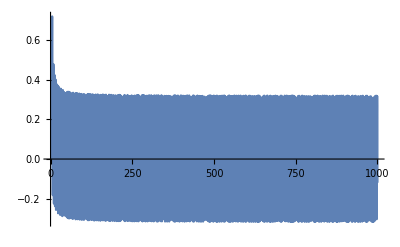

```mathematica
Plot[x*BesselJ[3,x]*BesselJ[4,x],{x,0,1000}]
```

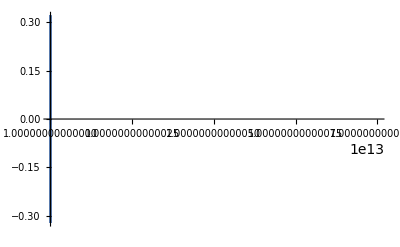

```mathematica
With[{h=10^13},Plot[x*BesselJ[5,x]*BesselJ[6,x],{x,h,h+10}]]
```

However, if we do not care about the delta part, we find that the principal parts agree with the annihilating ideal that is computed for the right-hand side:

```mathematica
pp=First[CreativeTelescoping[BesselJ[m,a*x]*BesselJ[n,b*x],Der[x],{Der[a],Der[b],S[m],S[n]}]]
```

{a D_a+b D_b+1,(-b^2+b^2 m^2-2 b^2 n-b^2 n^2)S_n^2+(2 a^2 b-2 b^3+2 a^2 b n-2 b^3 n)D_b+(-b^2+b^2 m^2-2 a^2 n-2 a^2 n^2+b^2 n^2),(a b+a b m+a b n)S_m S_n+(a^2 b-b^3)D_b+(-b^2-b^2 m-a^2 n),(a^2+2 a^2 m+a^2 m^2-a^2 n^2)S_m^2+(-2 a^2 b+2 b^3-2 a^2 b m+2 b^3 m)D_b+(-a^2+2 b^2-2 a^2 m+4 b^2 m-a^2 m^2+2 b^2 m^2-a^2 n^2),(-a^2 b+b^3)D_b S_n+(a b m-a b n)S_m+(-a^2+b^2+b^2 m-a^2 n)S_n,(a^2 b-b^3)D_b S_m+(b^2 m-a^2 n)S_m+(a b m-a b n)S_n,(a^2 b^2-b^4)D_b^2+(a^2 b-3 b^3)D_b+(-b^2+b^2 m^2-a^2 n^2)}

```mathematica
rhs=Annihilator[b^n*a^(-n-1)*Gamma[(m+n+1)/2]/Gamma[n+1]/Gamma[(m-n+1)/2]*Hypergeometric2F1[(m+n+1)/2,(n-m+1)/2,n+1,b^2/a^2],{Der[a],Der[b],S[m],S[n]}]
```

{a D_a+b D_b+1,(-b^2+b^2 m^2-2 b^2 n-b^2 n^2)S_n^2+(2 a^2 b-2 b^3+2 a^2 b n-2 b^3 n)D_b+(-b^2+b^2 m^2-2 a^2 n-2 a^2 n^2+b^2 n^2),(a b+a b m+a b n)S_m S_n+(a^2 b-b^3)D_b+(-b^2-b^2 m-a^2 n),(a^2+2 a^2 m+a^2 m^2-a^2 n^2)S_m^2+(-2 a^2 b+2 b^3-2 a^2 b m+2 b^3 m)D_b+(-a^2+2 b^2-2 a^2 m+4 b^2 m-a^2 m^2+2 b^2 m^2-a^2 n^2),(a^2 b-b^3)D_b S_n+(-a b m+a b n)S_m+(a^2-b^2-b^2 m+a^2 n)S_n,(a^2 b-b^3)D_b S_m+(b^2 m-a^2 n)S_m+(a b m-a b n)S_n,(a^2 b^2-b^4)D_b^2+(a^2 b-3 b^3)D_b+(-b^2+b^2 m^2-a^2 n^2)}

```mathematica
GBEqual[pp,rhs]
```

True

Aiming at a rigorous proof, Zeilberger's original (slow) algorithm seems to be the perfect tool for this specific problem. Recall that this algorithm first completely eliminates x, and then does the splitting into principal part and delta part. Hence no x occurs in the delta part and we can expect the corresponding limits to converge. Additionally we would like to have no derivatives w.r.t. a or b in the delta parts, since they cause the same problems. 
Operators with these properties can be found by means of our command FindRelation, where the first condition can be encoded by the
option Eliminate, and the second by the option Support: we give all monomials up to total degree 2, but omit Der[a]*Der[x] and Der[b]*Der[x].

```mathematica
ops={Der[x],Der[a],Der[b],S[m],S[n]};
supp=Complement[Join[{1},ops,Flatten[Outer[Times,ops,ops]]],Der[x]*{Der[a],Der[b]}]
```

{1,Der[a],Der[a]^2,Der[b],Der[a] Der[b],Der[b]^2,Der[x],Der[x]^2,S[m],Der[a] S[m],Der[b] S[m],Der[x] S[m],S[m]^2,S[n],Der[a] S[n],Der[b] S[n],Der[x] S[n],S[m] S[n],S[n]^2}

```mathematica
rels=FindRelation[Annihilator[BesselJ[m,a*x]*BesselJ[n,b*x],ops],Eliminate->x,Support->supp]
```

{-a b^2 m D_a S_m+(a^2 b+a^2 b n)D_a S_n+(-a^2 b-a^2 b n)D_b S_m+a b^2 m D_b S_n+(-b^2 m-b^2 m^2+a^2 n+a^2 n^2)S_m,(2+2 m)D_x S_m+(a+a m-a n)S_m^2+(2 b+2 b m)S_m S_n+(-a-a m-a n),(2+2 n)D_x S_n+(2 a+2 a n)S_m S_n+(b-b m+b n)S_n^2+(-b-b m-b n),-a b D_a S_n+a b D_b S_m-a n S_m+b m S_n,-a^2 b^2 D_a^2+a^2 b^2 D_b^2-a b^2 D_a+a^2 b D_b+(b^2 m^2-a^2 n^2)}

We now have to separate principal parts and delta parts by hand:

```mathematica
pps=OrePolynomialSubstitute[rels,{Der[x]->0}]
```

{-a b^2 m D_a S_m+(a^2 b+a^2 b n)D_a S_n+(-a^2 b-a^2 b n)D_b S_m+a b^2 m D_b S_n+(-b^2 m-b^2 m^2+a^2 n+a^2 n^2)S_m,(a+a m-a n)S_m^2+(2 b+2 b m)S_m S_n+(-a-a m-a n),(2 a+2 a n)S_m S_n+(b-b m+b n)S_n^2+(-b-b m-b n),-a b D_a S_n+a b D_b S_m-a n S_m+b m S_n,-a^2 b^2 D_a^2+a^2 b^2 D_b^2-a b^2 D_a+a^2 b D_b+(b^2 m^2-a^2 n^2)}

```mathematica
deltas=Together[(Normal/@(rels-pps))/Der[x]]
```

{0,2 (1+m) S[m],2 (1+n) S[n],0,0}

It is now obvious that all limits will tend to zero.

```mathematica
ass=Assumptions->a>0&&b>0&&m≥0&&n≥0;
inhom=((Limit[#,x->Infinity,ass]-FullSimplify[#/.x->0,ass]))&/@ApplyOreOperator[deltas,BesselJ[m,a*x]*BesselJ[n,b*x]]
```

{0,0,0,0,0}

A final Gröbner basis computation is needed to convert these into our original setting:

```mathematica
ann=OreGroebnerBasis[pps,OreAlgebra[Der[a],Der[b],S[m],S[n]],MonomialOrder->DegreeLexicographic]
```

{-a D_a-b D_b-1,(-b^2+b^2 m^2-2 b^2 n-b^2 n^2)S_n^2+(2 a^2 b-2 b^3+2 a^2 b n-2 b^3 n)D_b+(-b^2+b^2 m^2-2 a^2 n-2 a^2 n^2+b^2 n^2),(a b+a b m+a b n)S_m S_n+(a^2 b-b^3)D_b+(-b^2-b^2 m-a^2 n),(-a^2-2 a^2 m-a^2 m^2+a^2 n^2)S_m^2+(2 a^2 b-2 b^3+2 a^2 b m-2 b^3 m)D_b+(a^2-2 b^2+2 a^2 m-4 b^2 m+a^2 m^2-2 b^2 m^2+a^2 n^2),(-a^2 b+b^3)D_b S_n+(a b m-a b n)S_m+(-a^2+b^2+b^2 m-a^2 n)S_n,(a^2 b-b^3)D_b S_m+(b^2 m-a^2 n)S_m+(a b m-a b n)S_n,(-a^2 b^2+b^4)D_b^2+(-a^2 b+3 b^3)D_b+(b^2-b^2 m^2+a^2 n^2)}

Again, we get the same annihilating ideal as for the right-hand side:

```mathematica
GBEqual[rhs,ann]
```

True

Initial values:

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,S_n,S_m,D_b}

```mathematica
ApplyOreOperator[uts,BesselJ[m,a*x]*BesselJ[n,b*x]]/.m->0/.n->0/.a->1/.b->1/2
```

{BesselJ[0,x/2] BesselJ[0,x],BesselJ[0,x] BesselJ[1,x/2],BesselJ[0,x/2] BesselJ[1,x],-x BesselJ[0,x] BesselJ[1,x/2]}

In some Mathematica versions, the last of the following integrals is declared to diverge, but in other versions it works (and the correct value is given).

```mathematica
Integrate[%,{x,0,Infinity}]
```

Integrate::idiv: Integral of -x BesselJ[0,x] BesselJ[1,x/2] does not converge on {0,∞}.

{(2 EllipticK[1/4])/π,0,1,∫_0^∞ -x BesselJ[0,x] BesselJ[1,x/2]ⅆx}

```mathematica
ApplyOreOperator[uts,b^n*a^(-n-1)*Gamma[(m+n+1)/2]/Gamma[n+1]/Gamma[(m-n+1)/2]*Hypergeometric2F1[(m+n+1)/2,(n-m+1)/2,n+1,b^2/a^2]]/.m->0/.n->0/.a->1/.b->1/2
```

{(2 EllipticK[1/4])/π,0,1,1/4 Hypergeometric2F1[3/2,3/2,2,1/4]}

```mathematica
FullSimplify[%-%%]
```

Integrate::idiv: Integral of -x BesselJ[0,x] BesselJ[1,x/2] does not converge on {0,∞}.

{0,0,0,1/4 Hypergeometric2F1[3/2,3/2,2,1/4]-∫_0^∞ -x BesselJ[0,x] BesselJ[1,x/2]ⅆx}

### 6.774 ∫_0^∞ 1/(√(x^2+a^2))log((√(x^2+a^2)+x)/(√(x^2+a^2)-x)) 0b xⅆx==(0(a b)/2)^2

On page 747 we have for Re(a)>0 and b>0:

```mathematica
TraditionalForm[HoldForm[Integrate[Log[(Sqrt[x^2+a^2]+x)/(Sqrt[x^2+a^2]-x)]*BesselJ[0,b*x]/Sqrt[x^2+a^2],{x,0,Infinity}]==BesselK[0,a*b/2]^2]]
```

∫_0^∞ (log((√(x^2+a^2)+x)/(√(x^2+a^2)-x)) 0b x)/(√(x^2+a^2))ⅆx==(0(a b)/2)^2

```mathematica
Annihilator[Integrate[Log[(Sqrt[x^2+a^2]+x)/(Sqrt[x^2+a^2]-x)]*BesselJ[0,b*x]/Sqrt[x^2+a^2],{x,0,Infinity}],{Der[a],Der[b]},Assumptions->Re[a]>0&&b>0]
```

Annihilator::fail: Cannot evaluate the delta part of an integral (problem with upper bound).

$Failed

So we have to do some work by hand.

```mathematica
{ann,delta}=CreativeTelescoping[Log[(Sqrt[x^2+a^2]+x)/(Sqrt[x^2+a^2]-x)]*BesselJ[0,b*x]/Sqrt[x^2+a^2],Der[x],{Der[a],Der[b]}]
```

{{-a D_a+b D_b,b^2 D_b^3+3 b D_b^2+(1-a^2 b^2)D_b-a^2 b},{-x,(-a^3-a x^2)/x D_a D_b-a^2/x D_b+b (a^2 x+x^3)}}

```mathematica
Limit[ApplyOreOperator[delta[[1]],Log[(Sqrt[x^2+a^2]+x)/(Sqrt[x^2+a^2]-x)]*BesselJ[0,b*x]/Sqrt[x^2+a^2]],x->Infinity,Assumptions->Re[a]>0&&b>0]
```

0

```mathematica
Simplify[ApplyOreOperator[delta[[2]],Log[(Sqrt[x^2+a^2]+x)/(Sqrt[x^2+a^2]-x)]*BesselJ[0,b*x]/Sqrt[x^2+a^2]]]
```

(x (-2 √(a^2+x^2) BesselJ[1,b x]+b (a^2+x^2) BesselJ[0,b x] Log[(x+√(a^2+x^2))/(-x+√(a^2+x^2))]))/(√(a^2+x^2))

```mathematica
Limit[%,x->Infinity,Assumptions->Re[a]>0&&b>0]
```

Limit[(x (-2 √(a^2+x^2) BesselJ[1,b x]+b (a^2+x^2) BesselJ[0,b x] Log[(x+√(a^2+x^2))/(-x+√(a^2+x^2))]))/(√(a^2+x^2)),x→∞,Assumptions→Re[a]>0&&b>0]

```mathematica
%%/.a->1/.b->1
```

(x (-2 √(1+x^2) BesselJ[1,x]+(1+x^2) BesselJ[0,x] Log[(x+√(1+x^2))/(-x+√(1+x^2))]))/(√(1+x^2))

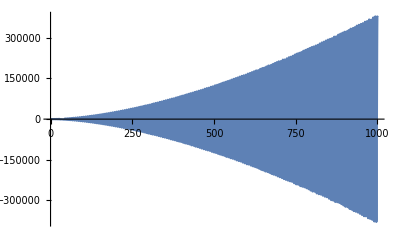

```mathematica
Plot[%,{x,0,1000}]
```

So, although the limit of the delta part does not converge, the principal part makes perfect sense:

```mathematica
Annihilator[BesselK[0,a*b/2]^2,{Der[a],Der[b]}]
```

{a D_a-b D_b,b^2 D_b^3+3 b D_b^2+(1-a^2 b^2)D_b-a^2 b}

```mathematica
GBEqual[%,ann]
```

True

Fortunately, we can avoid this problem by reversing the order of the operators Der[a] and Der[b]. This will influence the creative telescoping relations in a way that the delta parts vanish:

```mathematica
Annihilator[Integrate[Log[(Sqrt[x^2+a^2]+x)/(Sqrt[x^2+a^2]-x)]*BesselJ[0,b*x]/Sqrt[x^2+a^2],{x,0,Infinity}],{Der[b],Der[a]},Assumptions->Re[a]>0&&b>0]
```

{b D_b-a D_a,a^2 D_a^3+3 a D_a^2+(1-a^2 b^2)D_a-a b^2}

```mathematica
Annihilator[BesselK[0,a*b/2]^2,{Der[b],Der[a]}]
```

{b D_b-a D_a,a^2 D_a^3+3 a D_a^2+(1-a^2 b^2)D_a-a b^2}

But still, the initial values are difficult to check:

```mathematica
uts=UnderTheStaircase[%]
```

{1,D_a,D_a^2}

```mathematica
FullSimplify[ApplyOreOperator[uts,Log[(Sqrt[x^2+a^2]+x)/(Sqrt[x^2+a^2]-x)]*BesselJ[0,b*x]/Sqrt[x^2+a^2]]/.a->1/.b->1]
```

{(BesselJ[0,x] Log[1+2 x (x+√(1+x^2))])/(√(1+x^2)),-(BesselJ[0,x] (2 x √(1+x^2)+Log[1+2 x (x+√(1+x^2))]))/((1+x^2)^(3/2)),(BesselJ[0,x] (2 x √(1+x^2) (4+x^2)-(-2+x^2) Log[1+2 x (x+√(1+x^2))]))/((1+x^2)^(5/2))}

```mathematica
Integrate[%,{x,0,Infinity}]
```

{∫_0^∞ (BesselJ[0,x] Log[1+2 x (x+√(1+x^2))])/(√(1+x^2))ⅆx,∫_0^∞ -(BesselJ[0,x] (2 x √(1+x^2)+Log[1+2 x (x+√(1+x^2))]))/((1+x^2)^(3/2))ⅆx,∫_0^∞ (BesselJ[0,x] (2 x √(1+x^2) (4+x^2)-(-2+x^2) Log[1+2 x (x+√(1+x^2))]))/((1+x^2)^(5/2))ⅆx}

Unfortunately, Mathematica cannot do these integrals. So we content ourselves with a numerical check:

```mathematica
%/.Integrate->NIntegrate
```

{0.854551,-1.53125,3.33042}

```mathematica
ApplyOreOperator[uts,BesselK[0,a*b/2]^2]/.a->1/.b->1
```

{BesselK[0,1/2]^2,-BesselK[0,1/2] BesselK[1,1/2],1/2 BesselK[1,1/2]^2-1/4 BesselK[0,1/2] (-BesselK[0,1/2]-BesselK[2,1/2])}

```mathematica
N[%]
```

{0.854551,-1.53125,3.33042}

### 7.313 ∫_-1^1 (1-x^2)^(nu-1/2) C_m^(nu)(x) C_n^(nu)(x)ⅆx

The following identity (p. 795) holds for m ≠ n and Re[nu]>-1/2.

```mathematica
TraditionalForm[HoldForm[Integrate[(1-x^2)^(nu-1/2)*GegenbauerC[m,nu,x]*GegenbauerC[n,nu,x],{x,-1,1}]==0]]
```

∫_-1^1 (1-x^2)^(nu-1/2) C_m^(nu)(x) C_n^(nu)(x)ⅆx==0

The exception for m=n is not recognized automatically by our program, so we get 1 as an annihilator, whatever m and n are:

```mathematica
Annihilator[Integrate[(1-x^2)^(nu-1/2)*GegenbauerC[m,nu,x]*GegenbauerC[n,nu,x],{x,-1,1}],{S[nu],S[m],S[n]},Assumptions->nu>1/2]
```

{1}

To see that for m=n, something goes wrong, we have to look at the certificate of creative telescoping. Indeed, the factor (m-n) appears in the denominator:

```mathematica
CreativeTelescoping[(1-x^2)^(nu-1/2)*GegenbauerC[m,nu,x]*GegenbauerC[n,nu,x],Der[x],{S[nu],S[m],S[n]}]
```

{{1},{(-1-m)/((m-n) (m+n+2 nu))S_m+(-1-n)/((-m+n) (m+n+2 nu))S_n+x/(m+n+2 nu)}}

In the case m=n we get (for Re[nu]>-1/2,  formula 7.313.2):

```mathematica
TraditionalForm[HoldForm[Integrate[(1-x^2)^(nu-1/2)*GegenbauerC[n,nu,x]^2,{x,-1,1}]==Pi*2^(1-2nu)*Gamma[2nu+n]/n!/(n+nu)/Gamma[nu]^2]]
```

∫_-1^1 (1-x^2)^(nu-1/2) (C_n^(nu)(x))^2ⅆx==(π 2^(1-2 nu) 2 nu+n)/((n! (n+nu)) nu^2)

This evaluation can be FOUND automatically! We compute a recurrence in n for the integral and one initial value for n=0 (for the automatic treatment, we have to sharpen the conditions on nu):

```mathematica
ann=Annihilator[Integrate[(1-x^2)^(nu-1/2)*GegenbauerC[n,nu,x]^2,{x,-1,1}],S[n],Assumptions->Re[nu]>1/2]
```

{(-1-2 n-n^2-nu-n nu)S_n+(n^2+3 n nu+2 nu^2)}

```mathematica
(1-x^2)^(nu-1/2)*GegenbauerC[n,nu,x]*GegenbauerC[n,nu,x]/.n->0
```

(1-x^2)^(-1/2+nu)

```mathematica
Integrate[%,{x,-1,1},Assumptions->Re[nu]>-1/2]/.Sec[nu*Pi]->Gamma[1/2+nu]*Gamma[1/2-nu]/Pi
```

(√π Gamma[1/2+nu])/Gamma[1+nu]

```mathematica
FullSimplify[RSolve[{ApplyOreOperator[First[ann],f[n]]==0,f[0]==%},f[n],n]]
```

{{f[n]→(2^(1-2 nu) π Gamma[n+2 nu])/((n+nu) Gamma[1+n] Gamma[nu]^2)}}

This evaluation agrees exactly with the formula given in Gradshteyn/Ryzhik.

### 7.322 ∫_0^(2 a) (x (2 a-x))^(nu-1/2) C_n^(nu)(x/a-1) ⅇ^(-b x)ⅆx==((-1)^n π Γ(n+2 nu) (a/(2 b))^nu ⅇ^(-a b) I_(n+nu)(a b))/(n! Γ(nu)) (misprint in the book!)

The formula 7.322  (S. 797) is not correct as we will show in the following.

```mathematica
TraditionalForm[HoldForm[Integrate[(x(2a-x))^(nu-1/2)*GegenbauerC[n,nu,x/a-1]*E^(-b*x),{x,0,2a}]==(-1)^n*Pi*Gamma[2nu+n]/n!/Gamma[nu]*(a/(2b))^nu*E^(-a*b)*BesselI[nu+n,a*b]]]
```

∫_0^(2 a) (x (2 a-x))^(nu-1/2) C_n^(nu)(x/a-1) ⅇ^(-b x)ⅆx==((-1)^n π 2 nu+n (a/(2 b))^nu ⅇ^(-a b) nu+na b)/(n! nu)

Annihilating ∂-finite ideal for the integrand

```mathematica
ann=Annihilator[(x(2a-x))^(nu-1/2)*GegenbauerC[n,nu,x/a-1]*E^(-b*x),{Der[x],Der[a],Der[b],S[n],S[nu]}]
```

{(a^2+a^2 n-a x-a n x)S_n-2 nu S_nu+(a^2 n+2 a^2 nu),D_b+x,(2 a^3-3 a^2 x+a x^2)D_a-2 nu S_nu+(a^2-2 a^2 nu-a x+2 a n x+6 a nu x-n x^2-2 nu x^2),(2 a^2 x-3 a x^2+x^3)D_x+2 nu S_nu+(a^2-2 a^2 nu-2 a x+2 a^2 b x-2 a n x+x^2-3 a b x^2+n x^2+b x^3),(4 nu+4 nu^2)S_nu^2+(-2 a^2 nu-4 a^2 nu^2-8 a nu x-8 a n nu x-8 a nu^2 x+4 nu x^2+4 n nu x^2+4 nu^2 x^2)S_nu+(2 a^3 n x+2 a^3 n^2 x+4 a^3 nu x+8 a^3 n nu x+8 a^3 nu^2 x-a^2 n x^2-a^2 n^2 x^2-2 a^2 nu x^2-4 a^2 n nu x^2-4 a^2 nu^2 x^2)}

We can use Zeilberger's slow algorithm or Takayama (assuming natural boundaries)

```mathematica
Timing[gb=OreGroebnerBasis[ann,OreAlgebra[x,Der[x],Der[a],Der[b],S[n],S[nu]],MonomialOrder->EliminationOrder[1]];]
```

{34.94,Null}

```mathematica
LeadingPowerProduct/@gb
```

{S_n^2,D_b S_nu,D_b S_n,D_x S_n,D_x D_b,D_a S_nu^2,D_a S_n S_nu,D_a D_b^2,D_a^2 D_b,D_x S_nu^2,D_x D_a S_nu,D_x^2 D_a,x}

```mathematica
gb=OreGroebnerBasis[OrePolynomialSubstitute[Drop[gb,-1],{Der[x]->0}],OreAlgebra[Der[a],Der[b],S[n],S[nu]],MonomialOrder->DegreeLexicographic];
```

```mathematica
UnderTheStaircase[gb]
```

{1,S_nu,S_n,D_b,S_nu^2,S_n S_nu}

```mathematica
Timing[tak=Takayama[ann,{x}];]
```

{5.868,Null}

```mathematica
UnderTheStaircase[tak]
```

{1,S_nu,S_n,D_b,S_nu^2,S_n S_nu}

We get the same annihilating ideal for the integral:

```mathematica
GBEqual[gb,tak]
```

True

But Chyzak's algorithm is preferable. The only problem is that in this instance the inhomogeneous part cannot be evaluated automatically. Hence we use the option Inhomogeneous->True and simplify it ourselves (it turns out to be 0 anyway).

```mathematica
{lhs,inh}=Annihilator[Integrate[(x(2a-x))^(nu-1/2)*GegenbauerC[n,nu,x/a-1]*E^(-b*x),{x,0,2a}],{Der[a],Der[b],S[n],S[nu]},Assumptions->nu≥1,Inhomogeneous->True];
```

```mathematica
Simplify[Simplify[ReleaseHold[inh/.Limit->myLimit]]/.myLimit->Limit,Assumptions->nu≥1&&Element[n,Integers]]
```

{0,0,0,0}

```mathematica
rhs=Annihilator[(-1)^n*Pi*Gamma[2nu+n]/n!/Gamma[nu]*(a/(2b))^nu*E^(-a*b)*BesselI[nu+n,a*b],{Der[a],Der[b],S[n],S[nu]}]
```

{(a+2 a n+a n^2+2 a nu+2 a n nu)S_n+2 b nu S_nu,(-b n-b n^2-2 b nu-4 b n nu-4 b nu^2)D_b+2 b^2 nu S_nu+(-a b n+n^2-a b n^2+n^3-2 a b nu+2 n nu-4 a b n nu+4 n^2 nu-4 a b nu^2+4 n nu^2),(-a n-a n^2-2 a nu-4 a n nu-4 a nu^2)D_a+2 b^2 nu S_nu+(-a b n+n^2-a b n^2+n^3-2 a b nu+4 n nu-4 a b n nu+6 n^2 nu+4 nu^2-4 a b nu^2+12 n nu^2+8 nu^3),(4 b^2 nu+4 b^2 nu^2)S_nu^2+(24 nu+44 n nu+24 n^2 nu+4 n^3 nu+64 nu^2+76 n nu^2+20 n^2 nu^2+56 nu^3+32 n nu^3+16 nu^4)S_nu+(-6 a^2 n-11 a^2 n^2-6 a^2 n^3-a^2 n^4-12 a^2 nu-44 a^2 n nu-36 a^2 n^2 nu-8 a^2 n^3 nu-44 a^2 nu^2-72 a^2 n nu^2-24 a^2 n^2 nu^2-48 a^2 nu^3-32 a^2 n nu^3-16 a^2 nu^4)}

```mathematica
GBEqual[lhs,rhs]
```

True

We see that with Zeilberger slow and Takayama we got only a subideal

```mathematica
OreReduce[tak,rhs]
```

{0,0,0,0,0,0,0}

Using the result from Chyzak's algorithm we have to compare two initial values:

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,S_nu}

```mathematica
ApplyOreOperator[uts,(x(2a-x))^(nu-1/2)*GegenbauerC[n,nu,x/a-1]*E^(-b*x)]/.a->1/.b->1/.n->1/.nu->0
```

{0,2 ⅇ^-x (-1+x) √((2-x) x)}

```mathematica
Integrate[%,{x,0,2}]
```

{0,-(2 π BesselI[2,1])/ⅇ}

```mathematica
ApplyOreOperator[uts,(-1)^n*Pi*Gamma[2nu+n]/n!/Gamma[nu]*(a/(2b))^nu*E^(-a*b)*BesselI[nu+n,a*b]]/.a->1/.b->1/.n->1/.nu->0
```

{0,-(π BesselI[2,1])/ⅇ}

Obviously, on the right hand side there is a factor 2 missing. Hence we found a misprint in the Gradshteyn/Ryzhik book.

### 7.349 ∫_-1^1 (T_n(1-x^2 y))/(√(1-x^2))ⅆx==(π (n1-y+n-11-y))/2

On page 801, we find:

```mathematica
TraditionalForm[HoldForm[Integrate[ChebyshevT[n,1-x^2 y]/Sqrt[1-x^2],{x,-1,1}]==Pi/2*(LegendreP[n,1-y]+LegendreP[n-1,1-y])]]
```

∫_-1^1 (T_n(1-x^2 y))/(√(1-x^2))ⅆx==1/2 π (n1-y+n-11-y)

We get two creative telescoping  relations for the integrand.

```mathematica
CreativeTelescoping[ChebyshevT[n,1-x^2 y]/Sqrt[1-x^2],Der[x],{S[n],Der[y]}]
```

{{(2 n+2 n^2)S_n+(-2 y-4 n y+y^2+2 n y^2)D_y+(-2 n-2 n^2+n y+2 n^2 y),(-2 y+y^2)D_y^2+(-2+y)D_y-n^2},{(y (2-2 x^2-x^2 y+x^4 y))/x D_y+(-n x+n x^3) y,(-1+x^2)/x D_y}}

We can check by hand that the delta parts vanish...

```mathematica
(Limit[#,x->1]-Limit[#,x->-1])&[ApplyOreOperator[Last[%],ChebyshevT[n,1-x^2 y]/Sqrt[1-x^2]]]
```

{0,0}

... or we can just use the command Annihilator, that does all these steps automatically:

```mathematica
Annihilator[Integrate[ChebyshevT[n,1-x^2 y]/Sqrt[1-x^2],{x,-1,1}],{S[n],Der[y]}]
```

{(2 n+2 n^2)S_n+(-2 y-4 n y+y^2+2 n y^2)D_y+(-2 n-2 n^2+n y+2 n^2 y),(-2 y+y^2)D_y^2+(-2+y)D_y-n^2}

Now the right-hand side:

```mathematica
Annihilator[Pi/2*(LegendreP[n,1-y]+LegendreP[n-1,1-y]),{S[n],Der[y]}]
```

{2 n S_n D_y+(-2 y+y^2)D_y^2+(-2-2 n+2 y+2 n y)D_y+(n+n^2),(4 n+6 n^2+2 n^3)S_n^2+(-4 y^2+4 y^3-y^4)D_y^2+(-4 n-8 n^2-4 n^3+4 n y+8 n^2 y+4 n^3 y)S_n+(-4 y-4 n y+6 y^2+6 n y^2-2 y^3-2 n y^3)D_y+(2 n^2+2 n^3+2 n y+2 n^2 y-n y^2-n^2 y^2),(4 y^2-4 y^3+y^4)D_y^3+(8 y-12 y^2+4 y^3)D_y^2+(-2 n^2-2 n^3)S_n+(-4 y+2 n y+6 n^2 y+2 y^2-n y^2-3 n^2 y^2)D_y+(2 n^2+2 n^3-2 n^2 y-2 n^3 y)}

This is a classical case where a little bit of human intervention is desired. When the closure property DFinitePlus is used, the annihilating ideal often overshoots, especially when the two functions to be combined are very "similar" (as it is the case here). We can get a better result by applying the closure property DFiniteOreAction. To this purpose, the sum of the two Legendre polynomials has to be reformulated as applying the operator S[n]+1 to the function LegendreP[n-1,1-y].

```mathematica
rhs=Annihilator[ApplyOreOperator[S[n]+1,LegendreP[n-1,1-y]],{S[n],Der[y]}]
```

{(2 n+2 n^2)S_n+(-2 y-4 n y+y^2+2 n y^2)D_y+(-2 n-2 n^2+n y+2 n^2 y),(2 y-y^2)D_y^2+(2-y)D_y+n^2}

Now we get the same annihilating ideal, and have to compare two initial values.

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_y}

For n=1:

```mathematica
Integrate[ApplyOreOperator[uts,ChebyshevT[n,1-x^2 y]/Sqrt[1-x^2]]/.n->1/.y->0,{x,-1,1}]
```

{π,-π/2}

```mathematica
Together[ApplyOreOperator[uts,Pi/2*(LegendreP[n,1-y]+LegendreP[n-1,1-y])]/.n->1]/.y->0
```

{π,-π/2}

### 7.512.5 ∫_0^1 x^(r-1) (1-x)^(s-1) abcxⅆx==(r s _3 F_2(a,b,r;c,r+s;1))/(r+s)

```mathematica
HoldForm[Integrate[x^(r-1)(1-x)^(s-1)Hypergeometric2F1[a,b,c,x],{x,0,1}]==Gamma[r] Gamma[s]/Gamma[r+s] HypergeometricPFQ[{a,b,r},{c,r+s},1]]//TraditionalForm
(* Re[r]>0, Re[s]>0, Re[c+s-a-b]>0 *)
```

∫_0^1 x^(r-1) (1-x)^(s-1) abcxⅆx==(r s _3 F_2(a,b,r;c,r+s;1))/(r+s)

We prove this identity for integers a,b,c,r,s such that c + s - a - b > 0  and  a ≥ 0, b ≥ 0, c ≥ 1, r ≥ 1, s ≥ 2. The latter condition is because for s ≥ 1, the delta part in the following computation cannot be simplified. However, the special case s=1 could be treated separately in the very same manner.

```mathematica
lhs=Annihilator[Integrate[x^(r-1)*(1-x)^(s-1)*Hypergeometric2F1[a,b,c,x],{x,0,1}],{S[a],S[b],S[c],S[r],S[s]},Assumptions->s>1]
```

{S_r+S_s-1,(a b c-a c^2-b c^2+c^3-a b r+a c r+b c r-c^2 r)S_c+(-a b c+a c r+b c r-c r^2+a c s+b c s-2 c r s-c s^2)S_s+(a c^2+b c^2-c^3-a c r-b c r+c^2 r-a c s-b c s+c r s+c s^2),(-b-a b-b^2+b c+b s)S_b+(a b-a r-b r+r^2-a s-b s+2 r s+s^2)S_s+(b+b^2-b c+a s-r s-s^2),(-a-a^2-a b+a c+a s)S_a+(a b-a r-b r+r^2-a s-b s+2 r s+s^2)S_s+(a+a^2-a c+b s-r s-s^2),(1-a-b+a b+2 r-a r-b r+r^2+2 s-a s-b s+2 r s+s^2)S_s^2+(-1+a+b-a b-r+a r+b r-c r-2 s+2 a s+2 b s-c s-2 r s-2 s^2)S_s+(-a s-b s+c s+s^2)}

Now the right-hand side. Substituting 1 into a hypergeometric PFQ often leads to the following problem.

```mathematica
rhs=Annihilator[Gamma[r]*Gamma[s]/Gamma[r+s]*HypergeometricPFQ[{a,b,r},{c,r+s},1],{S[a],S[b],S[c],S[r],S[s]}]
```

{S_r+S_s-1,(a b c-a c^2-b c^2+c^3-a b r+a c r+b c r-c^2 r)S_c+(-a b c+a c r+b c r-c r^2+a c s+b c s-2 c r s-c s^2)S_s+(a c^2+b c^2-c^3-a c r-b c r+c^2 r-a c s-b c s+c r s+c s^2),(b+a b+b^2-b c-b s)S_b+(-a b+a r+b r-r^2+a s+b s-2 r s-s^2)S_s+(-b-b^2+b c-a s+r s+s^2),(a+a^2+a b-a c-a s)S_a+(-a b+a r+b r-r^2+a s+b s-2 r s-s^2)S_s+(-a-a^2+a c-b s+r s+s^2),(1-a-b+a b+2 r-a r-b r+r^2+2 s-a s-b s+2 r s+s^2)S_s^2+(-1+a+b-a b-r+a r+b r-c r-2 s+2 a s+2 b s-c s-2 r s-2 s^2)S_s+(-a s-b s+c s+s^2)}

We can compute an annihilating ideal for the PFQ by using its definition.

```mathematica
{pfq,inh}=Annihilator[Sum[Pochhammer[a,k]*Pochhammer[b,k]*Pochhammer[r,k]/Pochhammer[c,k]/Pochhammer[r+s,k]/k!,{k,0,Infinity}],{S[a],S[b],S[c],S[r],S[s]},Inhomogeneous->True]
```

{{r S_r+s S_s+(-r-s),(a b c r-a c^2 r-b c^2 r+c^3 r-a b r^2+a c r^2+b c r^2-c^2 r^2+a b c s-a c^2 s-b c^2 s+c^3 s-a b r s+a c r s+b c r s-c^2 r s)S_c+(-a b c s+a c r s+b c r s-c r^2 s+a c s^2+b c s^2-2 c r s^2-c s^3)S_s+(a c^2 r+b c^2 r-c^3 r-a c r^2-b c r^2+c^2 r^2+a c^2 s+b c^2 s-c^3 s-2 a c r s-2 b c r s+c^2 r s+c r^2 s-a c s^2-b c s^2+2 c r s^2+c s^3),(b r+a b r+b^2 r-b c r+b s+a b s+b^2 s-b c s-b r s-b s^2)S_b+(-a b s+a r s+b r s-r^2 s+a s^2+b s^2-2 r s^2-s^3)S_s+(-b r-b^2 r+b c r-b s-b^2 s+b c s-a r s+r^2 s-a s^2+2 r s^2+s^3),(a r+a^2 r+a b r-a c r+a s+a^2 s+a b s-a c s-a r s-a s^2)S_a+(-a b s+a r s+b r s-r^2 s+a s^2+b s^2-2 r s^2-s^3)S_s+(-a r-a^2 r+a c r-a s-a^2 s+a c s-b r s+r^2 s-b s^2+2 r s^2+s^3),(-1+a+b-a b-2 r+a r+b r-r^2-3 s+2 a s+2 b s-a b s-4 r s+a r s+b r s-r^2 s-3 s^2+a s^2+b s^2-2 r s^2-s^3)S_s^2+(1-a-b+a b+2 r-2 a r-2 b r+a b r+c r+r^2-a r^2-b r^2+c r^2+3 s-3 a s-3 b s+a b s+c s+5 r s-3 a r s-3 b r s+2 c r s+2 r^2 s+4 s^2-2 a s^2-2 b s^2+c s^2+4 r s^2+2 s^3)S_s+(a r+b r-c r+a r^2+b r^2-c r^2+a s+b s-c s-r s+2 a r s+2 b r s-2 c r s-r^2 s-s^2+a s^2+b s^2-c s^2-2 r s^2-s^3)},{Hold[Limit[0,k→∞]],Hold[Limit[-(c k (c-r-s) (r+s) Pochhammer[a,k] Pochhammer[b,k] Pochhammer[r,k])/(k! Pochhammer[c,k] Pochhammer[r+s,k]),k→∞]],Hold[Limit[-((-k+c k+k^2) (r+s) Pochhammer[a,k] Pochhammer[b,k] Pochhammer[r,k])/(k! Pochhammer[c,k] Pochhammer[r+s,k]),k→∞]],Hold[Limit[-((-k+c k+k^2) (r+s) Pochhammer[a,k] Pochhammer[b,k] Pochhammer[r,k])/(k! Pochhammer[c,k] Pochhammer[r+s,k]),k→∞]],Hold[Limit[-((-k+c k+k^2) (r+s) (1+r+s) Pochhammer[a,k] Pochhammer[b,k] Pochhammer[r,k])/((k+r+s) k! Pochhammer[c,k] Pochhammer[r+s,k]),k→∞]]}}

Since we choose the parameters a,b,c,r,s in a way that everything goes well, we believe that the above limits go to 0, although Mathematica does not evaluate them (also not when giving assumptions). Alternatively, having ensured that the bounds of the sum are natural, we can call Takayama and get the same result:

```mathematica
tak=Takayama[Annihilator[Pochhammer[a,k]*Pochhammer[b,k]*Pochhammer[r,k]/Pochhammer[c,k]/Pochhammer[r+s,k]/k!,{S[k],S[a],S[b],S[c],S[r],S[s]}],{k}]
```

{-r S_r-s S_s+(r+s),(a b c r-a c^2 r-b c^2 r+c^3 r-a b r^2+a c r^2+b c r^2-c^2 r^2+a b c s-a c^2 s-b c^2 s+c^3 s-a b r s+a c r s+b c r s-c^2 r s)S_c+(-a b c s+a c r s+b c r s-c r^2 s+a c s^2+b c s^2-2 c r s^2-c s^3)S_s+(a c^2 r+b c^2 r-c^3 r-a c r^2-b c r^2+c^2 r^2+a c^2 s+b c^2 s-c^3 s-2 a c r s-2 b c r s+c^2 r s+c r^2 s-a c s^2-b c s^2+2 c r s^2+c s^3),(b r+a b r+b^2 r-b c r+b s+a b s+b^2 s-b c s-b r s-b s^2)S_b+(-a b s+a r s+b r s-r^2 s+a s^2+b s^2-2 r s^2-s^3)S_s+(-b r-b^2 r+b c r-b s-b^2 s+b c s-a r s+r^2 s-a s^2+2 r s^2+s^3),(a r+a^2 r+a b r-a c r+a s+a^2 s+a b s-a c s-a r s-a s^2)S_a+(-a b s+a r s+b r s-r^2 s+a s^2+b s^2-2 r s^2-s^3)S_s+(-a r-a^2 r+a c r-a s-a^2 s+a c s-b r s+r^2 s-b s^2+2 r s^2+s^3),(-1+a+b-a b-2 r+a r+b r-r^2-3 s+2 a s+2 b s-a b s-4 r s+a r s+b r s-r^2 s-3 s^2+a s^2+b s^2-2 r s^2-s^3)S_s^2+(1-a-b+a b+2 r-2 a r-2 b r+a b r+c r+r^2-a r^2-b r^2+c r^2+3 s-3 a s-3 b s+a b s+c s+5 r s-3 a r s-3 b r s+2 c r s+2 r^2 s+4 s^2-2 a s^2-2 b s^2+c s^2+4 r s^2+2 s^3)S_s+(a r+b r-c r+a r^2+b r^2-c r^2+a s+b s-c s-r s+2 a r s+2 b r s-2 c r s-r^2 s-s^2+a s^2+b s^2-c s^2-2 r s^2-s^3)}

```mathematica
GBEqual[pfq,tak]
```

True

With closure properties an annihilating ideal for the right-hand side is now obtained, and it turns out that the previously one computed indeed was correct:

```mathematica
GBEqual[rhs,DFiniteTimes[Annihilator[Gamma[r]*Gamma[s]/Gamma[r+s],{S[a],S[b],S[c],S[r],S[s]}],pfq]]
```

True

So we found the same annihilating ideal for both sides.

```mathematica
GBEqual[rhs,lhs]
```

True

Initial values. As we can see, the leading coefficients do have a lot of zeros, and we have to ask ourselves where we cannot apply any of the recurrences (all such values have to be given as initial conditions).

```mathematica
Factor[lhs]//TableForm
```

S_r+S_s-1
(a-c) (b-c) (c-r)S_c-c (a-r-s) (b-r-s)S_s+c (a+b-c-s) (c-r-s)
-b (1+a+b-c-s)S_b+(a-r-s) (b-r-s)S_s+(b+b^2-b c+a s-r s-s^2)
-a (1+a+b-c-s)S_a+(a-r-s) (b-r-s)S_s+(a+a^2-a c+b s-r s-s^2)
(-1+a-r-s) (-1+b-r-s)S_s^2+(-1+a+b-a b-r+a r+b r-c r-2 s+2 a s+2 b s-c s-2 r s-2 s^2)S_s-(a+b-c-s) s

```mathematica
AnnihilatorSingularities[lhs,{0,0,1,1,1}]
```

{{{a→1,c→1,r→1,s→b},b≥1},{{a→2,c→2,r→1,s→b},b≥1},{{a→2,c→1+b,r→1,s→1},b≥0},{{a→3,c→1+b,r→1,s→2},b≥0},{{b→1,c→1,r→1,s→a},a≥1},{{b→2,c→2,r→1,s→a},a≥1},{{b→2,c→1+a,r→1,s→1},a≥0},{{b→3,c→1+a,r→1,s→2},a≥0},{{b→-1+a,c→a,r→1,s→-1+a},a≥2},{{b→1+a,c→1+a,r→1,s→a},a≥1},{{a→0,b→0,c→1,r→1,s→1},True},{{a→0,b→0,c→1,r→1,s→2},True},{{a→0,b→0,c→2,r→1,s→1},True},{{a→0,b→0,c→2,r→1,s→2},True},{{a→0,b→1,c→1,r→1,s→1},True},{{a→0,b→1,c→1,r→1,s→2},True},{{a→0,b→1,c→2,r→1,s→1},True},{{a→0,b→1,c→2,r→1,s→2},True},{{a→0,b→2,c→1,r→1,s→1},True},{{a→0,b→3,c→1,r→1,s→2},True},{{a→0,b→3,c→2,r→1,s→1},True},{{a→0,b→4,c→2,r→1,s→2},True},{{a→1,b→0,c→1,r→1,s→1},True},{{a→1,b→0,c→1,r→1,s→2},True},{{a→1,b→0,c→2,r→1,s→1},True},{{a→1,b→0,c→2,r→1,s→2},True},{{a→1,b→1,c→1,r→1,s→1},True},{{a→1,b→1,c→1,r→1,s→2},True},{{a→1,b→1,c→2,r→1,s→1},True},{{a→1,b→1,c→2,r→1,s→2},True},{{a→1,b→2,c→1,r→1,s→2},True},{{a→1,b→2,c→2,r→1,s→1},True},{{a→1,b→3,c→2,r→1,s→2},True},{{a→2,b→0,c→1,r→1,s→1},True},{{a→2,b→1,c→1,r→1,s→2},True},{{a→2,b→1,c→2,r→1,s→1},True},{{a→2,b→2,c→2,r→1,s→2},True},{{a→3,b→0,c→1,r→1,s→2},True},{{a→3,b→0,c→2,r→1,s→1},True},{{a→3,b→1,c→2,r→1,s→2},True},{{a→4,b→0,c→2,r→1,s→2},True}}

As we see here, there are infinitely many singular points . It turns out that they all lie in the hyperplane generated by the condition c + s - a - b > 0:

```mathematica
{a,b,c,r,s}/.Cases[%,{repl_,Except[True]}:>repl]
```

{{1,b,1,1,b},{2,b,2,1,b},{2,b,1+b,1,1},{3,b,1+b,1,2},{a,1,1,1,a},{a,2,2,1,a},{a,2,1+a,1,1},{a,3,1+a,1,2},{a,-1+a,a,1,-1+a},{a,1+a,1+a,1,a}}

```mathematica
Apply[(#3+#5-#1-#2)&,%,{1}]
```

{0,0,0,0,0,0,0,0,0,0}

Hence we should include this condition when looking for singular points. Then only a finite collection of points is concerned, and they can easily be checked.

```mathematica
sing=AnnihilatorSingularities[lhs,{0,0,1,1,1},Assumptions->c+s-a-b>0]
```

{{{a→0,b→0,c→1,r→1,s→1},True},{{a→0,b→0,c→1,r→1,s→2},True},{{a→0,b→0,c→2,r→1,s→1},True},{{a→0,b→0,c→2,r→1,s→2},True},{{a→0,b→1,c→1,r→1,s→1},True},{{a→0,b→1,c→1,r→1,s→2},True},{{a→0,b→1,c→2,r→1,s→1},True},{{a→0,b→1,c→2,r→1,s→2},True},{{a→1,b→0,c→1,r→1,s→1},True},{{a→1,b→0,c→1,r→1,s→2},True},{{a→1,b→0,c→2,r→1,s→1},True},{{a→1,b→0,c→2,r→1,s→2},True},{{a→1,b→1,c→1,r→1,s→2},True},{{a→1,b→1,c→1,r→1,s→3},True},{{a→1,b→1,c→2,r→1,s→1},True},{{a→1,b→1,c→2,r→1,s→2},True}}

```mathematica
MyInt[x^(r-1)(1-x)^(s-1)Hypergeometric2F1[a,b,c,x],{x,0,1}]==Gamma[r] Gamma[s]/Gamma[r+s] HypergeometricPFQ[{a,b,r},{c,r+s},1]/.(First/@sing)/.MyInt->Integrate
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### 9.181 Hypergeometric functions of two variables

The definition is 9.180, the differential equation is 9.181 (both on p. 1018). For ￿|x|<1 and ￿|y|<1 we define

```mathematica
TraditionalForm[HoldForm[Subscript[F,1][a,b,bp,c;x,y]==Sum[Pochhammer[a,m+n]*Pochhammer[b,m]*Pochhammer[bp,n]/(Pochhammer[c,m+n]*m!*n!)*x^m*y^n,{m,0,Infinity},{n,0,Infinity}]]]
```

F_1(a,b,bp,c;x,y)==∑_(m=0)^∞ ∑_(n=0)^∞ (am+n bm bpn x^m y^n)/(cm+n m! n!)

Since this double sum has natural boundaries, we can apply Takayama's algorithm in order to compute a system of partial differential equations for it.

```mathematica
ann=Annihilator[Pochhammer[a,m+n]*Pochhammer[b,m]*Pochhammer[bp,n]/(Pochhammer[c,m+n]*m!*n!)*x^m*y^n,{S[m],S[n],Der[x],Der[y]}]
```

{y D_y-n,x D_x-m,(c+m+n+c n+m n+n^2)S_n+(-a bp y-bp m y-a n y-bp n y-m n y-n^2 y),(c+m+c m+m^2+n+m n)S_m+(-a b x-a m x-b m x-m^2 x-b n x-m n x)}

```mathematica
pde=Takayama[ann,{m,n}]
```

{(-x y+y^2+x y^2-y^3)D_y^2+(-bp x+bp x^2)D_x+(b x-c x+c y+x y+a x y-b x y+bp x y-y^2-a y^2-bp y^2)D_y+(a bp x-a bp y),(x-y)D_x D_y-bp D_x+b D_y,(-x^2+x^3+x y-x^2 y)D_x^2+(-c x+x^2+a x^2+b x^2-bp y+c y-x y-a x y-b x y+bp x y)D_x+(b y-b y^2)D_y+(a b x-a b y)}

When searching for a partial differential equation that does not contain bp or b, respectively, we obtain exactly the two PDEs given as 9.181.1:

```mathematica
Factor[First[OreGroebnerBasis[pde,OreAlgebra[bp,Der[x],Der[y]],MonomialOrder->EliminationOrder[1]]]]
```

-(-1+x) x D_x^2-(-1+x) y D_x D_y+(c-x-a x-b x)D_x-b y D_y-a b

```mathematica
Factor[First[OreGroebnerBasis[pde,OreAlgebra[b,Der[y],Der[x]],MonomialOrder->EliminationOrder[1]]]]
```

(-1+y) y D_y^2+x (-1+y)D_y D_x+(-c+y+a y+bp y)D_y+bp x D_x+a bp

## Olver's problem set (from Abramowitz/Stegun)

### Introduction

In an e-mail to Peter Paule, Frank Olver wrote:

"The writing of DLMF Chapter BS by Leonard Maximon and myself is now largely complete;... However, a problem has arisen in connection with about a dozen formulas from Chapter 10 of Abramowitz and Stegun for which we have not yet tracked down proofs,and the author of this chapter, Henry Antosiewiecz, died about a year ago. Since it is the editorial policy for the DLMF not to state formulas without indications of proofs, I am hoping that you will be willing to step into the breach and supply verifications by computer algebra methods... I will fax you the formulas later today..."

### 10.1.39 generating function for SphericalBesselY

```mathematica
HoldForm[Sin[Sqrt[z^2+2z t]]/z==Sum[(-t)^n/n! SphericalBesselY[n-1,z],{n,0,Infinity}]]//TraditionalForm
```

(sin(√(z^2+2 z t)))/z==∑_(n=0)^∞ ((-t)^n n-1z)/(n!)

```mathematica
lhs=Annihilator[Sin[Sqrt[z^2+2z t]]/z,{Der[t],Der[z]}]
```

{(-t-z)D_t+z D_z+1,(2 t^2 z^2+3 t z^3+z^4)D_z^2+(5 t^2 z+6 t z^2+2 z^3)D_z+(t^2+t^3 z+3 t^2 z^2+3 t z^3+z^4)}

The right-hand side we can either compute with Takayama or with CreativeTelescoping:

```mathematica
smnd=Annihilator[(-t)^n/n!SphericalBesselY[n-1,z],{S[n],Der[t],Der[z]}]
```

{t D_t-n,(z+n z)S_n-t z D_z+(-t+n t),z^2 D_z^2+2 z D_z+(n-n^2+z^2)}

```mathematica
rhs1=Takayama[smnd,{n}]
```

{(t+z)D_t-z D_z-1,(2 t^2 z^2+3 t z^3+z^4)D_z^2+(5 t^2 z+6 t z^2+2 z^3)D_z+(t^2+t^3 z+3 t^2 z^2+3 t z^3+z^4)}

```mathematica
GBEqual[lhs,rhs1]
```

True

```mathematica
ct=CreativeTelescoping[smnd,S[n]-1,{Der[t],Der[z]}]
```

{{(-t-z)D_t+z D_z+1,(2 t^2 z^2+3 t z^3+z^4)D_z^2+(5 t^2 z+6 t z^2+2 z^3)D_z+(t^2+t^3 z+3 t^2 z^2+3 t z^3+z^4)},{-(n z)/t,n t z (t+z)D_z+(n^2 t^2-2 n t z+2 n^2 t z-n z^2+n^2 z^2)}}

```mathematica
delta=ApplyOreOperator[ct[[2]],(-t)^n/n!SphericalBesselY[n-1,z]]
```

{-(n (-t)^n z SphericalBesselY[-1+n,z])/(t n!),((-t)^n (n^2 t^2-2 n t z+2 n^2 t z-n z^2+n^2 z^2) SphericalBesselY[-1+n,z])/(n!)+(n (-t)^n t z (t+z) (-SphericalBesselY[-1+n,z]/(2 z)+1/2 (SphericalBesselY[-2+n,z]-SphericalBesselY[n,z])))/(n!)}

```mathematica
delta/.n->0
```

{0,0}

Assuming that the delta part vanishes for n -> Infinity, we get

```mathematica
rhs2=ct[[1]]
```

{(-t-z)D_t+z D_z+1,(2 t^2 z^2+3 t z^3+z^4)D_z^2+(5 t^2 z+6 t z^2+2 z^3)D_z+(t^2+t^3 z+3 t^2 z^2+3 t z^3+z^4)}

```mathematica
GBEqual[lhs,rhs2]
```

True

The same we can achive by saying:

```mathematica
Annihilator[Sum[(-t)^n/n! SphericalBesselY[n-1,z],{n,0,Infinity}],{Der[t],Der[z]},Inhomogeneous->True]
```

{{(-t-z)D_t+z D_z+1,(2 t^2 z^2+3 t z^3+z^4)D_z^2+(5 t^2 z+6 t z^2+2 z^3)D_z+(t^2+t^3 z+3 t^2 z^2+3 t z^3+z^4)},{Hold[Limit[-(n (-t)^n z SphericalBesselY[-1+n,z])/(t n!),n→∞]],Hold[Limit[((-t)^n (n^2 t^2-2 n t z+2 n^2 t z-n z^2+n^2 z^2) SphericalBesselY[-1+n,z])/(n!)+(n (-t)^n t z (t+z) (-SphericalBesselY[-1+n,z]/(2 z)+1/2 (SphericalBesselY[-2+n,z]-SphericalBesselY[n,z])))/(n!),n→∞]]}}

Compare initial values:

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,Sin[Sqrt[z^2+2z t]]/z]/.t->0/.z->1
```

{Sin[1],Cos[1]-Sin[1]}

For the right-hand side, only the first summand is nonzero:

```mathematica
ApplyOreOperator[uts,1/n! SphericalBesselY[n-1,z]]/.t->0/.z->1/.n->0//FunctionExpand//FullSimplify
```

{Sin[1],Cos[1]-Sin[1]}

### 10.1.40 generating function for SphericalBesselJ

```mathematica
HoldForm[Cos[Sqrt[z^2-2*z*t]]/z==Sum[t^n/n!*SphericalBesselJ[n-1,z],{n,0,Infinity}]]//TraditionalForm
```

(cos(√(z^2-2 z t)))/z==∑_(n=0)^∞ (t^n n-1z)/(n!)

```mathematica
lhs=Annihilator[Cos[Sqrt[z^2-2*z*t]]/z,{Der[z],Der[t]}]
```

{z D_z+(-t+z)D_t+1,(2 t-z)D_t^2+D_t-z}

```mathematica
rhs1=Takayama[Annihilator[t^n/n!*SphericalBesselJ[n-1,z],{S[n],Der[z],Der[t]}],{n}]
```

{z D_z+(-t+z)D_t+1,(2 t-z)D_t^2+D_t-z}

```mathematica
rhs2=Annihilator[Sum[t^n/n!*SphericalBesselJ[n-1,z],{n,0,Infinity}],{Der[z],Der[t]},Inhomogeneous->True]
```

{{z D_z+(-t+z)D_t+1,(2 t-z)D_t^2+D_t-z},{Hold[Limit[(n t^(-1+n) z SphericalBesselJ[-1+n,z])/(n!),n→∞]],Hold[Limit[(t^(-2+n) (n^2 t+n z-n^2 z) SphericalBesselJ[-1+n,z])/(n!)+(n t^(-1+n) z (-SphericalBesselJ[-1+n,z]/(2 z)+1/2 (SphericalBesselJ[-2+n,z]-SphericalBesselJ[n,z])))/(n!),n→∞]]}}

Assuming that the delta part vanishes for n -> Infinity, we get

```mathematica
rhs2=rhs2[[1]]
```

{z D_z+(-t+z)D_t+1,(2 t-z)D_t^2+D_t-z}

```mathematica
GBEqual[lhs,rhs2]
```

True

Compare initial values:

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_t}

```mathematica
ApplyOreOperator[uts,Cos[Sqrt[z^2-2*z*t]]/z]/.t->0/.z->1
```

{Cos[1],Sin[1]}

```mathematica
ApplyOreOperator[uts,Sum[t^n/n!*SphericalBesselJ[n-1,z],{n,0,Infinity}]]
```

{∑_(n=0)^∞ (t^n SphericalBesselJ[-1+n,z])/(n!),∑_(n=0)^∞ (n t^(-1+n) SphericalBesselJ[-1+n,z])/(n!)}

In the first sum, only the summand for n=0 will be nonzero, in the second one only the summand n=1:

```mathematica
{1/n!*SphericalBesselJ[n-1,z]/.z->1/.n->0,D[t^n/n!*SphericalBesselJ[n-1,z],t]/.n->1/.z->1/.t->0}//FullSimplify
```

{Cos[1],Sin[1]}

### 10.1.41 - 10.1.44 derivatives of SphericalBessel w.r.t. the first parameter

We use the following transformation rules (10.1.1, 9.1.64, 9.1.65)

```mathematica
transRules={SphericalBesselJ[n_,z_]->Sqrt[Pi/(2z)]*BesselJ[n+1/2,z],SphericalBesselY[n_,z_]->Sqrt[Pi/(2z)]*BesselY[n+1/2,z],Derivative[1,0][BesselJ][nu_,z_]->BesselJ[nu,z]*Log[z/2]-(z/2)^nu*Hold[Sum[(-1)^k*PolyGamma[nu+k+1]*(z^2/4)^k/Gamma[nu+k+1]/k!,{k,0,Infinity}]],Derivative[1,0][BesselY][arg_,z_]:>Cot[arg*Pi]*(D[BesselJ[arg,z],nu]-Pi*BesselY[arg,z])-Csc[arg*Pi]*D[BesselJ[-arg,z],nu]-Pi*BesselJ[arg,z]};
```

```mathematica
TableForm[TraditionalForm[HoldForm[Evaluate[transRules]]/.(Rule|RuleDelayed)->Equal/.Pattern->myP/.myP[n_,Blank[]]->n/.arg->nu]]
```

{nz==√(π/2) √(1/z) 1/2+nz,nz==√(π/2) √(1/z) 1/2+nz,BesselJ^(1,0)(nu,z)==-2^-nu z^nu Hold[∑_(k=0)^∞ ((-1)^k nu+k+1 (z^2/4)^k)/(nu+k+1 k!)]+nuz log(z/2),BesselY^(1,0)(nu,z)==cot(nu π) ((∂nuz)/(∂nu)-π nuz)-csc(nu π) (∂-nuz)/(∂nu)-π nuz}

```mathematica
TraditionalForm[HoldForm[D[SphericalBesselJ[nu,x],nu]/.nu->0==1/x*(CosIntegral[2x]*Sin[x]-SinIntegral[2x]*Cos[x])]]
```

(∂nux)/(∂nu)/.nu→0==(2 x sin(x)-2 x cos(x))/x

```mathematica
lhs=D[SphericalBesselJ[nu,x]/.transRules,nu]/.transRules/.nu->0
```

√(π/2) √(1/x) (-(√x Hold[∑_(k=0)^∞ ((-1)^k PolyGamma[(1/2+0)+k+1] (x^2/4)^k)/(Gamma[(1/2+0)+k+1] k!)])/(√2)+(√(2/π) Log[x/2] Sin[x])/(√x))

```mathematica
annLhs=Annihilator[lhs,Der[x]]
```

{x^3 D_x^6+14 x^2 D_x^5+(52 x+3 x^3)D_x^4+(48+28 x^2)D_x^3+(64 x+3 x^3)D_x^2+(32+14 x^2)D_x+(12 x+x^3)}

```mathematica
annRhs=Annihilator[1/x*(CosIntegral[2x]*Sin[x]-SinIntegral[2x]*Cos[x]),Der[x]]
```

{(5 x^3+12 x^5)D_x^6+(70 x^2+144 x^4)D_x^5+(260 x+475 x^3+132 x^5)D_x^4+(240+796 x^2+1056 x^4)D_x^3+(1288 x+1991 x^3+228 x^5)D_x^2+(560+1110 x^2+912 x^4)D_x+(516 x+753 x^3+108 x^5)}

```mathematica
OreGroebnerBasis[Join[annLhs,annRhs]]
```

{x^3 D_x^4+8 x^2 D_x^3+(14 x+2 x^3)D_x^2+(4+8 x^2)D_x+(6 x+x^3)}

```mathematica
annCommon=DFinitePlus[annLhs,annRhs];
```

```mathematica
uts=UnderTheStaircase[annCommon]
```

{1,D_x,D_x^2,D_x^3,D_x^4,D_x^5,D_x^6,D_x^7}

```mathematica
ApplyOreOperator[uts,ReleaseHold[lhs]-1/x*(CosIntegral[2x]*Sin[x]-SinIntegral[2x]*Cos[x])]/.x->1//Simplify
```

{0,0,0,0,0,0,0,0}

```mathematica
TraditionalForm[HoldForm[D[SphericalBesselJ[nu,x],nu]/.nu->-1==1/x*(CosIntegral[2x]*Cos[x]+SinIntegral[2x]*Sin[x])]]
```

(∂nux)/(∂nu)/.nu→-1==(2 x cos(x)+2 x sin(x))/x

```mathematica
lhs=D[SphericalBesselJ[nu,x]/.transRules,nu]/.transRules/.nu->-1
```

√(π/2) √(1/x) (-(√2 Hold[∑_(k=0)^∞ ((-1)^k PolyGamma[(1/2-1)+k+1] (x^2/4)^k)/(Gamma[(1/2-1)+k+1] k!)])/(√x)+(√(2/π) Cos[x] Log[x/2])/(√x))

```mathematica
annLhs=Annihilator[lhs,Der[x]]
```

{x^3 D_x^6+14 x^2 D_x^5+(52 x+3 x^3)D_x^4+(48+28 x^2)D_x^3+(64 x+3 x^3)D_x^2+(32+14 x^2)D_x+(12 x+x^3)}

```mathematica
annRhs=Annihilator[1/x*(CosIntegral[2x]*Cos[x]+SinIntegral[2x]*Sin[x]),Der[x]]
```

{(5 x^3+12 x^5)D_x^6+(70 x^2+144 x^4)D_x^5+(260 x+475 x^3+132 x^5)D_x^4+(240+796 x^2+1056 x^4)D_x^3+(1288 x+1991 x^3+228 x^5)D_x^2+(560+1110 x^2+912 x^4)D_x+(516 x+753 x^3+108 x^5)}

```mathematica
OreGroebnerBasis[Join[annLhs,annRhs]]
```

{x^3 D_x^4+8 x^2 D_x^3+(14 x+2 x^3)D_x^2+(4+8 x^2)D_x+(6 x+x^3)}

```mathematica
uts=UnderTheStaircase[DFinitePlus[annRhs,annLhs]]
```

{1,D_x,D_x^2,D_x^3,D_x^4,D_x^5,D_x^6,D_x^7}

```mathematica
ApplyOreOperator[uts,ReleaseHold[lhs]-1/x*(CosIntegral[2x]*Cos[x]+SinIntegral[2x]*Sin[x])]/.x->1//Simplify
```

{0,0,0,0,0,0,0,0}

```mathematica
TraditionalForm[HoldForm[D[SphericalBesselY[nu,x],nu]/.nu->0==1/x*(CosIntegral[2x]*Cos[x]+(SinIntegral[2x]-Pi)*Sin[x])]]
```

(∂nux)/(∂nu)/.nu→0==(2 x cos(x)+(2 x-π) sin(x))/x

```mathematica
lhs=D[SphericalBesselY[nu,x]/.transRules,nu]//.transRules/.nu->0
```

√(π/2) √(1/x) (-(√2 Hold[∑_(k=0)^∞ ((-1)^k PolyGamma[(-1/2-0)+k+1] (x^2/4)^k)/(Gamma[(-1/2-0)+k+1] k!)])/(√x)+(√(2/π) Cos[x] Log[x/2])/(√x)-(√(2 π) Sin[x])/(√x))

```mathematica
annLhs=Annihilator[lhs,Der[x]]
```

{x^3 D_x^6+14 x^2 D_x^5+(52 x+3 x^3)D_x^4+(48+28 x^2)D_x^3+(64 x+3 x^3)D_x^2+(32+14 x^2)D_x+(12 x+x^3)}

```mathematica
annRhs=Annihilator[1/x*(CosIntegral[2x]*Cos[x]+(SinIntegral[2x]-Pi)*Sin[x]),Der[x]]
```

{(5 x^3+12 x^5)D_x^6+(70 x^2+144 x^4)D_x^5+(260 x+475 x^3+132 x^5)D_x^4+(240+796 x^2+1056 x^4)D_x^3+(1288 x+1991 x^3+228 x^5)D_x^2+(560+1110 x^2+912 x^4)D_x+(516 x+753 x^3+108 x^5)}

```mathematica
uts=UnderTheStaircase[DFinitePlus[annLhs,annRhs]]
```

{1,D_x,D_x^2,D_x^3,D_x^4,D_x^5,D_x^6,D_x^7}

```mathematica
ApplyOreOperator[uts,ReleaseHold[lhs]-1/x*(CosIntegral[2x]*Cos[x]+(SinIntegral[2x]-Pi)*Sin[x])]/.x->1//FullSimplify
```

{0,0,0,0,0,0,0,0}

```mathematica
TraditionalForm[HoldForm[D[SphericalBesselY[nu,x],nu]/.nu->-1==-1/x*(CosIntegral[2x]*Sin[x]-(SinIntegral[2x]-Pi)*Cos[x])]]
```

(∂nux)/(∂nu)/.nu→-1==-(2 x sin(x)-(2 x-π) cos(x))/x

```mathematica
lhs=D[SphericalBesselY[nu,x]/.transRules,nu]//.transRules/.nu->-1
```

√(π/2) √(1/x) (-(√(2 π) Cos[x])/(√x)+(√x Hold[∑_(k=0)^∞ ((-1)^k PolyGamma[(-1/2--1)+k+1] (x^2/4)^k)/(Gamma[(-1/2--1)+k+1] k!)])/(√2)-(√(2/π) Log[x/2] Sin[x])/(√x))

```mathematica
annLhs=Annihilator[lhs,Der[x]]
```

{x^3 D_x^6+14 x^2 D_x^5+(52 x+3 x^3)D_x^4+(48+28 x^2)D_x^3+(64 x+3 x^3)D_x^2+(32+14 x^2)D_x+(12 x+x^3)}

```mathematica
uts=UnderTheStaircase[DFinitePlus[annLhs,annRhs]]
```

{1,D_x,D_x^2,D_x^3,D_x^4,D_x^5,D_x^6,D_x^7}

```mathematica
ApplyOreOperator[uts,ReleaseHold[lhs]+1/x*(CosIntegral[2x]*Sin[x]-(SinIntegral[2x]-Pi)*Cos[x])]/.x->1//Simplify
```

{0,0,0,0,0,0,0,0}

### 10.1.41 (revisited)

With version 1.2 of HolonomicFunctions, the treatment of derivatives of Bessel functions with respect to the order became much simpler. Those expressions are now known to the Annihilator command.

```mathematica
TraditionalForm[HoldForm[D[SphericalBesselJ[nu,x],nu]/.nu->0==1/x*(CosIntegral[2x]*Sin[x]-SinIntegral[2x]*Cos[x])]]
```

(∂nux)/(∂nu)/.nu→0==(2 x sin(x)-2 x cos(x))/x

```mathematica
lhs=Annihilator[Derivative[1,0][SphericalBesselJ][0,x],Der[x]]
```

{x^3 D_x^4+8 x^2 D_x^3+(14 x+2 x^3)D_x^2+(4+8 x^2)D_x+(6 x+x^3)}

```mathematica
rhs=Annihilator[1/x*(CosIntegral[2x]*Sin[x]-SinIntegral[2x]*Cos[x]),Der[x]]
```

{(5 x^3+12 x^5)D_x^6+(70 x^2+144 x^4)D_x^5+(260 x+475 x^3+132 x^5)D_x^4+(240+796 x^2+1056 x^4)D_x^3+(1288 x+1991 x^3+228 x^5)D_x^2+(560+1110 x^2+912 x^4)D_x+(516 x+753 x^3+108 x^5)}

```mathematica
OreReduce[rhs,lhs]
```

{0}

Hence we have to compare 6 initial values, which in this situation is not so easy. But we can also verify that the right-hand side satisfies the fourth-order differential equation, and compare 4 initial values.

```mathematica
ApplyOreOperator[lhs,1/x*(CosIntegral[2x]*Sin[x]-SinIntegral[2x]*Cos[x])]//FunctionExpand
```

{0}

Mathematica cannot evaluate the derivatives of the integrand. We use the representation introduced in the previous section:
                     SphericalBesselJ^(1,0)(n,x)==√(π/(2 x)) (n+1/2x log(x/2)-(x/2)^(n+1/2) ∑_(k=0)^∞ ((-1)^k n+k+3/2 (x^2/4)^k)/(n+k+3/2 k!))
and define a function that evaluates the x-derivatives of SphericalBesselJ^(1,0)(n,x) at certain values.

```mathematica
(* gives the value of Derivative[1,d][SphericalBesselJ][n,xx] *)
dxj[d_Integer/;d≥0,n_,xx_]:=Module[{x},(D[Sqrt[Pi/(2x)]*Log[x/2]*BesselJ[n+1/2,x],{x,d}]/.x->xx)-Sum[(-1)^k*PolyGamma[n+k+3/2]/Gamma[n+k+3/2]/k!*Together[D[Sqrt[Pi/(2x)]*(x/2)^(n+2k+1/2),{x,d}]]/.x->xx,{k,0,Infinity}]]
```

```mathematica
Table[dxj[d,0,1]-(D[1/x*(CosIntegral[2x]*Sin[x]-SinIntegral[2x]*Cos[x]),{x,d}]/.x->1),{d,0,3}]//FunctionExpand
```

{0,0,0,0}

### 10.1.48 BesselJ[0, z*Sin[t]], SphericalBesselJ, and LegendreP

```mathematica
TraditionalForm[HoldForm[BesselJ[0,z*Sin[t]]==Sum[(4n+1)*(2n)!/2^(2n)/n!^2*SphericalBesselJ[2n,z]*LegendreP[2n,Cos[t]],{n,0,Infinity}]]]
```

0z sin(t)==∑_(n=0)^∞ ((4 n+1) (2 n)! 2 nz 2 ncos(t))/(2^(2 n) (n!)^2)

```mathematica
lhs=Annihilator[BesselJ[0,z*Sin[t]],Der[z]]
```

{z D_z^2+D_z+z Sin[t]^2}

```mathematica
rhs=Annihilator[Sum[(4n+1)*(2n)!/2^(2n)/n!^2*SphericalBesselJ[2n,z]*LegendreP[2n,Cos[t]],{n,0,Infinity}],Der[z],Inhomogeneous->True]
```

{{z D_z^2+D_z+(z-z Cos[t]^2)},{Hold[Limit[1/((3+16 n+16 n^2) z (n!)^2)2^(-2 n) (1+4 n) (12 n^2+40 n^3+32 n^4+z^2+4 n z^2+4 n^2 z^2-3 z^2 Cos[t]^2-16 n z^2 Cos[t]^2-16 n^2 z^2 Cos[t]^2) (2 n)! LegendreP[2 n,Cos[t]] SphericalBesselJ[2 n,z]+(2^(2-2 (1+n)) (1+4 (1+n)) (9+36 n+53 n^2+34 n^3+8 n^4-z^2-2 n z^2-n^2 z^2) (2 (1+n))! LegendreP[2 (1+n),Cos[t]] SphericalBesselJ[2 (1+n),z])/((15+32 n+16 n^2) z ((1+n)!)^2)+(2^(2-2 n) n^2 (2 n)! LegendreP[2 n,Cos[t]] (-SphericalBesselJ[2 n,z]/(2 z)+1/2 (SphericalBesselJ[-1+2 n,z]-SphericalBesselJ[1+2 n,z])))/(n!)^2+1/((5+4 n) ((1+n)!)^2)2^(2-2 (1+n)) (1+2 n+n^2) (1+4 (1+n)) (2 (1+n))! LegendreP[2 (1+n),Cos[t]] (-SphericalBesselJ[2 (1+n),z]/(2 z)+1/2 (SphericalBesselJ[-1+2 (1+n),z]-SphericalBesselJ[1+2 (1+n),z])),n→∞]]-((z^2-3 z^2 Cos[t]^2) SphericalBesselJ[0,z])/(3 z)-((9-z^2) (-1+3 Cos[t]^2) SphericalBesselJ[2,z])/(3 z)-(-1+3 Cos[t]^2) (-SphericalBesselJ[2,z]/(2 z)+1/2 (SphericalBesselJ[1,z]-SphericalBesselJ[3,z]))}}

```mathematica
tak=Takayama[Annihilator[(4n+1)*(2n)!/2^(2n)/n!^2*SphericalBesselJ[2n,z]*LegendreP[2n,Cos[t]],{S[n],Der[z]}],{n}]
```

{-16 z^5 D_z^6-144 z^4 D_z^5+(-216 z^3-48 z^5+16 z^5 Cos[t]^2)D_z^4+(120 z^2-288 z^4+128 z^4 Cos[t]^2)D_z^3+(-45 z-240 z^3-48 z^5+152 z^3 Cos[t]^2+32 z^5 Cos[t]^2)D_z^2+(-45+120 z^2-144 z^4-80 z^2 Cos[t]^2+128 z^4 Cos[t]^2)D_z+(-45 z-24 z^3-16 z^5+45 z Cos[t]^2+24 z^3 Cos[t]^2+16 z^5 Cos[t]^2)}

Plug in the left-hand side into the differential equation for the right-hand side:

```mathematica
ApplyOreOperator[First[tak],BesselJ[0,z*Sin[t]]]//FullSimplify
```

0

Check initial values:

```mathematica
uts=UnderTheStaircase[tak]
```

{1,D_z,D_z^2,D_z^3,D_z^4,D_z^5}

```mathematica
ApplyOreOperator[uts,BesselJ[0,z*Sin[t]]]/.z->0
```

{1,0,-1/2 Sin[t]^2,0,(3 Sin[t]^4)/8,0}

```mathematica
Cases[ApplyOreOperator[uts,(4n+1)*(2n)!/2^(2n)/n!^2*SphericalBesselJ[2n,z]*LegendreP[2n,Cos[t]]],SphericalBesselJ[n_,_]:>n,Infinity]//Union
```

{2 n,-5+2 n,-4+2 n,-3+2 n,-2+2 n,-1+2 n,1+2 n,2+2 n,3+2 n,4+2 n,5+2 n}

```mathematica
Limit[ApplyOreOperator[uts,Sum[(4n+1)*(2n)!/2^(2n)/n!^2*SphericalBesselJ[2n,z]*LegendreP[2n,Cos[t]],{n,0,2}]],z->0]
```

{1,0,-1/2 Sin[t]^2,0,(3 Sin[t]^4)/8,0}

### 10.1.49 SphericalBesselJ and SphericalBesselY

```mathematica
TraditionalForm[HoldForm[SphericalBesselJ[n,2z]==-n!*z^(n+1)*Sum[(2n-2k+1)/k!/(2n-k+1)!*SphericalBesselJ[n-k,z]*SphericalBesselY[n-k,z],{k,0,n}]]]
```

n2 z==-n! z^(n+1) ∑_(k=0)^n ((2 n-2 k+1) n-kz n-kz)/(k! (2 n-k+1)!)

```mathematica
lhs=Annihilator[SphericalBesselJ[n,2z],{S[n],Der[z]}]
```

{2 z S_n+z D_z-n,z^2 D_z^2+2 z D_z+(-n-n^2+4 z^2)}

```mathematica
rhs=Annihilator[-n!*z^(n+1)*Sum[(2n-2k+1)/k!/(2n-k+1)!*SphericalBesselJ[n-k,z]*SphericalBesselY[n-k,z],{k,0,n}],{S[n],Der[z]}]
```

{2 z S_n+z D_z-n,z^2 D_z^2+2 z D_z+(-n-n^2+4 z^2)}

Compare initial values:

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_z}

```mathematica
Limit[ApplyOreOperator[uts,SphericalBesselJ[n,2z]]/.n->0,z->0]
```

{1,0}

```mathematica
Limit[ApplyOreOperator[uts,-n!*z^(n+1)*(2n-2k+1)/k!/(2n-k+1)!*SphericalBesselJ[n-k,z]*SphericalBesselY[n-k,z]]/.{k->0,n->0},z->0]
```

{1,0}

### 10.1.52 sum over SphericalBesselJ^2

```mathematica
TraditionalForm[HoldForm[Sum[SphericalBesselJ[n,z]^2,{n,0,Infinity}]==SinIntegral[2z]/(2z)]]
```

∑_(n=0)^∞ nz^2==(2 z)/(2 z)

```mathematica
lhs=Annihilator[Sum[SphericalBesselJ[n,z]^2,{n,0,Infinity}],Der[z],Inhomogeneous->True]
```

{{z D_z+1},{Hold[Limit[(1+n) SphericalBesselJ[n,z]^2+z SphericalBesselJ[n,z] (-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z])),n→∞]]-SphericalBesselJ[0,z]^2-z SphericalBesselJ[0,z] (-SphericalBesselJ[0,z]/(2 z)+1/2 (SphericalBesselJ[-1,z]-SphericalBesselJ[1,z]))}}

We assume that the above limit is 0:

```mathematica
FullSimplify[ReleaseHold[lhs[[2]]/.HoldPattern[Limit[__]]->0]]
```

{-Cos[z] Sinc[z]}

```mathematica
Annihilator[First[%],Der[z]]
```

{z D_z^3+3 D_z^2+4 z D_z+4}

```mathematica
lhs=First[%]**lhs[[1,1]]
```

z^2 D_z^4+7 z D_z^3+(9+4 z^2)D_z^2+12 z D_z+4

```mathematica
rhs=Annihilator[SinIntegral[2z]/(2z),Der[z]]
```

{z^2 D_z^3+5 z D_z^2+(4+4 z^2)D_z+4 z}

```mathematica
OreReduce[lhs,rhs]
```

0

Compare initial values:

```mathematica
uts=UnderTheStaircase[{lhs}]
```

{1,D_z,D_z^2,D_z^3}

```mathematica
Limit[ApplyOreOperator[uts,SinIntegral[2z]/(2z)],z->0]
```

{1,0,-4/9,0}

```mathematica
Table[SphericalBesselJ[n,0],{n,0,10}]
```

{1,0,0,0,0,0,0,0,0,0,0}

We want to avoid that Mathematica evaluates the Sum[...]

```mathematica
mySum[ApplyOreOperator[#,SphericalBesselJ[n,z]^2],{n,0,Infinity}]&/@uts
```

{mySum[SphericalBesselJ[n,z]^2,{n,0,∞}],mySum[2 SphericalBesselJ[n,z] (-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z])),{n,0,∞}],mySum[2 (-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z]))^2+2 SphericalBesselJ[n,z] (SphericalBesselJ[n,z]/(2 z^2)-(-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z]))/(2 z)+1/2 (-SphericalBesselJ[-1+n,z]/(2 z)+1/2 (SphericalBesselJ[-2+n,z]-SphericalBesselJ[n,z])+SphericalBesselJ[1+n,z]/(2 z)+1/2 (-SphericalBesselJ[n,z]+SphericalBesselJ[2+n,z]))),{n,0,∞}],mySum[6 (-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z])) (SphericalBesselJ[n,z]/(2 z^2)-(-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z]))/(2 z)+1/2 (-SphericalBesselJ[-1+n,z]/(2 z)+1/2 (SphericalBesselJ[-2+n,z]-SphericalBesselJ[n,z])+SphericalBesselJ[1+n,z]/(2 z)+1/2 (-SphericalBesselJ[n,z]+SphericalBesselJ[2+n,z])))+2 SphericalBesselJ[n,z] (-SphericalBesselJ[n,z]/z^3+(-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z]))/z^2-1/(2 z)(SphericalBesselJ[n,z]/(2 z^2)-(-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z]))/(2 z)+1/2 (-SphericalBesselJ[-1+n,z]/(2 z)+1/2 (SphericalBesselJ[-2+n,z]-SphericalBesselJ[n,z])+SphericalBesselJ[1+n,z]/(2 z)+1/2 (-SphericalBesselJ[n,z]+SphericalBesselJ[2+n,z])))+1/2 (SphericalBesselJ[-1+n,z]/(2 z^2)-(-SphericalBesselJ[-1+n,z]/(2 z)+1/2 (SphericalBesselJ[-2+n,z]-SphericalBesselJ[n,z]))/(2 z)-SphericalBesselJ[1+n,z]/(2 z^2)+1/2 (-SphericalBesselJ[-2+n,z]/(2 z)+1/2 (SphericalBesselJ[-3+n,z]-SphericalBesselJ[-1+n,z])+SphericalBesselJ[n,z]/(2 z)+1/2 (-SphericalBesselJ[-1+n,z]+SphericalBesselJ[1+n,z]))+(-SphericalBesselJ[1+n,z]/(2 z)+1/2 (SphericalBesselJ[n,z]-SphericalBesselJ[2+n,z]))/(2 z)+1/2 (SphericalBesselJ[n,z]/(2 z)+1/2 (-SphericalBesselJ[-1+n,z]+SphericalBesselJ[1+n,z])-SphericalBesselJ[2+n,z]/(2 z)+1/2 (SphericalBesselJ[1+n,z]-SphericalBesselJ[3+n,z])))),{n,0,∞}]}

Only the first terms of the sums contribute:

```mathematica
Limit[Simplify[%/.Infinity->5/.mySum->Sum],z->0]
```

{1,0,-4/9,0}

### 10.2.30 kind of generating function for BesselI

```mathematica
TraditionalForm[HoldForm[Sinh[Sqrt[z^2-2I z t]]/z==Sum[(-I t)^n/n!*Sqrt[1/2*Pi/z]*BesselI[-n+1/2,z],{n,0,Infinity}]]]
```

(sinh(√(z^2-2 ⅈ z t)))/z==∑_(n=0)^∞ ((-ⅈ t)^n √(π/(2 z)) -n+1/2z)/(n!)

```mathematica
lhs=Annihilator[Sinh[Sqrt[z^2-2I z t]]/z,{Der[t],Der[z]}]
```

{(-t-ⅈ z)D_t+z D_z+1,(2 t^2 z^2+3 ⅈ t z^3-z^4)D_z^2+(5 t^2 z+6 ⅈ t z^2-2 z^3)D_z+(t^2+ⅈ t^3 z-3 t^2 z^2-3 ⅈ t z^3+z^4)}

```mathematica
rhs=Annihilator[Sum[(-I t)^n/n!*Sqrt[1/2*Pi/z]*BesselI[-n+1/2,z],{n,0,Infinity}],{Der[t],Der[z]},Inhomogeneous->True]
```

{{(-t-ⅈ z)D_t+z D_z+1,(2 t^2 z^2+3 ⅈ t z^3-z^4)D_z^2+(5 t^2 z+6 ⅈ t z^2-2 z^3)D_z+(t^2+ⅈ t^3 z-3 t^2 z^2-3 ⅈ t z^3+z^4)},{Hold[Limit[-(ⅈ n √(π/2) (-ⅈ t)^n √z BesselI[1/2-n,z])/(t n!),n→∞]],Hold[Limit[n t (t+ⅈ z) z (-(√(π/2) (-ⅈ t)^n BesselI[1/2-n,z])/(2 z^(3/2) n!)+(√(π/2) (-ⅈ t)^n (BesselI[-1/2-n,z]+BesselI[3/2-n,z]))/(2 √z n!))+(√(π/2) (-ⅈ t)^n (n^2 t^2-2 ⅈ n t z+2 ⅈ n^2 t z+n z^2-n^2 z^2) BesselI[1/2-n,z])/(√z n!),n→∞]]}}

We assume that the limits are 0:

```mathematica
%/.HoldPattern[Limit[__]]->0//ReleaseHold
```

{{(-t-ⅈ z)D_t+z D_z+1,(2 t^2 z^2+3 ⅈ t z^3-z^4)D_z^2+(5 t^2 z+6 ⅈ t z^2-2 z^3)D_z+(t^2+ⅈ t^3 z-3 t^2 z^2-3 ⅈ t z^3+z^4)},{0,0}}

```mathematica
rhs=rhs[[1]]
```

{(-t-ⅈ z)D_t+z D_z+1,(2 t^2 z^2+3 ⅈ t z^3-z^4)D_z^2+(5 t^2 z+6 ⅈ t z^2-2 z^3)D_z+(t^2+ⅈ t^3 z-3 t^2 z^2-3 ⅈ t z^3+z^4)}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
Limit[ApplyOreOperator[uts,Sinh[Sqrt[z^2-2I z t]]/z]/.t->0,z->0]
```

{1,0}

```mathematica
ApplyOreOperator[uts,(-I t)^n/n!*Sqrt[1/2*Pi/z]*BesselI[-n+1/2,z]]/.t->0//Simplify
```

{(0^n √(π/2) √(1/z) BesselI[1/2-n,z])/(n!),(0^n √(π/2) (1/z)^(3/2) (z BesselI[-1/2-n,z]-BesselI[1/2-n,z]+z BesselI[3/2-n,z]))/(2 n!)}

We see that only the first summand will contribute:

```mathematica
Limit[%/. 0^n->1/.n->0,z->0]
```

{1,0}

### 10.2.31 kind of generating function for BesselI

```mathematica
HoldForm[Cosh[Sqrt[z^2+2I z t]]/z==Sum[(I t)^n/n!*Sqrt[1/2*Pi/z]*BesselI[n-1/2,z],{n,0,Infinity}]]//TraditionalForm
```

(cosh(√(z^2+2 ⅈ z t)))/z==∑_(n=0)^∞ ((ⅈ t)^n √(π/(2 z)) n-1/2z)/(n!)

```mathematica
lhs=Annihilator[Cosh[Sqrt[z^2+2I z t]]/z,{Der[t],Der[z]}]
```

{(-t+ⅈ z)D_t+z D_z+1,(2 t^2 z^2-3 ⅈ t z^3-z^4)D_z^2+(5 t^2 z-6 ⅈ t z^2-2 z^3)D_z+(t^2-ⅈ t^3 z-3 t^2 z^2+3 ⅈ t z^3+z^4)}

```mathematica
rhs1=Takayama[Annihilator[(I t)^n/n!*Sqrt[1/2*Pi/z]*BesselI[n-1/2,z],{S[n],Der[t],Der[z]}],{n}]
```

{(ⅈ t+z)D_t-ⅈ z D_z-ⅈ,(-2 t^2 z^2+3 ⅈ t z^3+z^4)D_z^2+(-5 t^2 z+6 ⅈ t z^2+2 z^3)D_z+(-t^2+ⅈ t^3 z+3 t^2 z^2-3 ⅈ t z^3-z^4)}

```mathematica
GBEqual[lhs,{I,1}*rhs1]
```

True

```mathematica
rhs2=Annihilator[Sum[(I t)^n/n!*Sqrt[1/2*Pi/z]*BesselI[n-1/2,z],{n,0,Infinity}],{Der[t],Der[z]},Inhomogeneous->True]
```

{{(-t+ⅈ z)D_t+z D_z+1,(2 t^2 z^2-3 ⅈ t z^3-z^4)D_z^2+(5 t^2 z-6 ⅈ t z^2-2 z^3)D_z+(t^2-ⅈ t^3 z-3 t^2 z^2+3 ⅈ t z^3+z^4)},{Hold[Limit[(ⅈ n √(π/2) (ⅈ t)^n √z BesselI[-1/2+n,z])/(t n!),n→∞]],Hold[Limit[n t (t-ⅈ z) z (-(√(π/2) (ⅈ t)^n BesselI[-1/2+n,z])/(2 z^(3/2) n!)+(√(π/2) (ⅈ t)^n (BesselI[-3/2+n,z]+BesselI[1/2+n,z]))/(2 √z n!))+(√(π/2) (ⅈ t)^n (n^2 t^2+2 ⅈ n t z-2 ⅈ n^2 t z+n z^2-n^2 z^2) BesselI[-1/2+n,z])/(√z n!),n→∞]]}}

We may assume that the limits go to zero.

```mathematica
rhs2=First[rhs2]
```

{(-t+ⅈ z)D_t+z D_z+1,(2 t^2 z^2-3 ⅈ t z^3-z^4)D_z^2+(5 t^2 z-6 ⅈ t z^2-2 z^3)D_z+(t^2-ⅈ t^3 z-3 t^2 z^2+3 ⅈ t z^3+z^4)}

```mathematica
GBEqual[lhs,rhs2]
```

True

Compare initial values:

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,Cosh[Sqrt[z^2+2I z t]]/z]/.t->0/.z->1//FullSimplify
```

{Cosh[1],-1/ⅇ}

```mathematica
ApplyOreOperator[uts,(I t)^n/n!*Sqrt[1/2*Pi/z]*BesselI[n-1/2,z]]/.t->0/.z->1
```

{(0^n √(π/2) BesselI[-1/2+n,1])/(n!),-(0^n √(π/2) BesselI[-1/2+n,1])/(2 n!)+(0^n √(π/2) (BesselI[-3/2+n,1]+BesselI[1/2+n,1]))/(2 n!)}

We see that in both cases only the first summand survives:

```mathematica
%/.(0^n)->1/.n->0//FullSimplify
```

{Cosh[1],-1/ⅇ}

### 10.2.38 BesselK

```mathematica
TraditionalForm[HoldForm[BesselK[n+1/2,2z]==n!*Pi^(-1/2)*z^(n+1/2)*Sum[(-1)^k*(2n-2k+1)/k!/(2n-k+1)!*BesselK[n-k+1/2,z]^2,{k,0,n}]]]
```

n+1/22 z==n! 1/(√π) z^(n+1/2) ∑_(k=0)^n ((-1)^k (2 n-2 k+1) (n-k+1/2z)^2)/(k! (2 n-k+1)!)

```mathematica
lhs=Annihilator[BesselK[n+1/2,2z],{S[n],Der[z]}]
```

{4 z S_n+2 z D_z+(-1-2 n),4 z^2 D_z^2+4 z D_z+(-1-4 n-4 n^2-16 z^2)}

```mathematica
rhs=Annihilator[n!*Pi^(-1/2)*z^(n+1/2)*Sum[(-1)^k*(2n-2k+1)/k!/(2n-k+1)!*BesselK[n-k+1/2,z]^2,{k,0,n}],{S[n],Der[z]}]
```

{4 z S_n+2 z D_z+(-1-2 n),4 z^2 D_z^2+4 z D_z+(-1-4 n-4 n^2-16 z^2)}

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,BesselK[n+1/2,2z]]/.n->0/.z->1
```

{(√π)/(2 ⅇ^2),-(5 √π)/(4 ⅇ^2)}

```mathematica
ApplyOreOperator[uts,n!*Pi^(-1/2)*z^(n+1/2)*(-1)^k*(2n-2k+1)/k!/(2n-k+1)!*BesselK[n-k+1/2,z]^2]/.{k->0,n->0}/.z->1//FullSimplify
```

{(√π)/(2 ⅇ^2),-(5 √π)/(4 ⅇ^2)}

## Examples from Semrad's diploma thesis

### 4.2.1 integral representation of BesselJ

```mathematica
TraditionalForm[HoldForm[BesselJ[n,z]==(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*Integrate[(1-t^2)^(n-1/2)*Cos[z t],{t,-1,1}]]]
```

nz==((z/2)^n ∫_-1^1 (1-t^2)^(n-1/2) cos(z t)ⅆt)/(n+1/2 1/2)

```mathematica
lhs=Annihilator[BesselJ[n,z],{Der[z],S[n]}]
```

{z D_z+z S_n-n,z S_n^2+(-2-2 n)S_n+z}

```mathematica
rhs=Annihilator[(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*Integrate[(1-t^2)^(n-1/2)*Cos[z t],{t,-1,1}],{Der[z],S[n]},Assumptions->n≥0]
```

{z D_z+z S_n-n,z S_n^2+(-2-2 n)S_n+z}

Compare initial values:

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,S_n}

```mathematica
ApplyOreOperator[uts,(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*(1-t^2)^(n-1/2)*Cos[z t]]/.z->0/. 0^n->1/.n->0
```

{1/(π √(1-t^2)),0}

```mathematica
Integrate[%,{t,-1,1}]
```

{1,0}

```mathematica
ApplyOreOperator[uts,BesselJ[n,z]]/.z->0/.n->0
```

{1,0}

### 4.2.2 integral representation of BesselJ

```mathematica
TraditionalForm[HoldForm[BesselJ[n,z]==(z/2)^n/(2Pi I)*Integrate[t^(-n-1)*Exp[t-z^2/(4t)],{t,c-I*Infinity,c+I*Infinity}]]]
```

nz==((z/2)^n ∫_(c-ⅈ ∞)^(c+ⅈ ∞) t^(-n-1) exp(t-z^2/(4 t))ⅆt)/(2 π ⅈ)

```mathematica
lhs=Annihilator[BesselJ[n,z]]
```

{z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2+z^2)}

```mathematica
int=Annihilator[Integrate[t^(-n-1)*Exp[t-z^2/(4t)],{t,c-I*Infinity,c+I*Infinity}],{S[n],Der[z]},Inhomogeneous->True]
```

{{z S_n+2 D_z,z D_z^2+(1+2 n)D_z+z},{-Hold[Limit[0,t→(-ⅈ) ∞]]+Hold[Limit[0,t→ⅈ ∞]],-Hold[Limit[-ⅇ^(t-z^2/(4 t)) t^(-1-n) z,t→(-ⅈ) ∞]]+Hold[Limit[-ⅇ^(t-z^2/(4 t)) t^(-1-n) z,t→ⅈ ∞]]}}

```mathematica
DFiniteTimes[Annihilator[(z/2)^n/(2Pi I),{S[n],Der[z]}],First[int]]
```

{z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2+z^2)}

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,BesselJ[n,z]]/.n->0/.z->0
```

{1,0}

```mathematica
ApplyOreOperator[uts,(z/2)^n/(2Pi I)*t^(-n-1)*Exp[t-z^2/(4t)]]/.n->0/.z->0
```

{-(ⅈ ⅇ^t)/(2 π t),0}

```mathematica
Integrate[%,{t,c-I*n,c+I*n}]
```

{ConditionalExpression[-(ⅈ (-ExpIntegralEi[c-ⅈ n]+ExpIntegralEi[c+ⅈ n]))/(2 π),(Re[c/n]≠0||Im[c/n]<-1||Im[c/n]>1)&&(Re[c]+(Im[c] Im[n])/Re[n]≥0||Im[c]/Re[n]≥1||Im[c]/Re[n]≤-1)],0}

```mathematica
Limit[%[[1,1]],n->Infinity]
```

1

### 4.3.1 integral representation of BesselY (2 integrals) (wrong)

```mathematica
TraditionalForm[HoldForm[BesselY[n,z]==2(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*(Integrate[Sin[z t](1-t^2)^(n+1/2),{t,0,1}]-Integrate[Exp[-z t](1+t^2)^(n-1/2),{t,0,Infinity}])]]
```

nz==(2 (z/2)^n (∫_0^1 sin(z t) (1-t^2)^(n+1/2)ⅆt-∫_0^∞ exp(-z t) (1+t^2)^(n-1/2)ⅆt))/(n+1/2 1/2)

```mathematica
lhs=Annihilator[BesselY[n,z],{S[n],Der[z]}]
```

{z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2+z^2)}

```mathematica
rhs=Annihilator[2(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*(Integrate[Sin[z t](1-t^2)^(n+1/2),{t,0,1}]-Integrate[Exp[-z t](1+t^2)^(n-1/2),{t,0,Infinity}]),{S[n],Der[z]},Assumptions->z>0&&n≥0]
```

{-z^2 D_z^2+(z+2 n z)S_n+2 n z D_z+(-n-n^2-z^2),(5 z+2 n z)S_n^3+(11 z+4 n z)S_n^2 D_z+(2+n-z^2)S_n^2-2 z^2 S_n D_z+(-6 z-2 n z)S_n+z^2}

The annihilating ideal that we computed for rhs is contained in the annihilating ideal of the left hand side:

```mathematica
OreReduce[rhs,lhs]
```

{0,0}

Check identity for n=0 and z=1, something is wrong here:

```mathematica
2/Gamma[1/2]/Gamma[1/2]*(Integrate[Sin[t](1-t^2)^(1/2),{t,0,1}]-Integrate[Exp[- t](1+t^2)^(-1/2),{t,0,Infinity}])
```

(2 (-1/2 π (-BesselY[0,1]+StruveH[0,1])+1/2 π StruveH[1,1]))/π

```mathematica
N[%]
```

-0.281942

```mathematica
N[BesselY[0,1]]
```

0.088257

### 4.3.2 integral representation of BesselY (improper use of Takayama's algorithm)

```mathematica
TraditionalForm[HoldForm[BesselY[n,z]==-2/Gamma[1/2-n]/Gamma[1/2]/(z/2)^n*Integrate[Cos[z t]/(t^2-1)^(n+1/2),{t,1,Infinity}]]]
```

nz==-(2 ∫_1^∞ (cos(z t))/((t^2-1)^(n+1/2))ⅆt)/((1/2-n 1/2) (z/2)^n)

This integral can be found in Abramowitz/Stegun 9.1.24, where also the conditions Re[n]<1/2 and z>0 are given (which have been copied incorrectly in the thesis).

The first condition implies that it does not make sense to consider the operator S[n].

```mathematica
rhs=Annihilator[-2/Gamma[1/2-n]/Gamma[1/2]/(z/2)^n*Integrate[Cos[z t]/(t^2-1)^(n+1/2),{t,1,Infinity}],Der[z],Assumptions->z>0&&Abs[Re[n]]<1/2]
```

Annihilator::fail: Cannot evaluate the delta part of an integral (problem with upper bound).

$Failed

Let's see why we get this error. We do the creative telescoping by hand.

```mathematica
ct=CreativeTelescoping[Cos[z t]/(t^2-1)^(n+1/2),Der[t],Der[z]]
```

{{z D_z^2+(1-2 n)D_z+z},{(1-t^2)/t D_z}}

```mathematica
test=Simplify[ApplyOreOperator[ct[[2,1]],Cos[z t]/(t^2-1)^(n+1/2)]]
```

(-1+t^2)^(1/2-n) Sin[t z]

Unfortunately, the limit for t→∞ does not vanish, but gives ∞. Hence the method of creative telescoping does not enable us to do a clean reasoning; a fortiori the same is true for Takayama's algorithm (as described in the thesis).

Even if we ignore these problems, the next difficulties arise when comparing initial values. When we consider the first derivative w.r.t. z, we encounter an integral that does not converge for any n subject to the given conditions:

```mathematica
D[Cos[z t]/(t^2-1)^(n+1/2),z]/.n->0
```

-(t Sin[t z])/(√(-1+t^2))

```mathematica
Integrate[%,{t,1,Infinity},Assumptions->z>0]
```

Integrate::idiv: Integral of -(t Sin[t z])/(√(-1+t^2)) does not converge on {1,∞}.

Integrate[-(t Sin[t z])/(√(-1+t^2)),{t,1,∞},Assumptions→z>0]

### 4.4.1 Exp[Sinh[...]], not D-finite

```mathematica
Annihilator[Exp[z Sinh[w]-n*w],{S[n],Der[z],Der[w]}]
```

Annihilator::nondf: The expression w.r.t. {S[n]} is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

DFiniteSubstitute::algsubs: The substitutions for continuous variables {-n w+z Sinh[w]} are supposed to be algebraic expressions. Not all of them are recognized to be algebraic. The result might not generate a ∂-finite ideal.

Annihilator::nondf: The expression (w.r.t. {Der[w]}) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{}

### 4.5.1 integral representation of BesselI

```mathematica
TraditionalForm[HoldForm[BesselI[n,z]==(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*Integrate[Exp[z t]*(1-t^2)^(n-1/2),{t,-1,1}]]]
```

nz==((z/2)^n ∫_-1^1 exp(z t) (1-t^2)^(n-1/2)ⅆt)/(n+1/2 1/2)

```mathematica
lhs=Annihilator[BesselI[n,z]]
```

{z S_n-z D_z+n,z^2 D_z^2+z D_z+(-n^2-z^2)}

```mathematica
rhs=Annihilator[(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*Integrate[Exp[z t]*(1-t^2)^(n-1/2),{t,-1,1}],{S[n],Der[z]},Assumptions->n≥0]
```

{-z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2-z^2)}

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,BesselI[n,z]]/.n->0/.z->0
```

{1,0}

```mathematica
ApplyOreOperator[uts,(z/2)^n/Gamma[n+1/2]/Gamma[1/2]*Exp[z t]*(1-t^2)^(n-1/2)]/.n->0/.z->0
```

{1/(π √(1-t^2)),t/(π √(1-t^2))}

```mathematica
Integrate[%,{t,-1,1}]
```

{1,0}

### 4.6.1 integral representation of BesselK (corrected)

```mathematica
TraditionalForm[HoldForm[BesselK[n,z]==(z/2)^n/Gamma[n+1/2]*Gamma[1/2]*Integrate[Exp[-z t]*(t^2-1)^(n+1/2),{t,1,Infinity}]]]
```

nz==((z/2)^n 1/2 ∫_1^∞ exp(-z t) (t^2-1)^(n+1/2)ⅆt)/(n+1/2)

Typo! Correct version is:

```mathematica
TraditionalForm[HoldForm[BesselK[n,z]==(z/2)^n/Gamma[n+1/2]*Gamma[1/2]*Integrate[Exp[-z t]*(t^2-1)^(n-1/2),{t,1,Infinity}]]]
```

nz==((z/2)^n 1/2 ∫_1^∞ exp(-z t) (t^2-1)^(n-1/2)ⅆt)/(n+1/2)

```mathematica
lhs=Annihilator[BesselK[n,z]]
```

{z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2-z^2)}

```mathematica
rhs=Annihilator[(z/2)^n/Gamma[n+1/2]*Gamma[1/2]*Integrate[Exp[-z t]*(t^2-1)^(n-1/2),{t,1,Infinity}],{S[n],Der[z]},Assumptions->z>0&&n≥0]
```

{z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2-z^2)}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,BesselK[n,z]]/.n->0/.z->1
```

{BesselK[0,1],-BesselK[1,1]}

```mathematica
ApplyOreOperator[uts,(z/2)^n/Gamma[n+1/2]*Gamma[1/2]*Exp[-z t]*(t^2-1)^(n-1/2)]/.n->0/.z->1
```

{ⅇ^-t/(√(-1+t^2)),-(ⅇ^-t t)/(√(-1+t^2))}

```mathematica
Integrate[%,{t,1,Infinity}]
```

{BesselK[0,1],-BesselK[1,1]}

### 4.6.2 integral representation of BesselK

```mathematica
TraditionalForm[HoldForm[BesselK[n,z]==1/2*(z/2)^n*Integrate[Exp[-t-z^2/(4t)]/t^(n+1),{t,0,Infinity}]]]
```

nz==1/2 (z/2)^n ∫_0^∞ (exp(-t-z^2/(4 t)))/t^(n+1)ⅆt

```mathematica
lhs=Annihilator[BesselK[n,z]]
```

{z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2-z^2)}

```mathematica
rhs=Annihilator[1/2*(z/2)^n*Integrate[Exp[-t-z^2/(4t)]/t^(n+1),{t,0,Infinity}],{S[n],Der[z]},Assumptions->Element[z,Reals]]
```

{z S_n+z D_z-n,z^2 D_z^2+z D_z+(-n^2-z^2)}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,BesselK[n,z]]/.n->0/.z->1
```

{BesselK[0,1],-BesselK[1,1]}

```mathematica
ApplyOreOperator[uts,1/2*(z/2)^n*Exp[-t-z^2/(4t)]/t^(n+1)]/.n->0/.z->1
```

{ⅇ^(-1/(4 t)-t)/(2 t),-ⅇ^(-1/(4 t)-t)/(4 t^2)}

```mathematica
Integrate[%,{t,0,Infinity}]
```

{BesselK[0,1],-BesselK[1,1]}

### 4.7.1 product of BesselJ, trick to eliminate cos(theta) with ChebyshevT

```mathematica
TraditionalForm[HoldForm[BesselJ[n,z]*BesselJ[m,z]==2/Pi*Integrate[BesselJ[m+n,2z*Cos[theta]]*Cos[(m-n)*theta],{theta,0,Pi/2}]]]
```

nz mz==(2 ∫_0^(π/2) m+n2 z cos(theta) cos((m-n) theta)ⅆtheta)/π

Trick: First substitute t=cos(theta), then rewrite cos((m-n) arccos(t)) to ChebyshevT[m-n,t]

```mathematica
TraditionalForm[HoldForm[BesselJ[n,z]*BesselJ[m,z]==Integrate[(2/Pi)*BesselJ[m+n,2z t]*ChebyshevT[m-n,t]/Sqrt[1-t^2],{t,0,1}]]]
```

nz mz==∫_0^1 (2 m+n2 z t T_(m-n)(t))/(π √(1-t^2))ⅆt

```mathematica
lhs=Annihilator[BesselJ[n,z]*BesselJ[m,z],{S[m],S[n],Der[z]}]
```

{z S_m+z S_n+z D_z+(-m-n),2 z^2 S_n D_z+z^2 D_z^2+2 z S_n+(z-2 n z)D_z+(-m^2+n^2),z S_n^2+(-2-2 n)S_n+z,z^3 D_z^3+3 z^2 D_z^2+(2 m^2 z-2 n^2 z)S_n+(z-m^2 z-3 n^2 z+4 z^3)D_z+(-2 m^2 n+2 n^3+4 z^2)}

CreativeTelescoping takes a bit. We can also use Takayama in this case (see below).

```mathematica
Timing[rhs=Annihilator[Integrate[2/Pi*BesselJ[m+n,2z t]*ChebyshevT[m-n,t]/Sqrt[1-t^2],{t,0,1}],{S[m],S[n],Der[z]},Assumptions->n≥0&&m≥0]]
```

{33.828,{z S_m+z S_n+z D_z+(-m-n),2 z^2 S_n D_z+z^2 D_z^2+2 z S_n+(z-2 n z)D_z+(-m^2+n^2),z S_n^2+(-2-2 n)S_n+z,z^3 D_z^3+3 z^2 D_z^2+(2 m^2 z-2 n^2 z)S_n+(z-m^2 z-3 n^2 z+4 z^3)D_z+(-2 m^2 n+2 n^3+4 z^2)}}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
Timing[rhs2=Takayama[Annihilator[2/Pi*BesselJ[m+n,2z t]*ChebyshevT[m-n,t]/Sqrt[1-t^2],{Der[t],S[m],S[n],Der[z]}],{t}]]
```

{2.496,{z S_m+z S_n+z D_z+(-m-n),-2 z^2 S_n D_z-z^2 D_z^2-2 z S_n+(-z+2 n z)D_z+(m^2-n^2),z S_n^2+(-2-2 n)S_n+z,z^3 D_z^3+3 z^2 D_z^2+(2 m^2 z-2 n^2 z)S_n+(z-m^2 z-3 n^2 z+4 z^3)D_z+(-2 m^2 n+2 n^3+4 z^2)}}

```mathematica
GBEqual[lhs,rhs2]
```

True

### 4.8.1 integral representation for BesselJ (wrong!)

```mathematica
TraditionalForm[HoldForm[Integrate[BesselJ[n,b t]*Exp[-p^2*t^2]*t^(n+1),{t,0,Infinity}]==b^n/(2p^2)^(n+1)*Exp[-b^2/(2p^2)]]]
```

∫_0^∞ nb t exp(-p^2 t^2) t^(n+1)ⅆt==(b^n exp(-b^2/(2 p^2)))/((2 p^2)^(n+1))

```mathematica
lhs=Annihilator[Integrate[BesselJ[n,b t]*Exp[-p^2*t^2]*t^(n+1),{t,0,Infinity}],{Der[b],S[n],Der[p]},Assumptions->Element[p,Reals]&&n≥0&&b≥0]
```

Annihilator::fail: Cannot evaluate the delta part of an integral (problem with upper bound).

$Failed

In other Mathematica versions, this works. Here we cheat a bit:

```mathematica
lhs=Annihilator[Integrate[BesselJ[n,b t]*Exp[-p^2*t^2]*t^(n+1),{t,0,Infinity}],{Der[b],S[n],Der[p]},Inhomogeneous->True][[1]]
```

{2 p^3 D_p+(-b^2+4 p^2+4 n p^2),2 p^2 S_n-b,2 b p^2 D_b+(b^2-2 n p^2)}

```mathematica
rhs=Annihilator[b^n/(2p^2)^(n+1)*Exp[-b^2/(2p^2)],{Der[b],S[n],Der[p]}]
```

{p^3 D_p+(-b^2+2 p^2+2 n p^2),2 p^2 S_n-b,b p^2 D_b+(b^2-n p^2)}

```mathematica
UnderTheStaircase/@{lhs,rhs}
```

{{1},{1}}

The annihilators are not the same, but both have the vector space dimension 1. Hence the identity seems to be wrong. Numerical counterexample:

```mathematica
subs={n->13,b->3/2,p->4/5}
```

{n→13,b→3/2,p→4/5}

```mathematica
N[b^n/(2p^2)^(n+1)*Exp[-b^2/(2p^2)]/.subs]
```

1.05886

```mathematica
NIntegrate[BesselJ[n,b t]*Exp[-p^2*t^2]*t^(n+1)/.subs,{t,0,Infinity},WorkingPrecision->10]
```

2.550014558

### 4.8.2 BesselY and BesselK

```mathematica
TraditionalForm[HoldForm[Integrate[t^n*BesselY[n,a t]/(t^2+k^2),{t,0,Infinity}]==-k^(n-1)*BesselK[n,a k]]]
```

∫_0^∞ (t^n na t)/(t^2+k^2)ⅆt==-k^(n-1) na k

```mathematica
lhs1=Annihilator[Integrate[t^n*BesselY[n,a t]/(t^2+k^2),{t,0,Infinity}],{S[n],Der[a],Der[k]},Inhomogeneous->True]
```

{{a D_a-k D_k+(-1+n),a S_n+k D_k+(1-2 n),-k^2 D_k^3+(-5 k+2 k n)D_k^2+(-4+a^2 k^2+4 n)D_k+2 a^2 k},{(0^(1+n) BesselY[n,0])/k^2+Hold[Limit[-(t^(1+n) BesselY[n,a t])/(k^2+t^2),t→∞]],-(0^(1+n) BesselY[n,0])/k^2+Hold[Limit[(t^(1+n) BesselY[n,a t])/(k^2+t^2),t→∞]],-(0^(1+n) (-2 k^2 BesselY[n,0]-2 k^2 n BesselY[n,0]))/k^5+Hold[Limit[1/((k^2+t^2)^3)k t^(1+n) (a k^2 t BesselY[-1+n,a t]+a t^3 BesselY[-1+n,a t]-2 k^2 BesselY[n,a t]-2 k^2 n BesselY[n,a t]+6 t^2 BesselY[n,a t]-2 n t^2 BesselY[n,a t]-a k^2 t BesselY[1+n,a t]-a t^3 BesselY[1+n,a t]),t→∞]]}}

```mathematica
delta=Last[lhs1]/. 0^_->0
```

{Hold[Limit[-(t^(1+n) BesselY[n,a t])/(k^2+t^2),t→∞]],Hold[Limit[(t^(1+n) BesselY[n,a t])/(k^2+t^2),t→∞]],Hold[Limit[1/((k^2+t^2)^3)k t^(1+n) (a k^2 t BesselY[-1+n,a t]+a t^3 BesselY[-1+n,a t]-2 k^2 BesselY[n,a t]-2 k^2 n BesselY[n,a t]+6 t^2 BesselY[n,a t]-2 n t^2 BesselY[n,a t]-a k^2 t BesselY[1+n,a t]-a t^3 BesselY[1+n,a t]),t→∞]]}

Are these limits zero? If yes, then we get:

```mathematica
lhs=First[lhs1]
```

{a D_a-k D_k+(-1+n),a S_n+k D_k+(1-2 n),-k^2 D_k^3+(-5 k+2 k n)D_k^2+(-4+a^2 k^2+4 n)D_k+2 a^2 k}

```mathematica
rhs=Annihilator[-k^(n-1)*BesselK[n,a k],{S[n],Der[a],Der[k]}]
```

{a D_a-k D_k+(-1+n),a S_n+k D_k+(1-2 n),k^2 D_k^2+(3 k-2 k n)D_k+(1-a^2 k^2-2 n)}

```mathematica
UnderTheStaircase/@{lhs,rhs}
```

{{1,D_k,D_k^2},{1,D_k}}

```mathematica
OreReduce[lhs,rhs]
```

{0,0,0}

Compare initial values:

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_k,D_k^2}

```mathematica
ApplyOreOperator[uts,t^n*BesselY[n,a t]/(t^2+k^2)]/.a->1/.k->1/.n->0
```

{BesselY[0,t]/(1+t^2),-(2 BesselY[0,t])/((1+t^2)^2),(8/((1+t^2)^3)-2/((1+t^2)^2)) BesselY[0,t]}

```mathematica
Integrate[%,{t,0,Infinity}]
```

{-BesselK[0,1],BesselK[0,1]+BesselK[1,1],-3 (BesselK[0,1]+BesselK[1,1])}

```mathematica
ApplyOreOperator[uts,-k^(n-1)*BesselK[n,a k]]/.a->1/.k->1/.n->0//FullSimplify
```

{-BesselK[0,1],BesselK[0,1]+BesselK[1,1],-3 (BesselK[0,1]+BesselK[1,1])}

### 4.8.3 BesselJ, BesselY, BesselK

```mathematica
TraditionalForm[HoldForm[Integrate[Exp[-p^2*t^2]*BesselJ[0,a t]*BesselY[0,a t]*t,{t,0,Infinity}]==-1/(2Pi*p^2)*Exp[-a^2/(2p^2)]*BesselK[0,a^2/(2p^2)]]]
```

∫_0^∞ exp(-p^2 t^2) 0a t 0a t tⅆt==-(exp(-a^2/(2 p^2)) 0a^2/(2 p^2))/(2 π p^2)

```mathematica
lhs=Annihilator[Integrate[Exp[-p^2*t^2]*BesselJ[0,a t]*BesselY[0,a t]*t,{t,0,Infinity}],{Der[a],Der[p]},Assumptions->Element[p,Reals]&&p≠0&&a>0]
```

{a D_a+p D_p+2,p^4 D_p^2+(-2 a^2 p+5 p^3)D_p+(-2 a^2+4 p^2)}

```mathematica
rhs=Annihilator[-1/(2Pi*p^2)*Exp[-a^2/(2p^2)]*BesselK[0,a^2/(2p^2)],{Der[a],Der[p]}]
```

{a D_a+p D_p+2,p^4 D_p^2+(-2 a^2 p+5 p^3)D_p+(-2 a^2+4 p^2)}

Compare initial values:

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_p}

```mathematica
ApplyOreOperator[uts,Exp[-p^2*t^2]*BesselJ[0,a t]*BesselY[0,a t]*t]/.a->1/.p->1
```

{ⅇ^(-t^2) t BesselJ[0,t] BesselY[0,t],-2 ⅇ^(-t^2) t^3 BesselJ[0,t] BesselY[0,t]}

```mathematica
Integrate[%,{t,0,Infinity}]
```

{-BesselK[0,1/2]/(2 √ⅇ π),(BesselK[0,1/2]-BesselK[1,1/2])/(2 √ⅇ π)}

```mathematica
ApplyOreOperator[uts,-1/(2Pi*p^2)*Exp[-a^2/(2p^2)]*BesselK[0,a^2/(2p^2)]]/.a->1/.p->1
```

{-BesselK[0,1/2]/(2 √ⅇ π),BesselK[0,1/2]/(2 √ⅇ π)-BesselK[1,1/2]/(2 √ⅇ π)}

### 4.9.1 indefinite integral for BesselI

```mathematica
TraditionalForm[HoldForm[Integrate[z^(n+1)*BesselI[n,z],z]==z^(n+1)*BesselI[n+1,z]]]
```

∫z^(n+1) nzⅆz==z^(n+1) n+1z

```mathematica
ct=CreativeTelescoping[z^(n+1)*BesselI[n,z],Der[z],{}]
```

CreativeTelescoping::notops: No Ore operators for the support of the telescoper are given; can only try the telescoper 1.

{{1},{-D_z+(1+2 n)/z}}

```mathematica
ApplyOreOperator[-ct[[2,1]],z^(n+1)*BesselI[n,z]]//FullSimplify
```

z^(1+n) BesselI[1+n,z]

### 5.1.2 (1) Beta and Hypergeometric2F1

```mathematica
TraditionalForm[HoldForm[Beta[x,a,b]==x^a/a*Hypergeometric2F1[a,1-b,a+1,x]]]
```

xab==(x^a a1-ba+1x)/a

```mathematica
lhs=Annihilator[Beta[x,a,b],{S[a],S[b],Der[x]}]
```

{(a+b)S_b+(-x+x^2)D_x-b,(a+b)S_a+(x-x^2)D_x-a,(-x+x^2)D_x^2+(-1+a+2 x-a x-b x)D_x}

```mathematica
rhs=Annihilator[x^a/a*Hypergeometric2F1[a,1-b,a+1,x],{S[a],S[b],Der[x]}]
```

{(a+b)S_b+(-x+x^2)D_x-b,(a+b)S_a+(x-x^2)D_x-a,(-x+x^2)D_x^2+(-1+a+2 x-a x-b x)D_x}

Compare initial values:

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_x}

```mathematica
ApplyOreOperator[uts,Beta[x,a,b]]/.a->1/.b->1/.x->0
```

{0,1}

```mathematica
ApplyOreOperator[uts,x^a/a*Hypergeometric2F1[a,1-b,a+1,x]]/.a->1/.b->1/.x->0
```

{0,1}

### 5.1.2 (2) Beta and indefinite integral

```mathematica
TraditionalForm[HoldForm[Beta[x,a,b]==Integrate[x^(a-1)*(1-x)^(b-1),x]]]
```

xab==∫x^(a-1) (1-x)^(b-1)ⅆx

```mathematica
lhs=Annihilator[Beta[x,a,b],{S[a],S[b]}]
```

{S_a+S_b-1,(1+a+b)S_b^2+(-1-a-2 b+a x+b x)S_b+(b-b x)}

For this indefinite integral we have to do a trick:

```mathematica
rhs=Annihilator[Integrate[t^(a-1)*(1-t)^(b-1),{t,0,x}],{S[a],S[b]},Assumptions->a≥1]
```

{-S_a-S_b+1,(-1-a-b)S_b^2+(1+a+2 b-a x-b x)S_b+(-b+b x)}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,S_b}

```mathematica
ApplyOreOperator[uts,Beta[x,a,b]]/.a->1/.b->1//Expand
```

{x,x-x^2/2}

```mathematica
Integrate[ApplyOreOperator[uts,x^(a-1)*(1-x)^(b-1)]/.a->1/.b->1,x]//Expand
```

{x,x-x^2/2}

### 5.2.2 StruveH (incorrect argument of "natural boundaries")

```mathematica
TraditionalForm[HoldForm[Integrate[Exp[-a t]*StruveH[0,t],{t,0,Infinity}]==2/Pi/Sqrt[1+a^2]*Log[(1+Sqrt[1+a^2])/a]]]
```

∫_0^∞ exp(-a t) 0tⅆt==(2 log((1+√(1+a^2))/a))/(π √(1+a^2))

```mathematica
lhs=Annihilator[Integrate[Exp[-a t]*StruveH[0,t],{t,0,Infinity}],Der[a],Assumptions->a>0]
```

{(-a-a^3)D_a^2+(-1-4 a^2)D_a-2 a}

```mathematica
rhs=Annihilator[2/Pi/Sqrt[1+a^2]*Log[(1+Sqrt[1+a^2])/a],Der[a]]
```

{(a+a^3)D_a^2+(1+4 a^2)D_a+2 a}

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_a}

```mathematica
ApplyOreOperator[uts,Exp[-a t]*StruveH[0,t]]/.a->1
```

{ⅇ^-t StruveH[0,t],-ⅇ^-t t StruveH[0,t]}

```mathematica
Integrate[%,{t,0,Infinity}]
```

{(√2 ArcSinh[1])/π,-(2+√2 ArcSinh[1])/(2 π)}

```mathematica
ApplyOreOperator[uts,2/Pi/Sqrt[1+a^2]*Log[(1+Sqrt[1+a^2])/a]]/.a->1
```

{(√2 Log[1+√2])/π,(√2 (-1+1/(√2)-√2))/((1+√2) π)-Log[1+√2]/(√2 π)}

```mathematica
%-%%//FullSimplify
```

{0,0}

### 5.3.2 Hypergeometric1F1 (result can be obtained much easier!)

Prove the recurrence relation

```mathematica
TraditionalForm[HoldForm[b*Hypergeometric1F1[a,b,x]-b*Hypergeometric1F1[a-1,b,x]-x*Hypergeometric1F1[a,b+1,x]==0]]
```

b abx-b a-1bx-x ab+1x==0

```mathematica
ann=Annihilator[Hypergeometric1F1[a,b,x],{S[a],S[b]}]
```

{a b S_a+(-a x+b x)S_b+(-a b-b x),(x-a x+b x)S_b^2+(-b-b^2-x-b x)S_b+(b+b^2)}

```mathematica
OreReduce[b*S[a]-b-x*S[a]*S[b],ann]
```

0

```mathematica
FindRelation[ann,Support->{S[a]*S[b],S[a],1}]
```

{x S_a S_b-b S_a+b}

```mathematica
ApplyOreOperator[First[%],F[a,b,x]]/.a->a-1
```

b F[-1+a,b,x]-b F[a,b,x]+x F[a,1+b,x]

### 5.4.2 Hypergeometric2F1 (Mgfun takes quite long)

```mathematica
TraditionalForm[HoldForm[Hypergeometric2F1[a,a+1/2,2a+1,z]==(1/2+Sqrt[1-z]/2)^(-2a)]]
```

aa+1/22 a+1z==(1/2+(√(1-z))/2)^(-2 a)

```mathematica
lhs=Annihilator[Hypergeometric2F1[a,a+1/2,2a+1,z],{Der[z],S[a]}]
```

{(-8+8 z)D_z-a z S_a+4 a,z^2 S_a^2+(-16+8 z)S_a+16}

```mathematica
rhs=Annihilator[(1/2+Sqrt[1-z]/2)^(-2a),{Der[z],S[a]}]
```

{(-8+8 z)D_z-a z S_a+4 a,z^2 S_a^2+(-16+8 z)S_a+16}

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,S_a}

```mathematica
ApplyOreOperator[uts,Hypergeometric2F1[a,a+1/2,2a+1,z]]/.z->0/.a->0
```

{1,1}

```mathematica
ApplyOreOperator[uts,(1/2+Sqrt[1-z]/2)^(-2a)]/.z->0/.a->0
```

{1,1}

Comparison with Mgfun:

```mathematica
Timing[Annihilator[Hypergeometric2F1[a,a+1/2,2a+1,z],{Der[z],S[a]}];]
```

{0.288,Null}

Mgfun needs 35 seconds.

### 5.4.3 Hypergeometric2F1

```mathematica
TraditionalForm[HoldForm[Hypergeometric2F1[a,b,c,z]==(1-z)^(-a)*Hypergeometric2F1[a,c-b,c,z/(z-1)]]]
```

abcz==(1-z)^-a ac-bcz/(z-1)

```mathematica
lhs=Annihilator[Hypergeometric2F1[a,b,c,z],{S[a],S[b],S[c],Der[z]}]
```

{(a b-a c-b c+c^2)S_c+(-c+c z)D_z+(a c+b c-c^2),b S_b-z D_z-b,a S_a-z D_z-a,(-z+z^2)D_z^2+(-c+z+a z+b z)D_z+a b}

```mathematica
rhs=Annihilator[(1-z)^(-a)*Hypergeometric2F1[a,c-b,c,z/(z-1)],{S[a],S[b],S[c],Der[z]}]
```

{(a b-a c-b c+c^2)S_c+(-c+c z)D_z+(a c+b c-c^2),b S_b-z D_z-b,a S_a-z D_z-a,(-z+z^2)D_z^2+(-c+z+a z+b z)D_z+a b}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,Hypergeometric2F1[a,b,c,z]]/.a->0/.b->0/.c->0/.z->0
```

{1,0}

```mathematica
ApplyOreOperator[uts,(1-z)^(-a)*Hypergeometric2F1[a,c-b,c,z/(z-1)]]/.a->0/.b->0/.c->0/.z->0
```

{1,0}

### 5.4.4 quadratic transformation for Hypergeometric2F1

```mathematica
TraditionalForm[HoldForm[Hypergeometric2F1[a,b,2b,z]==(1-z/2)^(-a)*Hypergeometric2F1[a/2,a/2+1/2,b+1/2,(z/(2-z))^2]]]
```

ab2 bz==(1-z/2)^-a a/2a/2+1/2b+1/2(z/(2-z))^2

```mathematica
lhs=Annihilator[Hypergeometric2F1[a,b,2b,z],{S[a],S[b],Der[z]}]
```

{(a z-a^2 z-2 b z+4 a b z-4 b^2 z)S_b+(4+8 b-6 z-12 b z+2 z^2+4 b z^2)D_z+(-2 a-4 a b+2 b z+4 b^2 z),a S_a-z D_z-a,(-z+z^2)D_z^2+(-2 b+z+a z+b z)D_z+a b}

```mathematica
rhs=Annihilator[(1-z/2)^(-a)*Hypergeometric2F1[a/2,a/2+1/2,b+1/2,(z/(2-z))^2],{S[a],S[b],Der[z]}]
```

{(-a z+a^2 z+2 b z-4 a b z+4 b^2 z)S_b+(-4-8 b+6 z+12 b z-2 z^2-4 b z^2)D_z+(2 a+4 a b-2 b z-4 b^2 z),a S_a-z D_z-a,(-z+z^2)D_z^2+(-2 b+z+a z+b z)D_z+a b}

```mathematica
GBEqual[rhs,lhs]
```

True

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_z}

```mathematica
ApplyOreOperator[uts,Hypergeometric2F1[a,b,2b,z]]/.a->0/.b->0/.z->0
```

{1,0}

```mathematica
ApplyOreOperator[uts,(1-z/2)^(-a)*Hypergeometric2F1[a/2,a/2+1/2,b+1/2,(z/(2-z))^2]]/.a->0/.b->0/.z->0
```

{1,0}

### 5.4.5 cubic transformation for Hypergeometric2F1 (wrong!)

```mathematica
TraditionalForm[HoldForm[Hypergeometric2F1[3a,3a+1/2,4a+2/3,z]==(1-9/8)^(-2a)*Hypergeometric2F1[a,a+1/2,2a+5/6,27z^2(z-1)/(9z-8)^2]]]
```

3 a3 a+1/24 a+2/3z==(1-9/8)^(-2 a) aa+1/22 a+5/6(27 z^2 (z-1))/(9 z-8)^2

```mathematica
lhs=Annihilator[Hypergeometric2F1[3a,3a+1/2,4a+2/3,z],{S[a],Der[z]}]
```

{(-10935 a z^3-67797 a^2 z^3-131220 a^3 z^3-78732 a^4 z^3+10935 a z^4+67797 a^2 z^4+131220 a^3 z^4+78732 a^4 z^4)S_a+(-281600-1658880 a-3096576 a^2-1769472 a^3+528000 z+3110400 a z+5806080 a^2 z+3317760 a^3 z-237600 z^2-1399680 a z^2-2612736 a^2 z^2-1492992 a^3 z^2)D_z+(633600 a+3732480 a^2+6967296 a^3+3981312 a^4-617760 a z-3582144 a^2 z-6594048 a^3 z-3732480 a^4 z),(-6 z+6 z^2)D_z^2+(-4-24 a+9 z+36 a z)D_z+(9 a+54 a^2)}

```mathematica
rhs=Annihilator[(1-9/8)^(-2a)*Hypergeometric2F1[a,a+1/2,2a+5/6,27z^2(z-1)/(9z-8)^2],{S[a],Der[z]}]
```

{(-10935 a z^3-67797 a^2 z^3-131220 a^3 z^3-78732 a^4 z^3+10935 a z^4+67797 a^2 z^4+131220 a^3 z^4+78732 a^4 z^4)S_a+(-18022400-106168320 a-198180864 a^2-113246208 a^3+74342400 z+437944320 a z+817496064 a^2 z+467140608 a^3 z-114048000 z^2-671846400 a z^2-1254113280 a^2 z^2-716636160 a^3 z^2+76982400 z^3+453496320 a z^3+846526464 a^2 z^3+483729408 a^3 z^3-19245600 z^4-113374080 a z^4-211631616 a^2 z^4-120932352 a^3 z^4)D_z+(-9123840 a z-50098176 a^2 z-87588864 a^3 z-47775744 a^4 z+20528640 a z^2+112720896 a^2 z^2+197074944 a^3 z^2+107495424 a^4 z^2-11547360 a z^3-63405504 a^2 z^3-110854656 a^3 z^3-60466176 a^4 z^3),(-384 z+1248 z^2-1350 z^3+486 z^4)D_z^2+(-256-1536 a+1152 z+4032 a z-1620 z^2-3456 a z^2+729 z^3+972 a z^3)D_z+(-324 a z-648 a^2 z+243 a z^2+486 a^2 z^2)}

```mathematica
OreReduce[rhs,lhs]
```

{(-17740800-104509440 a-195084288 a^2-111476736 a^3+73814400 z+434833920 a z+811689984 a^2 z+463822848 a^3 z-113810400 z^2-670446720 a z^2-1251500544 a^2 z^2-715143168 a^3 z^2+76982400 z^3+453496320 a z^3+846526464 a^2 z^3+483729408 a^3 z^3-19245600 z^4-113374080 a z^4-211631616 a^2 z^4-120932352 a^3 z^4)D_z+(-633600 a-3732480 a^2-6967296 a^3-3981312 a^4-8506080 a z-46516032 a^2 z-80994816 a^3 z-44043264 a^4 z+20528640 a z^2+112720896 a^2 z^2+197074944 a^3 z^2+107495424 a^4 z^2-11547360 a z^3-63405504 a^2 z^3-110854656 a^3 z^3-60466176 a^4 z^3),(-1728 a z+3672 a z^2-1944 a z^3)D_z+(-576 a-3456 a^2+972 a z+7128 a^2 z-486 a z^2-3888 a^2 z^2)}

Test incorrectness:

```mathematica
{Hypergeometric2F1[3a,3a+1/2,4a+2/3,z],(1-9/8)^(-2a)*Hypergeometric2F1[a,a+1/2,2a+5/6,27z^2(z-1)/(9z-8)^2]}/.a->1/.z->0
```

{1,64}

### 5.5.1 Hypergeometric2F3 and BesselJ (Mgfun takes very long)

```mathematica
TraditionalForm[HoldForm[HypergeometricPFQ[{(m+n+1)/2,(m+n+2)/2},{m+1,n+1,m+n+1},-z^2]==Gamma[m+1]*Gamma[n+1]*(2/z)^(m+n)*BesselJ[m,z]*BesselJ[n,z]]]
```

_2 F_3(1/2 (m+n+1),1/2 (m+n+2);m+1,n+1,m+n+1;-z^2)==m+1 n+1 (2/z)^(m+n) mz nz

```mathematica
lhs=Annihilator[HypergeometricPFQ[{(m+n+1)/2,(m+n+2)/2},{m+1,n+1,m+n+1},-z^2],{S[m],S[n],Der[z]}]
```

{(z+n z)S_m+(z+m z)S_n+(2+2 m+2 n+2 m n)D_z,z^2 S_n D_z+(z+n z)D_z^2+(2 z+m z+n z)S_n+(1+2 m+n+2 m n)D_z,z^2 S_n^2+(-8-12 n-4 n^2)S_n+(8+12 n+4 n^2),(z^2+n z^2)D_z^3+(3 z+3 m z+6 n z+3 m n z+3 n^2 z)D_z^2+(m^2 z-n^2 z)S_n+(1+3 m+2 m^2+4 n+9 m n+2 m^2 n+3 n^2+6 m n^2+4 z^2+4 n z^2)D_z+(4 z+4 m z+8 n z+4 m n z+4 n^2 z)}

```mathematica
rhs=Annihilator[Gamma[m+1]*Gamma[n+1]*(2/z)^(m+n)*BesselJ[m,z]*BesselJ[n,z],{S[m],S[n],Der[z]}]
```

{(z+n z)S_m+(z+m z)S_n+(2+2 m+2 n+2 m n)D_z,z^2 S_n D_z+(z+n z)D_z^2+(2 z+m z+n z)S_n+(1+2 m+n+2 m n)D_z,z^2 S_n^2+(-8-12 n-4 n^2)S_n+(8+12 n+4 n^2),(z^2+n z^2)D_z^3+(3 z+3 m z+6 n z+3 m n z+3 n^2 z)D_z^2+(m^2 z-n^2 z)S_n+(1+3 m+2 m^2+4 n+9 m n+2 m^2 n+3 n^2+6 m n^2+4 z^2+4 n z^2)D_z+(4 z+4 m z+8 n z+4 m n z+4 n^2 z)}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z,S_n,D_z^2}

```mathematica
ApplyOreOperator[uts,Sum[Pochhammer[(m+n+1)/2,k]*Pochhammer[(m+n+2)/2,k]/Pochhammer[m+1,k]/Pochhammer[n+1,k]/Pochhammer[m+n+1,k]/k!*(-z^2)^k,{k,0,3}]]/.m->0/.n->0/.z->0
```

{1,0,1,-1}

```mathematica
ApplyOreOperator[uts,Gamma[m+1]*Gamma[n+1]*(2/z)^(m+n)*BesselJ[m,z]*BesselJ[n,z]]/.m->0/.n->0
```

{BesselJ[0,z]^2,-2 BesselJ[0,z] BesselJ[1,z],(2 BesselJ[0,z] BesselJ[1,z])/z,2 BesselJ[1,z]^2+BesselJ[0,z] (-BesselJ[0,z]+BesselJ[2,z])}

```mathematica
Limit[%,z->0]
```

{1,0,1,-1}

Compare with Mgfun:

```mathematica
Timing[Annihilator[HypergeometricPFQ[{(m+n+1)/2,(m+n+2)/2},{m+1,n+1,m+n+1},-z^2],{Der[z]}];]
```

{0.456,Null}

Mgfun needs 85 seconds.

```mathematica
Timing[Annihilator[HypergeometricPFQ[{(m+n+1)/2,(m+n+2)/2},{m+1,n+1,m+n+1},-z^2],{S[m],S[n],Der[z]}];]
```

{0.916,Null}

Mgfun can not compute that:
Error (in Mgfun:-MG_Internals:-expression_to_system) expression is not d-finite, or not recognized as such

### 5.5.2 recurrence for Hypergeometric0F1 (strange use of Mgfun, result can be obtained much easier!)

```mathematica
TraditionalForm[HoldForm[z*Hypergeometric0F1[b+1,z]+b*(b-1)*Hypergeometric0F1[b,z]-b*(b-1)*Hypergeometric0F1[b-1,z]==0]]
```

z b+1z+b (b-1) bz-b (b-1) b-1z==0

```mathematica
Annihilator[Hypergeometric0F1[b,z],S[b]]
```

{z S_b^2+(b+b^2)S_b+(-b-b^2)}

```mathematica
ApplyOreOperator[Factor[First[%]],F[b,z]]/.b->b-1
```

-(-1+b) b F[-1+b,z]+(-1+b) b F[b,z]+z F[1+b,z]

### 5.5.3 Hypergeometric2F1^2 and Hypergeometric3F2 (takes quite long)

```mathematica
TraditionalForm[HoldForm[Hypergeometric2F1[a,b,a+b+1/2,z]^2==HypergeometricPFQ[{2a,2b,a+b},{a+b+1/2,2a+2b},z]]]
```

(aba+b+1/2z)^2==_3 F_2(2 a,2 b,a+b;a+b+1/2,2 a+2 b;z)

```mathematica
Timing[lhs=Annihilator[Hypergeometric2F1[a,b,a+b+1/2,z]^2,{S[a],S[b],Der[z]}];]
```

{0.52,Null}

The following is an example where removing contents does not work well with FactorTermsList (the computation took around 4 hours). That's why we switch to "gcd".

```mathematica
Timing[nm=$NormalizeMethod;$NormalizeMethod="gcd";rhs=Annihilator[HypergeometricPFQ[{2a,2b,a+b},{a+b+1/2,2a+2b},z],{S[a],S[b],Der[z]}];$NormalizeMethod=nm;]
```

{4.82,Null}

Still, it takes quite long. The annihilator of the 3F2 can also be computed with Takayama's algorithm using the definition of the HypergeometricPFQ function:

```mathematica
Timing[tak=Takayama[Annihilator[Pochhammer[2a,k]*Pochhammer[2b,k]*Pochhammer[a+b,k]/Pochhammer[a+b+1/2,k]/Pochhammer[2a+2b,k]/k!*z^k,{S[k],S[a],S[b],Der[z]}],{k}];]
```

{27.56,Null}

```mathematica
GBEqual[rhs,tak]
```

True

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_z,S_b}

```mathematica
ApplyOreOperator[uts,Hypergeometric2F1[a,b,a+b+1/2,z]^2]/.z->0/.a->0/.b->0
```

{1,0,1}

```mathematica
ApplyOreOperator[uts,HypergeometricPFQ[{2a,2b,a+b},{a+b+1/2,2a+2b},z]]/.z->0/.a->0/.b->0
```

{1,0,1}

### 5.6.2 recurrence for GegenbauerC

```mathematica
TraditionalForm[HoldForm[(n+2+m)*GegenbauerC[n+2,m,x]==m*(GegenbauerC[n+2,m+1,x]-GegenbauerC[n,m+1,x])]]
```

(n+2+m) C_(n+2)^(m)(x)==m (C_(n+2)^(m+1)(x)-C_n^(m+1)(x))

```mathematica
ann=Annihilator[GegenbauerC[n,m,x],{S[m],S[n]}]
```

{(2 m-2 m x^2)S_m+(x+n x)S_n+(-2 m-n),(2+n)S_n^2+(-2 x-2 m x-2 n x)S_n+(2 m+n)}

First solution: We simply take the recurrence and verify that it lies in the left ideal ann:

```mathematica
ToOrePolynomial[(n+2+m)*GegenbauerC[n+2,m,x]==m*(GegenbauerC[n+2,m+1,x]-GegenbauerC[n,m+1,x]),GegenbauerC[n,m,x]]
```

-m S_n^2 S_m+(2+m+n)S_n^2+m S_m

```mathematica
OreReduce[%,ann]
```

0

Second solution: We want to find a recurrence of the above form (i.e. with the same support):

```mathematica
FindRelation[ann,Support->{S[n]^2,S[m]*S[n]^2,S[m]}]
```

{m S_m S_n^2+(-2-m-n)S_n^2-m S_m}

Third solution: We want to find a recurrence whose coefficients do not depend on x:

```mathematica
FindRelation[ann,Eliminate->x]
```

{-m S_m S_n^2+(2+m+n)S_n^2+m S_m}

### 5.6.3 Laguerre and BesselJ (OreSys bug)

```mathematica
TraditionalForm[HoldForm[LaguerreL[n,a,x]==Exp[x]*x^(-a/2)/n!*Integrate[Exp[-t]*t^(n+a/2)*BesselJ[a,2(t*x)^(1/2)],{t,0,Infinity}]]]
```

L_n^a(x)==(exp(x) x^(-a/2) ∫_0^∞ exp(-t) t^(n+a/2) a2 √(t x)ⅆt)/(n!)

```mathematica
lhs=Annihilator[LaguerreL[n,a,x],{S[n],S[a],Der[x]}]
```

{S_a+D_x-1,(1+n)S_n-x D_x+(-1-a-n+x),x D_x^2+(1+a-x)D_x+n}

```mathematica
rhs=Annihilator[Exp[x]*x^(-a/2)/n!*Integrate[Exp[-t]*t^(n+a/2)*BesselJ[a,2(t*x)^(1/2)],{t,0,Infinity}],{S[n],S[a],Der[x]},Assumptions->n+a/2>0&&x≥0]
```

{(1+n)S_n-x D_x+(-1-a-n+x),x D_x^2+(1+a-x)D_x+n,x S_a^2+(1+a+x)D_x+(n-x)}

We don't get the same annihilator, but lhs is contained in rhs:

```mathematica
GBEqual[lhs,rhs]
```

False

```mathematica
OreReduce[rhs,lhs]
```

{0,0,0}

Compare initial values:

```mathematica
uts=UnderTheStaircase[rhs]
```

{1,D_x,S_a,S_a D_x}

```mathematica
ApplyOreOperator[uts,LaguerreL[n,a,x]]/.n->0/.a->0/.x->0
```

{1,0,1,0}

```mathematica
Limit[ApplyOreOperator[uts,Exp[x]*x^(-a/2)/n!*Exp[-t]*t^(n+a/2)*BesselJ[a,2(t*x)^(1/2)]]/.n->0/.a->0,x->0]
```

{ⅇ^-t,-ⅇ^-t (-1+t),ⅇ^-t t,-1/2 ⅇ^-t (-2+t) t}

```mathematica
Integrate[%,{t,0,Infinity}]
```

{1,0,1,0}

OreSys causes a wrong result on this example:

```mathematica
<<RISC`OreSys`
```

```mathematica
CreativeTelescoping[Exp[-t]*t^(n+a/2)*BesselJ[a,2(t*x)^(1/2)],Der[t],{S[n],S[a],Der[x]},Method->Zuercher]
```

SolveOreSys::bug: Solution of the uncoupled system does not fullfil the original system; probably a bug in OreSys.

CreativeTelescoping::fail: "Failed to solve the system of equations."

$Failed

### 5.7 Dellanoy Numbers (wrong!)

```mathematica
TraditionalForm[HoldForm["D(m,n)"==Sum[Binomial[n,k]*Binomial[m+n-k,n],{k,0,n}]==Sum[Binomial[m,k]*Binomial[n,k],{k,0,n}]]]
```

D(m,n)==∑_(k=0)^n Binomial[n, k] Binomial[m+n-k, n]==∑_(k=0)^n Binomial[m, k] Binomial[n, k]

```mathematica
lhs=Annihilator[Sum[Binomial[n,k]*Binomial[m+n-k,n],{k,0,n}],{S[m],S[n]}]
```

{(1+m)S_m+(-1-n)S_n+(m-n),(2+n)S_n^2+(-1-2 m)S_n+(-1-n)}

```mathematica
rhs=Annihilator[Sum[Binomial[m,k]*Binomial[n,k],{k,0,n}],{S[m],S[n]}]
```

{(-1-n)S_n+(1+m+n),(-1-m)S_m+(1+m+n)}

```mathematica
OreReduce[lhs,rhs]
```

{m-n,-m^2/(1+n)}

```mathematica
Table[Sum[Binomial[n,k]*Binomial[m+n-k,n],{k,0,n}]-Sum[Binomial[m,k]*Binomial[n,k],{k,0,n}],{n,0,5},{m,0,5}]
```

{{0,0,0,0,0,0},{0,1,2,3,4,5},{0,2,7,15,26,40},{0,3,15,43,94,175},{0,4,26,94,251,555},{0,5,40,175,555,1431}}

### 5.7 Dellanoy Numbers (corrected version)

```mathematica
TraditionalForm[HoldForm["D(m,n)"==Sum[Binomial[n,k]*Binomial[m+n-k,n],{k,0,n}]==Sum[2^k*Binomial[m,k]*Binomial[n,k],{k,0,n}]]]
```

D(m,n)==∑_(k=0)^n Binomial[n, k] Binomial[m+n-k, n]==∑_(k=0)^n 2^k Binomial[m, k] Binomial[n, k]

```mathematica
lhs=Annihilator[Sum[Binomial[n,k]*Binomial[m+n-k,n],{k,0,n}],{S[m],S[n]}]
```

{(1+m)S_m+(-1-n)S_n+(m-n),(2+n)S_n^2+(-1-2 m)S_n+(-1-n)}

```mathematica
rhs=Annihilator[Sum[2^k*Binomial[m,k]*Binomial[n,k],{k,0,n}],{S[m],S[n]}]
```

{(1+m)S_m+(-1-n)S_n+(m-n),(2+n)S_n^2+(-1-2 m)S_n+(-1-n)}

```mathematica
GBEqual[lhs,rhs]
```

True

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,S_n}

```mathematica
ApplyOreOperator[uts,Binomial[n,k]*Binomial[m+n-k,n]]/.k->0/.m->0/.n->0
```

{1,1}

```mathematica
ApplyOreOperator[uts,2^k*Binomial[m,k]*Binomial[n,k]]/.k->0/.m->0/.n->0
```

{1,1}

### 5.8.2 AiryAi (complicated initial values)

```mathematica
TraditionalForm[HoldForm[AiryAi[x]^2==2^(2/3)/Pi*Integrate[AiryAi[2^(2/3)*(u^2+x)],{u,0,Infinity}]]]
```

x^2==(2^(2/3) ∫_0^∞ 2^(2/3) (u^2+x)ⅆu)/π

```mathematica
lhs=Annihilator[AiryAi[x]^2,Der[x]]
```

{D_x^3-4 x D_x-2}

```mathematica
rhs=Annihilator[Integrate[AiryAi[2^(2/3)*(u^2+x)],{u,0,Infinity}],Der[x]]
```

{D_x^3-4 x D_x-2}

Compare initial values:

```mathematica
uts=UnderTheStaircase[lhs]
```

{1,D_x,D_x^2}

```mathematica
initsLhs=ApplyOreOperator[uts,AiryAi[x]^2]/.x->0
```

{1/(3 3^(1/3) Gamma[2/3]^2),-2/(3 Gamma[1/3] Gamma[2/3]),2/(3^(2/3) Gamma[1/3]^2)}

```mathematica
ApplyOreOperator[uts,2^(2/3)/Pi*AiryAi[2^(2/3)*(u^2+x)]]/.x->0
```

{(2^(2/3) AiryAi[2^(2/3) u^2])/π,(2 2^(1/3) AiryAiPrime[2^(2/3) u^2])/π,(4 2^(2/3) u^2 AiryAi[2^(2/3) u^2])/π}

We did not succeed in proving symbolically with Mathematica that the initial values match (it does not evaluate the integrals over the above expressions).
 At least, let's do a numerical check:

```mathematica
NIntegrate[%,{u,0,Infinity}]
```

{0.126045,-0.183776,0.133975}

```mathematica
N[initsLhs]
```

{0.126045,-0.183776,0.133975}

## Non-holonomic examples

The first six examples in this section are taken from a talk given by Manuel Kauers on the "Non-holonomic systems approach to Special Function Identities"

### Stirling summation

```mathematica
HoldForm[Sum[Binomial[k,m]*Pochhammer[x-(k-m)+1,k-m]*StirlingS2[n,k],{k,0,n}]==Sum[Binomial[n,k]*x^(n-k)*StirlingS2[k,m],{k,0,n}]]//TraditionalForm
```

∑_(k=0)^n Binomial[k, m] x-(k-m)+1k-m nk==∑_(k=0)^n Binomial[n, k] x^(n-k) km

```mathematica
ann1=Annihilator[Binomial[k,m]*Pochhammer[x-(k-m)+1,k-m]*StirlingS2[n,k],{S[k],S[m],S[n]}]
```

Annihilator::nondf: The expression StirlingS2[n, k] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(-1+k-2 m+k m-m^2-x-m x)S_m+(k-m),(1+k-m)S_k S_n+(-1-2 k-k^2+m+k m)S_k+(k+k^2-m-k m-x-k x)}

```mathematica
ann2=Annihilator[Binomial[n,k]*x^(n-k)*StirlingS2[k,m],{S[k],S[m],S[n]}]
```

Annihilator::nondf: The expression StirlingS2[k, m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(-1+k-n)S_n+(x+n x),(x+k x)S_k S_m+(k+k m-n-m n)S_m+(k-n)}

```mathematica
gb=OreGroebnerBasis[ann1,OreAlgebra[k,S[k],S[m],S[n]],MonomialOrder->EliminationOrder[1]]
```

{(-2-m)S_k S_m^2 S_n+(4+4 m+m^2+2 x+m x)S_k S_m^2-S_k S_m S_n+(1+m)S_k S_m+(2+m+x)S_m+1,(1+m)k S_m+k+(-1-2 m-m^2-x-m x)S_m-m,k S_k-k+(1+m)S_k S_m S_n+(-1-2 m-m^2-x-m x)S_k S_m+(1-m)S_k-1}

```mathematica
lhs1=OrePolynomialSubstitute[First[gb],{S[k]->1}]
```

(-2-m)S_m^2 S_n+(4+4 m+m^2+2 x+m x)S_m^2-S_m S_n+(3+2 m+x)S_m+1

```mathematica
lhs2=Takayama[ann1,{k}]
```

{-S_m S_n+(1+m+x)S_m+1}

```mathematica
lhs3=First[CreativeTelescoping[ann1,S[k]-1,{S[m],S[n]}]]
```

{S_m S_n+(-1-m-x)S_m-1}

```mathematica
lhs4=Annihilator[Sum[Binomial[k,m]*Pochhammer[x-(k-m)+1,k-m]*StirlingS2[n,k],{k,0,n}],{S[m],S[n]},Assumptions->Element[n,Integers]&&n≥0]
```

Annihilator::nondf: The expression StirlingS2[n, k] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_m S_n+(-1-m-x)S_m-1}

```mathematica
OreReduce[lhs1,lhs2]
```

0

```mathematica
gb=OreGroebnerBasis[ann2,OreAlgebra[k,S[k],S[m],S[n]],MonomialOrder->EliminationOrder[1]]
```

{-S_k S_m S_n+x S_k S_m+(1+m)S_m+1,k S_n+(-1-n)S_n+(x+n x),xk S_k S_m+(1+m)k S_m+k+x S_k S_m+(-n-m n)S_m-n}

```mathematica
rhs1=OrePolynomialSubstitute[First[gb],{S[k]->1}]
```

-S_m S_n+(1+m+x)S_m+1

```mathematica
rhs2=Takayama[ann2,{k}]
```

{-S_m S_n+(1+m+x)S_m+1}

```mathematica
rhs3=First[CreativeTelescoping[ann2,S[k]-1,{S[m],S[n]}]]
```

{S_m S_n+(-1-m-x)S_m-1}

Mathematica does not simplify the StirlingS2 recurrence, hence we give it in the Assumptions in order to obtain a nice result:

```mathematica
rhs4=Annihilator[Sum[Binomial[n,k]*x^(n-k)*StirlingS2[k,m],{k,0,n}],{S[m],S[n]},Assumptions->-StirlingS2[n,m]+(-1-m) StirlingS2[n,1+m]+StirlingS2[1+n,1+m]==0]
```

Annihilator::nondf: The expression StirlingS2[k, m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_m S_n+(-1-m-x)S_m-1}

### Abel-type sum (1)

```mathematica
HoldForm[Sum[Binomial[n,k]*(k+r)^(k-1)*(s-k)^(n-k),{k,0,n}]==(r+s)^n/r]//TraditionalForm
```

∑_(k=0)^n Binomial[n, k] (k+r)^(k-1) (s-k)^(n-k)==(r+s)^n/r

```mathematica
ann=Annihilator[Binomial[n,k]*(k+r)^(k-1)*(s-k)^(n-k),{S[k],S[n],S[r],S[s]}]
```

Annihilator::nondf: The expression (k + r)^(-1 + k) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::nondf: The expression (-k + s)^(-k + n) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(1-k+n)S_n+(k+k n-s-n s),(k+k^2-s-k s)S_k S_s+(-k-k^2+n+k n-k r+n r)S_r}

```mathematica
OreGroebnerBasis[ann,OreAlgebra[k,S[k],S[n],S[r],S[s]],MonomialOrder->EliminationOrder[1]]
```

{-S_k S_n^2 S_s+(1+s)S_k S_n S_s+(2+n+r)S_n S_r+(-1-n-r-n r-s-n s)S_r,-k S_n+(1+n)k+(1+n)S_n+(-s-n s),k S_k S_s-k S_r+S_k S_n S_s-s S_k S_s+(-1-r)S_r}

```mathematica
lhs1=OrePolynomialSubstitute[First[%],{S[k]->1}]
```

-S_n^2 S_s+(2+n+r)S_n S_r+(1+s)S_n S_s+(-1-n-r-n r-s-n s)S_r

```mathematica
lhs2=Takayama[ann,{k}]
```

{S_n^2 S_s+(-2-n-r)S_n S_r+(-1-s)S_n S_s+(1+n+r+n r+s+n s)S_r}

```mathematica
Takayama[ann,{k},Extended->True]
```

{{S_n^2 S_s+(-2-n-r)S_n S_r+(-1-s)S_n S_s+(1+n+r+n r+s+n s)S_r},{{(-k+k^2-k s)/((2+n) (1+n-s))S_n^2 S_s+(k-k^2+2 k n-2 k^2 n-k s+2 k^2 s+2 k n s-2 k s^2)/(n+n^2-s-2 n s+s^2)S_n S_s+(-k+k^2-k n+k^2 n-k s-k n s)/(n-s)S_s}}}

```mathematica
lhs3=First[CreativeTelescoping[ann,S[k]-1,{S[n],S[r],S[s]}]]
```

{S_n^2 S_s+(-2-n-r)S_n S_r+(-1-s)S_n S_s+(1+n+r+n r+s+n s)S_r}

```mathematica
rhs=Annihilator[(r+s)^n/r,{S[n],S[r],S[s]}]
```

Annihilator::nondf: The expression (r + s)^n is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(1+r)S_r-r S_s,S_n+(-r-s)}

```mathematica
OreReduce[{lhs1,lhs2,lhs3},rhs]
```

{0,{0},{0}}

### Abel-type sum (2)

```mathematica
HoldForm[Sum[(-1)^k*Binomial[n,k]*(x-k)^n,{k,0,n}]==n!]//TraditionalForm
```

∑_(k=0)^n (-1)^k Binomial[n, k] (x-k)^n==n!

```mathematica
ann=Annihilator[(-1)^k*Binomial[n,k]*(x-k)^n,{S[k],S[n],S[x]}]
```

Annihilator::nondf: The expression (-k + x)^n is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(1-k+n)S_n+(k+k n-x-n x),(1+k)S_k S_x+(-k+n)}

```mathematica
OreGroebnerBasis[ann,OreAlgebra[k,S[k],S[n],S[x]],MonomialOrder->EliminationOrder[1]]
```

{-S_k S_n S_x+(1+x)S_k S_x+(n-x),-k S_n+(1+n)k+(1+n)S_n+(-x-n x),k S_k S_x-k+S_k S_x+n}

```mathematica
lhs1=OrePolynomialSubstitute[First[%],{S[k]->1}]
```

-S_n S_x+(1+x)S_x+(n-x)

```mathematica
lhs2=Takayama[ann,{k}]
```

{-S_n S_x+(1+x)S_x+(n-x)}

```mathematica
lhs3=Annihilator[Sum[(-1)^k*Binomial[n,k]*(x-k)^n,{k,0,n}],{S[n],S[x]}]
```

Annihilator::nondf: The expression (-k + x)^n is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_n S_x+(-1-x)S_x+(-n+x)}

```mathematica
FullSimplify[ApplyOreOperator[lhs1,n!]]
```

0

```mathematica
OreReduce[lhs1,Annihilator[n!,{S[n],S[x]}]]
```

0

### Stirling number identity

```mathematica
HoldForm[Sum[Binomial[n,k]*StirlingS2[k,l]*StirlingS2[n-k,m],{k,0,n}]==Binomial[l+m,l]*StirlingS2[n,l+m]]//TraditionalForm
```

∑_(k=0)^n Binomial[n, k] kl n-km==Binomial[l+m, l] nl+m

```mathematica
ann=Annihilator[Binomial[n,k]*StirlingS2[k,l]*StirlingS2[n-k,m],{S[k],S[l],S[m],S[n]}]
```

Annihilator::nondf: The expression StirlingS2[k, l] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::nondf: The expression StirlingS2[-k + n, m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(-1+k-n)S_m S_n+(1+m+n+m n)S_m+(1+n),(1+k)S_k S_l S_n+(-1-l-n-l n)S_l+(-1-n),(1+k+m+k m)S_k S_l S_m+(1+k)S_k S_l+(k+k l-n-l n)S_l S_m+(k-n)S_m}

```mathematica
OreGroebnerBasis[ann,OreAlgebra[k,S[k],S[l],S[m],S[n]],MonomialOrder->EliminationOrder[1]]
```

{-S_k S_l S_m S_n+(1+m)S_k S_l S_m+S_k S_l+(1+l)S_l S_m+S_m,k S_m S_n+(-1-n)S_m S_n+(1+m+n+m n)S_m+(1+n),k S_k S_l S_n+S_k S_l S_n+(-1-l-n-l n)S_l+(-1-n),(1+m)k S_k S_l S_m+k S_k S_l+(1+l)k S_l S_m+k S_m+(1+m)S_k S_l S_m+S_k S_l+(-n-l n)S_l S_m-n S_m}

```mathematica
lhs1=OrePolynomialSubstitute[First[%],{S[k]->1}]
```

-S_l S_m S_n+(2+l+m)S_l S_m+S_l+S_m

```mathematica
lhs2=Takayama[ann,{k}]
```

{-S_l S_m S_n+(2+l+m)S_l S_m+S_l+S_m}

```mathematica
lhs3=First[CreativeTelescoping[ann,S[k]-1,{S[l],S[m],S[n]}]]
```

{-S_l S_m S_n+(2+l+m)S_l S_m+S_l+S_m}

```mathematica
rhs=Annihilator[Binomial[l+m,l]*StirlingS2[n,l+m],{S[l],S[m],S[n]}]
```

Annihilator::nondf: The expression StirlingS2[n, l + m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(1+l)S_l+(-1-m)S_m,(1+m)S_m S_n+(-1-l-2 m-l m-m^2)S_m+(-1-l-m)}

```mathematica
OreReduce[{lhs1,lhs2,lhs3},rhs]
```

{0,{0},{0}}

### Integral representation of StirlingS2

```mathematica
TraditionalForm[HoldForm[StirlingS2[n,k]==n!/(2Pi I k!)ContourIntegral[(Exp[z]-1)^k/z^(n+1),Abs[z]==1]]]
```

nk==(n! ContourIntegral[(exp(z)-1)^k/z^(n+1),Abs[z]==1])/(2 π ⅈ k!)

```mathematica
ann=Annihilator[(Exp[z]-1)^k/z^(n+1)*n!/k!,{Der[z],S[k],S[n]}]
```

Annihilator::nondf: The expression (-1 + E^z)^k is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{z S_n+(-1-n),z D_z S_k+(1+n-z-k z)S_k-z}

```mathematica
OrePolynomialSubstitute[First[OreGroebnerBasis[ann,OreAlgebra[z,Der[z],S[k],S[n]],MonomialOrder->EliminationOrder[1]]],{Der[z]->0}]
```

-S_k S_n+(1+k)S_k+1

```mathematica
Takayama[ann,{z}]
```

{-S_k S_n+(1+k)S_k+1}

```mathematica
CreativeTelescoping[ann,Der[z],{S[k],S[n]}]
```

{{S_k S_n+(-1-k)S_k-1},{S_k}}

```mathematica
Annihilator[StirlingS2[n,k],{S[k],S[n]}]
```

Annihilator::nondf: The expression StirlingS2[n, k] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_k S_n+(-1-k)S_k-1}

### Mixed type

```mathematica
HoldForm[Sum[StirlingS2[k,m]*(m+1)^(n-k),{k,0,n}]==StirlingS2[n+1,m+1]]//TraditionalForm
```

∑_(k=0)^n km (m+1)^(n-k)==n+1m+1

```mathematica
annSmnd=Annihilator[StirlingS2[k,m]*(m+1)^(n-k),{S[k],S[m],S[n]}]
```

Annihilator::nondf: The expression (1 + m)^(-k + n) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::nondf: The expression StirlingS2[k, m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_n+(-1-m)}

```mathematica
AnnihilatorDimension[annSmnd]
```

2

Since the dimension is 2, theory does not guarantee a telescoping relation. However, by inspection we see that the only relation the we have found for the summand is already k-free, hence we can do the sum by hand.

A correction term is introduced by the action of S[n] on the summation bound.

```mathematica
corr=Annihilator[Evaluate[StirlingS2[k,m]*(m+1)^(n-k)/.n->n+1/.k->n+1],{S[m],S[n]}]
```

Annihilator::nondf: The expression StirlingS2[1 + n, m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_m S_n+(-1-m)S_m-1}

```mathematica
lhs=First[corr]**First[annSmnd]
```

S_m S_n^2+(-3-2 m)S_m S_n+(2+3 m+m^2)S_m-S_n+(1+m)

```mathematica
rhs=Annihilator[StirlingS2[n+1,m+1],{S[m],S[n]}]
```

Annihilator::nondf: The expression StirlingS2[1 + n, 1 + m] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_m S_n+(-2-m)S_m-1}

```mathematica
OreReduce[lhs,rhs]
```

0

### Abel's identity

```mathematica
HoldForm[Sum[Binomial[n,k]*r*(k+r)^(k-1)*(n-k+s)^(n-k),{k,0,n}]==(n+r+s)^n]//TraditionalForm
```

∑_(k=0)^n Binomial[n, k] r (k+r)^(k-1) (n-k+s)^(n-k)==(n+r+s)^n

```mathematica
ann=Annihilator[Binomial[n,k]*r*(k+r)^(k-1)*(n-k+s)^(n-k),{S[k],S[n],S[r],S[s]}]
```

Annihilator::nondf: The expression (k + r)^(-1 + k) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::nondf: The expression (-k + n + s)^(-k + n) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(1-k+n)S_n+(-1+k-2 n+k n-n^2-s-n s)S_s,(k+k^2-n-k n+k r+k^2 r-n r-k n r-s-k s-r s-k r s)S_k S_s+(-k r-k^2 r+n r+k n r-k r^2+n r^2)S_r}

```mathematica
gb=OreGroebnerBasis[ann,OreAlgebra[k,S[k],S[n],S[r],S[s]],MonomialOrder->EliminationOrder[1]]
```

{(-1-r)S_k S_n^2 S_s+(3+n+3 r+n r+s+r s)S_k S_n S_s^2+(2 r+n r+r^2)S_n S_r S_s+(-3 r-4 n r-n^2 r-r^2-n r^2-r s-n r s)S_r S_s^2,-k S_n+(1+n)k S_s+(1+n)S_n+(-1-2 n-n^2-s-n s)S_s,(1+r)k S_k S_s^2-rk S_r S_s+(1+r)S_k S_n S_s+(-1-n-r-n r-s-r s)S_k S_s^2+(-r-r^2)S_r S_s,(1+r)k^2 S_k S_s-r k^2 S_r+(1-n+r-n r-s-r s)k S_k S_s+(-r+n r-r^2)k S_r+(-n-n r-s-r s)S_k S_s+(n r+n r^2)S_r}

```mathematica
LeadingPowerProduct/@gb
```

{S_k S_n^2 S_s,k S_n,k S_k S_s^2,k^2 S_k S_s}

```mathematica
lhs1=OrePolynomialSubstitute[gb[[1]],{S[k]->1}]
```

(-1-r)S_n^2 S_s+(2 r+n r+r^2)S_n S_r S_s+(3+n+3 r+n r+s+r s)S_n S_s^2+(-3 r-4 n r-n^2 r-r^2-n r^2-r s-n r s)S_r S_s^2

```mathematica
lhs2=Takayama[ann,{k}]
```

{(1+r)S_n^2 S_s+(-2 r-n r-r^2)S_n S_r S_s+(-3-n-3 r-n r-s-r s)S_n S_s^2+(3 r+4 n r+n^2 r+r^2+n r^2+r s+n r s)S_r S_s^2}

```mathematica
lhs3=First[CreativeTelescoping[Binomial[n,k]*r*(k+r)^(k-1)*(n-k+s)^(n-k),S[k]-1,{S[n],S[r],S[s]}]]
```

Annihilator::nondf: The expression (k + r)^(-1 + k) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::nondf: The expression (-k + n + s)^(-k + n) is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(1+r)S_n^2+(-2 r-n r-r^2)S_n S_r+(-2-n-2 r-n r-s-r s)S_n S_s+(2 r+3 n r+n^2 r+r^2+n r^2+r s+n r s)S_r S_s}

```mathematica
rhs=Annihilator[(n+r+s)^n,{S[n],S[r],S[s]}]
```

Annihilator::nondf: The expression (n + r + s)^n is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{-S_r+S_s,S_n+(-1-n-r-s)S_s}

```mathematica
OreReduce[{lhs1,lhs2,lhs3},rhs]
```

{0,{0},{0}}

### Zeta and Beta

This example can be found in "Espinosa/Moll:  On some definite integrals involving the Hurwitz zeta function. Part 1.".
It also appeared in Bruno Salvy's FPSAC'09 talk.

```mathematica
TraditionalForm[HoldForm[Integrate[x^(k-1) Zeta[n,a+b x],{x,0,Infinity}]==b^(-k)Beta[k,n-k] Zeta[n-k,a]]]
```

∫_0^∞ x^(k-1) na+b xⅆx==b^-k kn-k n-ka

```mathematica
Annihilator[Integrate[x^(k-1) Zeta[n,a+b x],{x,0,Infinity}],{S[a],Der[a],Der[b],S[k],S[n]}]
```

Annihilator::nondf: The expression Zeta[n, a + b*x] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::fail: Cannot evaluate the delta part of an integral (problem with upper bound).

$Failed

Let’s see which restrictions we have to impose on the parameters in order to make evaluation of the inhomogeneous part possible:

```mathematica
Limit[x^k*Zeta[n,a+b*x],x->Infinity,Assumptions->a>0&&b>0&&k>0&&n>k+1&&Element[{k,n},Integers]]
```

0

```mathematica
Annihilator[Integrate[x^(k-1) Zeta[n,a+b x],{x,0,Infinity}],{S[a],Der[a],Der[b],S[k],S[n]},Assumptions->a>0&&b>0&&k>0&&n>k+1&&Element[{k,n},Integers]]
```

Annihilator::nondf: The expression Zeta[n, a + b*x] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{-b D_b-k,D_a+n S_n,-b n S_k S_n+k,a n S_a S_n+(k-n)S_a-a n S_n+(-k+n),(b+b k-b n)S_a S_k+a k S_a+(-b-b k+b n)S_k-a k}

```mathematica
Annihilator[b^(-k)Beta[k,n-k] Zeta[n-k,a],{S[a],Der[a],Der[b],S[k],S[n]}]
```

Annihilator::nondf: The expression Zeta[-k + n, a] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{b D_b+k,D_a+n S_n,b n S_k S_n-k,a n S_a S_n+(k-n)S_a-a n S_n+(-k+n),(b+b k-b n)S_a S_k+a k S_a+(-b-b k+b n)S_k-a k}

```mathematica
GBEqual[%,%%]
```

True

### Bernoulli polynomials ∫_0^1 mx nxⅆx==((-1)^(n-1) m! n! B_(m+n))/((m+n)!)=((-1)^m m! n! cos(1/2 π (m+n)) m+n)/(2^(m+n-1) π^(m+n))

```mathematica
TraditionalForm[HoldForm[Integrate[BernoulliB[n,x]*BernoulliB[m,x],{x,0,1}]==(-1)^(n-1)*m!*n!/(m+n)!*BernoulliB[n+m]]]
```

∫_0^1 nx mxⅆx==((-1)^(n-1) m! n! n+m)/((m+n)!)

```mathematica
TraditionalForm[HoldForm[Integrate[BernoulliB[m,x]*BernoulliB[n,x],{x,0,1}]==(-1)^m*m!*n!/2^(m+n-1)*Cos[Pi*(m+n)/2]*Zeta[m+n]/Pi^(m+n)]]
```

∫_0^1 mx nxⅆx==((-1)^m m! n! cos(1/2 π (m+n)) m+n)/(2^(m+n-1) π^(m+n))

Theory does not guarantee that a relation for the integral exists, since both factors of the integrand have dimension 1. Looking at its annihilator, it is easily seen that it delivers a creative telescoping relation:

```mathematica
Annihilator[BernoulliB[n,x]*BernoulliB[m,x],{S[m],S[n],Der[x]}]
```

Annihilator::nondf: The expression BernoulliB[m, x] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

Annihilator::nondf: The expression BernoulliB[n, x] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_m S_n D_x+(-1-n)S_m+(-1-m)S_n}

```mathematica
delta=BernoulliB[m+1,x]*BernoulliB[n+1,x]
```

BernoulliB[1+m,x] BernoulliB[1+n,x]

```mathematica
(delta/.x->1)-(delta/.x->0)
```

-BernoulliB[1+m] BernoulliB[1+n]+BernoulliB[1+m,1] BernoulliB[1+n,1]

```mathematica
inh=FullSimplify[%]
```

BernoulliB[1+n] KroneckerDelta[m]+(BernoulliB[1+m]+KroneckerDelta[m]) KroneckerDelta[n]

Hence we get the following inhomogeneous recurrence:

```mathematica
rec=(n+1)*Int[m+1,n]+(m+1)*Int[m,n+1]-inh==0
```

(1+m) Int[m,1+n]+(1+n) Int[1+m,n]-BernoulliB[1+n] KroneckerDelta[m]-(BernoulliB[1+m]+KroneckerDelta[m]) KroneckerDelta[n]==0

```mathematica
Table[rec,{m,0,3},{n,0,3}]/.Int[m_,n_]:>Integrate[BernoulliB[m,x]*BernoulliB[n,x],{x,0,1}]
```

{{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True}}

However, if m and n are not zero, the recurrence simplifies to

```mathematica
homrec=FullSimplify[rec,m>0&&n>0]
```

(1+m) Int[m,1+n]+(1+n) Int[1+m,n]==0

This recurrence, together with the observation that the integral is 0 for either m or n being 0 (but not both at the same time), immediately implies the closed form (-1)^(n + 1)*m!*n!/(m + n)!*BernoulliB[m + n] for m>0 and n>0.

```mathematica
Table[Which[m==n==0,1,m==0||n==0,0,True,(-1)^(n+1)*m!*n!/(m+n)!*BernoulliB[m+n]],{m,0,6},{n,0,6}]
```

{{1,0,0,0,0,0,0},{0,1/12,0,-1/120,0,1/252,0},{0,0,1/180,0,-1/630,0,1/840},{0,-1/120,0,1/840,0,-1/1680,0},{0,0,-1/630,0,1/2100,0,-1/2772},{0,1/252,0,-1/1680,0,5/16632,0},{0,0,1/840,0,-1/2772,0,691/2522520}}

```mathematica
Table[Int[m,n],{m,0,6},{n,0,6}]/.Int[m_,n_]:>Integrate[BernoulliB[m,x]*BernoulliB[n,x],{x,0,1}]
```

{{1,0,0,0,0,0,0},{0,1/12,0,-1/120,0,1/252,0},{0,0,1/180,0,-1/630,0,1/840},{0,-1/120,0,1/840,0,-1/1680,0},{0,0,-1/630,0,1/2100,0,-1/2772},{0,1/252,0,-1/1680,0,5/16632,0},{0,0,1/840,0,-1/2772,0,691/2522520}}

The second evaluation follows from rewriting the Bernoulli numbers in terms of Zeta values.

```mathematica
Table[Which[m==n==0,1,m==0||n==0,0,True,(-1)^m*m!*n!/2^(m+n-1)*Cos[Pi*(m+n)/2]*Zeta[m+n]/Pi^(m+n)],{m,0,6},{n,0,6}]
```

{{1,0,0,0,0,0,0},{0,1/12,0,-1/120,0,1/252,0},{0,0,1/180,0,-1/630,0,1/840},{0,-1/120,0,1/840,0,-1/1680,0},{0,0,-1/630,0,1/2100,0,-1/2772},{0,1/252,0,-1/1680,0,5/16632,0},{0,0,1/840,0,-1/2772,0,691/2522520}}

### Bernoulli polynomials ∑_(k=1)^n (n k) B_(n-k)(x)==n x^(n-1)

```mathematica
TraditionalForm[HoldForm[Sum[Binomial[n,k]*BernoulliB[n-k,x],{k,1,n}]==n*x^(n-1)]]
```

∑_(k=1)^n Binomial[n, k] n-kx==n x^(n-1)

```mathematica
Annihilator[Sum[Binomial[n,k]*BernoulliB[n-k,x],{k,1,n}],{S[n],Der[x]}]
```

Annihilator::nondf: The expression BernoulliB[-k + n, x] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1,x].

Annihilator::fail: Cannot evaluate the inhomogeneous part of a sum.

$Failed

This error can be avoided by splitting off the last summand.

```mathematica
BernoulliB[0,x]
```

1

```mathematica
Annihilator[1+Sum[Binomial[n,k]*BernoulliB[n-k,x],{k,1,n-1}],{S[n],Der[x]}]
```

Annihilator::nondf: The expression BernoulliB[-k + n, x] is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{S_n D_x^2+(-1-n)D_x}

```mathematica
ApplyOreOperator[First[%],n x^(n-1)]//Together
```

0

### ∫_0^1 x^n log^k(x)ⅆx==(-1)^k (1+n)^(-k-1) 1+k

This example was communicated to us by Clemens Raab.

```mathematica
TraditionalForm[HoldForm[Integrate[x^n Log[x]^k,{x,0,1}]==(-1)^k*(1+n)^(-k-1)*Gamma[1+k]]]
```

∫_0^1 x^n log^k(x)ⅆx==(-1)^k (1+n)^(-k-1) 1+k

```mathematica
Integrate[x^n Log[x]^k,{x,0,1},Assumptions->n≥0&&k≥0]
```

-ⅇ^(2 ⅈ k π) (-1-n)^(-1-k) Gamma[1+k]

```mathematica
Annihilator[Integrate[x^n Log[x]^k,{x,0,1}],{S[k],S[n]},Assumptions->n≥0&&k≥0]
```

Annihilator::nondf: The expression Log[x]^k is not recognized to be ∂-finite. The result might not generate a zero-dimensional ideal.

{(1+n)S_k+(1+k)}

```mathematica
Annihilator[(-1)^k*(1+n)^(-k-1)*Gamma[1+k],S[k]]
```

{(1+n)S_k+(1+k)}

Compare initial values for k=0 and arbitrary n>=0:

```mathematica
Integrate[x^n,{x,0,1},Assumptions->n≥0]
```

1/(1+n)

```mathematica
(-1)^k*(1+n)^(-k-1)*Gamma[1+k]/.k->0
```

1/(1+n)